```mathematica
WolframLanguageData["SampleEntities"]
```

{Integrate,GroebnerBasis,Association,ParametricPlot,EntityValue,Binomial,ListConvolve,NestList}

```mathematica
WolframLanguageData[EntityClass["WolframLanguageSymbol","FunctionalityAreas"->ContainsAll[{"PlottingSymbols"}]]]//Take[#,20]&
```

{AbsArgPlot,AnatomyPlot3D,AnatomySkinStyle,AnatomyStyling,BoundaryStyle,Callout,CalloutMarker,CalloutStyle,ComplexListPlot,ComplexPlot,ComplexPlot3D,ContourPlot,ContourPlot3D,DateListLogPlot,DateListPlot,DateListStepPlot,DensityPlot,DensityPlot3D,DiscretePlot,DiscretePlot3D}

```mathematica
Grid[List@@@WolframLanguageData["Sum","Translations"],Alignment->Left,Dividers->All]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Grid[Missing[RetrievalFailure],Alignment→Left,Dividers→All]

```mathematica
WolframLanguageData["List", "Attributes"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
WolframLanguageData["Function", "]
```


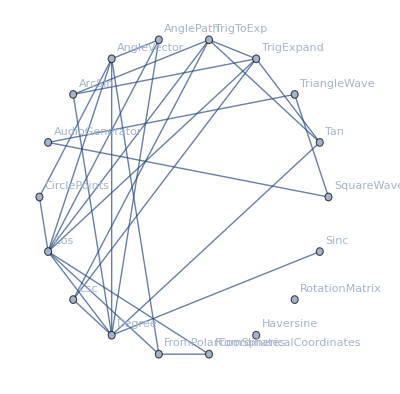
<|attributes→{Listable,NumericFunction,Protected},common option values→Missing[NotApplicable],date introduced→Day: Thu 23 Jun 1988,date last modified→Day: Mon 30 Mar 2015,dates modified→{Day: Wed 19 May 1999,Day: Wed 9 Jul 2014,Day: Mon 30 Mar 2015},documentation basic examples→{{The argument is given in radians:,Sin[Pi/3],(√3)/2},{Use Degree to specify an argument in degrees:,Sin[60Degree],(√3)/2},{Plot over a subset of the reals:,Plot[Sin[x],{x,0,2Pi}],-Graphics-},{Series expansion:,Series[Sin[x],{x,0,10}],x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11}},documentation example counts→{BasicExamples→4,Scope→45,GeneralizationsExtensions→0,Options→0,Applications→12,PropertiesRelations→12,PossibleIssues→6,InteractiveExamples→0,NeatExamples→5},documentation example inputs→{BasicExamples→{{Sin[Pi/3]},{Sin[60Degree]},{Plot[Sin[x],{x,0,2Pi}]},{Series[Sin[x],{x,0,10}]}},Scope→{{Sin[1.2]},{N[Sin[12/10],50],Sin[1.20000000000000000000000],Sin[1.5707963267948966192213216916397514421]},{Sin[2.5+I]},{Sin[1.2]//Timing,Sin[1.2];//Timing},{Sin[Interval[{-Pi,Pi}]]},{Sin[{1.2,1.5,1.8}],Sin[(π | u
v | π/2) ]},{Table[Sin[n π/6],{n,0,6}]},{Table[Sin[n π/6],{n,0,6}]},{Sin[Infinity],Sin[ComplexInfinity]},{Sin[Pi/5],Sin[Pi/24],FunctionExpand[%]},{Assuming[m∈Integers,Refine[Sin[π m]]]},{Assuming[m∈Integers,FullSimplify[Refine[Sin[π (1/2+m)]]]],xmax=Solve[D[Sin[x],x]== 0&&0<x<π,x][[1,1]],Plot[Sin[x],{x,0,2π},Sequence[Epilog -> {PointSize[Large], RGBColor[1, 0, 0], Point[{Pi/2, 1}]}]]},{Plot[Sin[x],{x,0,4π}]},{ContourPlot[Re[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]],ContourPlot[Im[Sin[x+ⅈ y]],{x,-2π,2π},{y,-π,π},Sequence[Contours -> 24, FrameTicks -> {{{-Pi, -Pi/2, 0, Pi/2, Pi}, None}, {{-2*Pi, -Pi, 0, Pi, 2*Pi}, None}}]]},{Table[PolarPlot[Sin[k ϕ],{ϕ,0,2 π},Sequence[Frame→True,FrameTicks→{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1},None}},PlotLabel→k=<>ToString[k]]],{k,1,8}]},{FunctionDomain[Sin[x],x],FunctionDomain[Sin[z],z,Complexes]},{FunctionRange[Sin[x],x,y],FunctionRange[Sin[z],z,y,Complexes]},{FunctionPeriod[Sin[x],x]},{Sin[-x]},{FullSimplify[Sin[Conjugate[z]]==Conjugate[Sin[z]]]},{TrigExpand[Sin[2x]]},{TrigExpand[Sin[x+y]]},{TrigExpand[Sin[4x]],TrigReduce[%]},{TrigFactor[Sin[x]+Sin[y]]},{ComplexExpand[Sin[x+I y]]},{TrigToExp[Sin[z]]},{D[Sin[x],x]},{Table[D[Sin[x],{x,n}],{n,1,4}],Plot[Evaluate[%],{x,-2π,2π},PlotLegends→{First Derivative,Second Derivative,Third Derivative,Fourth Derivative}]},{D[Sin[x],{x,n}]},{Integrate[Sin[x],x]},{Integrate[Sin[x],{x,0,2 π}]},{Integrate[Sin[x]Cos[x],x],Integrate[Sin[z]^a,z]},{Series[Sin[x],{x,0,7}],terms=Normal@Table[Series[Sin[x],{x,0,m}],{m,1,5,2}];
Plot[{Sin[x],terms},{x,-2π,2π},PlotRange→{-1.5,1.5},PlotLegends->Expressions]},{SeriesCoefficient[Sin[x],{x,0,n}]},{FourierSeries[Sin[z],z,1]},{Sin[π/2+x+x^2/2+x^3/3+O[x]^4]},{FourierTransform[Sin[t],t,ω ]},{LaplaceTransform[Sin[t],t,s ]},{MellinTransform[Sin[x],x,s ]},{Simplify[Cos[Pi/2-x]]},{Simplify[Sqrt[(π x)/2]BesselJ[1/2,x]],Simplify[- I Sqrt[(π I x)/2]BesselI[1/2,I x]]},{Simplify[Sqrt[8 π/3]SphericalHarmonicY[1,-1,θ,0]]},{MeijerGReduce[Sin[x],x],Activate[%]},{DifferentialRootReduce[Sin[x],x]},{Sin[α]//TraditionalForm}},GeneralizationsExtensions→{},Options→{},Applications→{{ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]},{ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]},{ParametricPlot[Exp[t/10]{Sin[t],Cos[t]},{t,0,10Pi},PlotRange->All]},{Animate[Graphics[Line[{{0,0},{Sin[t],Cos[t]}}],PlotRange->1.2],{t,0,10Pi}]},{Play[Sin[2 Pi 440 t],{t,0,1}]},{DSolve[x''[t]+ω^2 x[t]==0,x[t],t]},{RotationMatrix[θ],%.{x,y}},{ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{ϕ,-π,π},{θ,0,π}]},{ParametricPlot3D[{Cos[ϕ]+1/2 Cos[θ] Cos[ϕ],Sin[ϕ]+1/2 Cos[θ] Sin[ϕ],Sin[θ]/2},{ϕ,-π,π},{θ,0,2 π}]},{Plot3D[Sin[x]Sin[y],{x,0,10Pi},{y,0,10Pi}]},{ContourPlot3D[Sin[x]+Sin[y]+Sin[z],{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi, 2Pi},Contours→{0},Mesh→False,BoundaryStyle→None,
ContourStyle→Opacity[0.8]]},{Plot[Sum[N[Sin[j^2 x]/j^2], {j, 1, 12}],{x,0,2Pi}]}},PropertiesRelations→{{Sin[x+2Pi],Sin[-x],Sin[I x],1/Sin[x]},{Sin[3z]^2+(2 Cos[z] Cos[2 z]-Cos[z])^2,Simplify[%],Sin[x]-Sin[y]-2Cos[(x+y)/2]Sin[(x-y)/2],Simplify[%]},{{Sin[ArcSin[z]], Sin[2ArcSin[z]], Sin[3ArcSin[z]]},FunctionExpand[%]},{Reduce[Sin[z]^2+3 Sin[z+Pi/6]==4,z]},{FindRoot[Sin[z]^2+3 Sin[z+Pi/6]==z,{z, 2}]},{Reduce[Sin[α x+β]==0,x]},{FourierTransform[Sin[t],t,s],LaplaceTransform[Sin[t],t,s]},{{BesselJ[1/2,z],MathieuS[1,0,z],JacobiSN[z,0], HypergeometricPFQ[{},{3/2},-z],MeijerG[{{},{}},{{1/2},{0}},z]}},{NumericQ[Sin[2+E]]},{DifferentialRootReduce[Sin[x],x]},{GeneratingFunction[Sin[n],n,x],Series[%,{x,0,5}]//FullSimplify},{ExponentialGeneratingFunction[Sin[n],n,x]}},PossibleIssues→{{Sin[10.^30],N[Sin[10^30],20]},{N[Sin[10^100],20],Block[{$MaxExtraPrecision=200},N[Sin[10^100],20]]},{Sin[10.^3I],MachineNumberQ[%]},{{Sin[Pi/8],Sin[Pi/12],Sin[Pi/15]},FunctionExpand[%]},{Integrate[1/(2+Sin[x]),x],Plot[%,{x,0,2Pi}]},{sin x,sin(x)}},InteractiveExamples→{},NeatExamples→{{Plot[Sin[x]+Sin[Sqrt[2]x],{x,0,40Pi}]},{Sin[π/2^12]//FunctionExpand},{Integrate[Sin[x^n],x]},{DensityPlot[Sin[3x]Sin[5y]+1/2Sin[5x]Sin[3y],{x,0,2Pi},{y,0,2Pi}]},{ArrayPlot[Table[Sin[x y],{x,-20,20},{y,-20,20}]]}}},documentation example text→{BasicExamples→{{The argument is given in radians:},{Use Degree to specify an argument in degrees:},{Plot over a subset of the reals:},{Series expansion:}},Scope→{{Evaluate numerically:},{Evaluate to high precision:,The precision of the output tracks the precision of the input:,The precision of the output can be larger than the precision of the input:},{Sin can take complex number inputs:},{Evaluate Sin efficiently at high precision:},{Apply to Interval inputs:},{Lists and matrices:},{Values of Sin at fixed points:},{Sin has exact values at rational multiples of pi:},{Values at infinity:},{Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:},{Zeros of Sin:},{Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:},{Plot the Sin function:},{Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):},{Polar plot with r=sin(k ϕ):},{Sin is defined for all real and complex values:},{Real range:,Range in the complex plane:},{Period:},{Odd function:},{Mirror property sin(Conjugate[z])==Conjugate[sin(z)]:},{Double-angle formula using TrigExpand:},{Angle sum formula:},{Multiple-angle expressions:,Recover the original expression using TrigReduce:},{Convert sums to products using TrigFactor:},{Expand using ComplexExpand assuming real variables x and y:},{Convert to exponentials using TrigToExp:},{First derivative:},{Higher derivatives:},{Formula for the n^th derivative:},{Compute the indefinite integral using Integrate:},{Definite integral of Sin over a period is 0:},{More integrals:},{Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:},{General term in the series expansion using SeriesCoefficient:},{FourierSeries:},{Series:},{Compute the Fourier transform using FourierTransform:},{LaplaceTransform:},{MellinTransform:},{Use Simplify to find a representation through Cos:},{Representation through Bessel functions:},{Representation through SphericalHarmonicY:},{Representation in terms of MeijerG:},{Sin can be represented as a DifferentialRoot:},{TraditionalForm formatting:}},GeneralizationsExtensions→{},Options→{},Applications→{{Draw a circle:},{Lissajous figure:},{Equiangular (logarithmic) spiral:},{Motion in a circle:},{Play a pure tone at 440 Hz:},{Solve an equation for harmonic motion:},{Rotation matrix:,Rotate a vector:},{Plot a sphere:},{Plot a torus:},{Waves:},{Triple-periodic surface:},{Approximate the almost nowhere differentiable Riemann–Weierstrass function:}},PropertiesRelations→{{Basic parity and periodicity properties are automatically applied:},{Complicated expressions containing trigonometric functions do not simplify automatically:},{Compose with inverse functions:},{Solve a trigonometric equation:},{Numerically find a root of a transcendental equation:},{Reduce a trigonometric equation:},{Fourier transform:},{Sin appears in special cases of many mathematical functions: },{Sin is a numeric function:},{Sin can be represented as a DifferentialRoot:},{The generating function for Sin:},{The exponential generating function for Sin:}},PossibleIssues→{{Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:},{A larger setting for $MaxExtraPrecision can be needed:},{Machine-number inputs can give high-precision results:},{Use FunctionExpand to express sine of rationals times π using radicals:},{Continuous functions involving Sin[x] can give discontinuous indefinite integrals:},{In TraditionalForm, parentheses are needed around the argument:}},InteractiveExamples→{},NeatExamples→{{Noncommensurate waves (quasiperiodic function):},{Some arguments can be expressed as a finite sequence of nested radicals:},{Indefinite integral of sin(x^n):},{Chladni figure:},{Plot Sin at integer points:}}},entity classes→{},eponymous people→{},equal-precedence symbols→Missing[NotApplicable],external links→{MathWorld→http://mathworld.wolfram.com/Sine.html,WolframFunctionsSite→http://functions.wolfram.com/ElementaryFunctions/Sin/},frequencies of usage→{All→0.00188577,StackExchange→0.00520667,TypicalProductionCode→0.00424223,WolframAlphaCodebase→0.00102896,WolframDemonstrations→0.00530721,WolframDocumentation→0.00374346},full version introduced→1,full version last modified→10.1,full versions modified→{4,10.,10.1},functionality areas→{BasicSymbols},symbol background→Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.
Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.
Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).
Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ∑_(k=0)^∞ (-1)^(k-1)/((2 k-1)!)z^(2 k-1) about the origin.
The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.,keyboard shortcuts→Missing[NotAvailable],link trails→{{guide/WolframRoot,guide/FormulaManipulation,guide/AlgebraicTransformations,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/MathematicalFunctions,guide/ElementaryFunctions,guide/TrigonometricFunctions,ref/Sin}},memberships→{},name→Sin,option names→{},options→{},plaintext usage→Sin[z] gives the sine of z.,precedence ranks→Missing[NotApplicable],ranks of usage→{All→30,StackExchange→20,TypicalProductionCode→29,WolframAlphaCodebase→37,WolframDemonstrations→22,WolframDocumentation→20},related entities→Missing[NotAvailable],related guide pages→{Precollege Educationpaclet:guide/PrecollegeEducation,Trigonometric Functionspaclet:guide/TrigonometricFunctions,Summary of New Features in 12paclet:guide/SummaryOfNewFeaturesIn12,Functions for Separable Coordinate Systemspaclet:guide/FunctionsForSeparableCoordinateSystems,Mathematical Functionspaclet:guide/MathematicalFunctions,Elementary Functionspaclet:guide/ElementaryFunctions,Neural Networkspaclet:guide/NeuralNetworks},related symbols→{AngleVector,ArcSin,Cos,Tan,Csc,Degree,TrigToExp,TrigExpand,Sinc,Haversine,CirclePoints},relationship community graph→-Graphics-,relationship graph→-Graphics-,short notations→Missing[NotApplicable],subject classifications→{Mathematics Subject Classification 2010→{33B10,51Nxx}},symbols linking to→{AnglePath,AngleVector,ArcSin,AudioGenerator,CirclePoints,Cos,Csc,Degree,FromPolarCoordinates,FromSphericalCoordinates,Haversine,RotationMatrix,Sinc,SquareWave,TriangleWave},symbols using as attribute→{},symbols using as option→{},text strings→{Sin[z]
gives the sine of z.,Mathematical function, suitable for both symbolic and numerical manipulation.,Unless explicitly given as a Quantity object, the argument of Sin is assumed to be in radians. (Multiply by Degree to convert from degrees.)19487,Sin is automatically evaluated when its argument is a simple rational multiple of π; for more complicated rational multiples, FunctionExpand can sometimes be used.3266,For certain special arguments, Sin automatically evaluates to exact values.,Sin can be evaluated to arbitrary numerical precision.,Sin automatically threads over lists.,The argument is given in radians:,Use Degree to specify an argument in degrees:,Plot over a subset of the reals:,Series expansion:,Evaluate numerically:,Evaluate to high precision:,The precision of the output tracks the precision of the input:,The precision of the output can be larger than the precision of the input:,Sin can take complex number inputs:,Evaluate Sin efficiently at high precision:,Apply to Interval inputs:,Lists and matrices:,Values of Sin at fixed points:,Sin has exact values at rational multiples of pi:,Values at infinity:,Simple exact values are generated automatically:,More complicated cases require explicit use of FunctionExpand:,Zeros of Sin:,Extrema of Sin:,Find the first positive maximum as a root of (d sin(x))/dx==0:,Plot the Sin function:,Plot the real part of sin(x+ⅈ y):,Plot the imaginary part of sin(x+ⅈ y):,Polar plot with r=sin(k ϕ):,Sin is defined for all real and complex values:,Real range:,Range in the complex plane:,Period:,Odd function:,Mirror property sin(z^*)==sin(z)^*:,Double-angle formula using TrigExpand:,Angle sum formula:,Multiple-angle expressions:,Recover the original expression using TrigReduce:,Convert sums to products using TrigFactor:,Expand using ComplexExpand assuming real variables x and y:,Convert to exponentials using TrigToExp:,First derivative:,Higher derivatives:,Formula for the n^th derivative:,Compute the indefinite integral using Integrate:,Definite integral of Sin over a period is 0:,More integrals:,Find the Taylor expansion using Series:,Plots of the first three approximations for Sin around x=0:,General term in the series expansion using SeriesCoefficient:,FourierSeries:,Series:,Compute the Fourier transform using FourierTransform:,LaplaceTransform:,MellinTransform:,Use Simplify to find a representation through Cos:,Representation through Bessel functions:,Representation through SphericalHarmonicY:,Representation in terms of MeijerG:,Sin can be represented as a DifferentialRoot:,TraditionalForm formatting:,Draw a circle:,Lissajous figure:,Equiangular (logarithmic) spiral:,Motion in a circle:,Play a pure tone at 440 Hz:,Solve an equation for harmonic motion:,Rotation matrix:,Rotate a vector:,Plot a sphere:,Plot a torus:,Waves:,Triple-periodic surface:,Approximate the almost nowhere differentiable Riemann–Weierstrass function:,Basic parity and periodicity properties are automatically applied:,Complicated expressions containing trigonometric functions do not simplify automatically:,Compose with inverse functions:,Solve a trigonometric equation:,Numerically find a root of a transcendental equation:,Reduce a trigonometric equation:,Fourier transform:,Sin appears in special cases of many mathematical functions:,Sin is a numeric function:,Sin can be represented as a DifferentialRoot:,The generating function for Sin:,The exponential generating function for Sin:,Machine-precision input is insufficient to get a correct answer:,With exact input, the answer is correct:,A larger setting for $MaxExtraPrecision can be needed:,Machine-number inputs can give high-precision results:,Use FunctionExpand to express sine of rationals times π using radicals:,Continuous functions involving Sin[x] can give discontinuous indefinite integrals:,In TraditionalForm, parentheses are needed around the argument:,Noncommensurate waves (quasiperiodic function):,Some arguments can be expressed as a finite sequence of nested radicals:,Indefinite integral of sin(x^n):,Chladni figure:,Plot Sin at integer points:,Sin is the sine function, which is one of the basic functions encountered in trigonometry. It is defined for real numbers by letting x be a radian angle measured counterclockwise from the x axis along the circumference of the unit circle. Sin[x] then gives the vertical coordinate of the arc endpoint. The equivalent schoolbook definition of the sine of an angle θ in a right triangle is the ratio of the length of the leg opposite θ to the length of the hypotenuse.,Sin automatically evaluates to exact values when its argument is a simple rational multiple of π. For more complicated rational multiples, FunctionExpand can sometimes be used to obtain an explicit exact value. To specify an argument using an angle measured in degrees, the symbol Degree can be used as a multiplier (e.g. Sin[30 Degree]). When given exact numeric expressions as arguments, Sin may be evaluated to arbitrary numeric precision. Other operations useful for manipulation of symbolic expressions involving Sin include TrigToExp, TrigExpand, Simplify, and FullSimplify.,Sin threads element-wise over lists and matrices. In contrast, MatrixFunction can be used to give the sine of a square matrix (i.e. the power series for the sine function with ordinary powers replaced by matrix powers).,Sin is periodic with period 2π, as reported by FunctionPeriod. Sin satisfies the identity sin^2(x)+cos^2(x)==1, which is equivalent to the Pythagorean theorem. The definition of the sine function is extended to complex arguments z using the definition sin(z)==1/2 ⅈ(ⅇ^(-ⅈ z)-ⅇ^(ⅈ z)), where ⅇ is the base of the natural logarithm. The sine function is entire, meaning it is complex differentiable at all finite points of the complex plane. Sin[z] has series expansion ∑_(k = 0)^∞  about the origin.,The inverse function of Sin is ArcSin. The hyperbolic sine is given by Sinh. Other related mathematical functions include Cos, Tan, and Csc.},timeline→-Graphics-,timeline events→Interval[{Day: Thu 23 Jun 1988,Day: Mon 30 Mar 2015}]Sin,translations→{Simplified Chinese→正弦,Traditional Chinese→正弦,French→sinus,German→Sinus,Modern Greek→ημίτονο,Japanese→正弦,Korean→사인,Lithuanian→sinusas,Polish→sinus,Portuguese→seno,Russian→синус,Spanish→seno,Ukrainian→синус,Vietnamese→sin},typeset usage→Sin[z] gives the sine of z. ,URL→http://reference.wolfram.com/language/ref/Sin.html,version introduced→1,version last modified→10.1,versions modified→{4,10.,10.1},Wolfram documentation link→Sinpaclet:ref/Sin|>

```mathematica
WolframLanguageData["Sin","PropertyAssociation"]
```

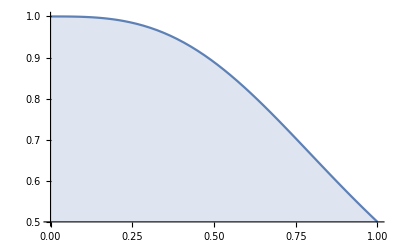
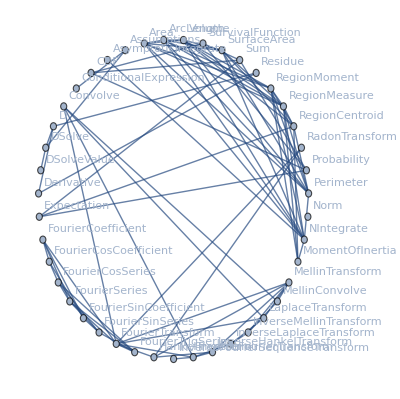
<|attributes→{Protected,ReadProtected},common option values→Missing[NotAvailable],date introduced→Day: Thu 23 Jun 1988,date last modified→Day: Tue 16 Apr 2019,dates modified→{Day: Tue 3 Sep 1996,Day: Tue 18 Nov 2008,Day: Wed 9 Jul 2014,Day: Tue 16 Apr 2019},documentation basic examples→{{Indefinite integral:,Integrate[x^2+Sin[x],x],x^3/3-Cos[x]},{Compute a definite integral:,Integrate[1/(x^3+1),{x,0,1}],1/18 (2 √3 π+Log[64]),Visualize the area given by this integral:,Plot[1/(x^3+1),{x,0,1},Filling→Axis],-Graphics-},{Use Esc int Esc to enter ∫ and Esc dd Esc to enter ⅆ:,∫Sqrt[x+Sqrt[x]]ⅆx,1/12 √(√x+x) (-3+2 √x+8 x+(3 ArcSinh[x^(1/4)])/(√(1+√x) x^(1/4))),TraditionalForm[%],1/12 √(x+√x) (8 x+2 √x+(3 sinh^-1(x^(1/4)))/(√(√x+1) x^(1/4))-3)},{Use Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit:,∫_0^∞ Log[x] Exp[-x^2]ⅆx,-1/4 √π (EulerGamma+Log[4])}},documentation example counts→{BasicExamples→4,Scope→76,GeneralizationsExtensions→0,Options→11,Applications→67,PropertiesRelations→14,PossibleIssues→10,InteractiveExamples→1,NeatExamples→2},documentation example inputs→{BasicExamples→{{Integrate[x^2+Sin[x],x]},{Integrate[1/(x^3+1),{x,0,1}],Plot[1/(x^3+1),{x,0,1},Filling→Axis]},{∫Sqrt[x+Sqrt[x]]ⅆx,TraditionalForm[%]},{∫_0^∞ Log[x] Exp[-x^2]ⅆx}},Scope→{{int=Integrate[1/(x^3+1),x],D[int,x]//Simplify},{∫(a x^2 +b x +c)ⅆx},{Integrate[x^2,x,GeneratedParameters→C]},{Integrate[(2x+3)/(x^2+5x+6),{x,0,2}],Integrate[BesselJ[2,x]/(1+x^2),{x,0,∞}],Integrate[Sin[x]/x,{x,-∞,∞}]},{∫_0^π Cos[x]ⅆx},{Integrate[(a x)/(x^3+2),{x,1,∞}],Integrate[Exp[-c x^2],{x,-∞,∞}],Integrate[Exp[-c x^2],{x,-∞,∞},Assumptions→Re[c]==0]},{Integrate[BesselJ[3,y]/(x+1),{x,0,5},{y,0,5}],Integrate[Exp[-x+y],{x,0,∞},{y,0,1}]},{Integrate[Sin[x y],{x,0,1},{y,0,x}],∫_0^1 ∫_0^x Sin[x y]ⅆyⅆx,Plot3D[Sin[x y],{x,y}∈Triangle[{{0,0},{0,1},{1,0}}]]},{Integrate[1,{x,y}∈Circle[]],Integrate[1,x∈Ball[3]],∫_({x,y,z}∈Tetrahedron[]) (x^4 y^5+z^10)},{∫_({x,y}∈Rectangle[]) x y^2},{Integrate[f'[x],x],Integrate[((1-f[x])f'[x])/E^f[x], x]},{Integrate[{x,1/(√x),Sin[x]},{x,0,5}],Integrate[(x | √x | x^(1/3)
√x | x^(1/3) | x^(1/4)
x^(1/3) | x^(1/4) | x^(1/5)),{x,0,5}]//MatrixForm},{Integrate[E^(-x^x),{x,0,1}],N[%]},{∫x^n ⅆx,∫1/x ⅆx,∫Sin[x]ⅆx,∫Exp[x]ⅆx,Integrate[Exp[x], x, GeneratedParameters->C]},{∫Sec[x]^2 ⅆx,∫Cot[x]ⅆx,∫Sec[x]ⅆx,D[%,x]//Simplify},{flist={x^n,1/x,b^x,Log[x],Sin[x],Cos[x],1/(x^2+a^2),1/(x^2-a^2)};,Grid[Map[Pane[Style[#1, ScriptLevel -> 0], {150, 35}, ImageSizeAction -> ShrinkToFit, Alignment -> {Center, Center}]&,Prepend[Transpose[{flist,Integrate[flist,x]}],{Style[f[x],Bold],Style[∫f[x]ⅆx,Bold]}],{2}],Sequence[Background -> {None, {{RGBColor[0.87, 0.94, 1], None}}, {{1, 1} -> Hue[0.6, 0.4, 1], {1, 2} -> Hue[0.6, 0.4, 1]}}, BaseStyle -> {FontSize -> 16}, Frame -> All]]//TraditionalForm},{Integrate[1/(x^4-1),x],Integrate[(x + 1)/(a^2 x^2 +c^2),x],Integrate[1/(x^5+2x+1),x]},{∫ArcSin[x]ⅆx,∫Cosh[x]ⅆx,∫x^2/(√(a^2+x^2))ⅆx,∫Exp[a x]Cos[b x]ⅆx},{intℂ=∫Tan[x]ⅆx,D[intℂ,x],intℝ=Log[RealAbs[Sec[x]]];,Simplify[D[intℝ,x]],FullSimplify[Re[intℂ]==Re[intℝ]],Plot[{Re[intℂ],Re[intℝ]},{x,0,4Pi},PlotTheme→{Detailed,NeonColors,DashedLines}],Plot[{Im[intℂ],Im[intℝ],Cos[x]},{x,0,4Pi},PlotTheme→{Detailed,NeonColors,DashedLines}]},{Integrate[Sqrt[x]Sqrt[1+x],x],Integrate[Sqrt[x]Sqrt[1+x]Sqrt[2+x],x]},{Integrate[Exp[-x^2],x],Integrate[Log[1+x]^2/x,x],Integrate[Log[Log[x]],x],Integrate[Tan[x]^n,x]},{flist={BesselJ[0,x],Erf[x],EllipticE[x],Sqrt[x]PolyLog[2,x],AiryAi[x],SinhIntegral[2/(x+1)]};,Grid[Map[Pane[Style[#1, ScriptLevel -> 0], {Automatic, 50}, ImageSizeAction -> ShrinkToFit, Alignment -> {Center, Center}]&,Prepend[Transpose[{flist,Integrate[flist,x]}],{Style[f[x],Bold],Style[∫f[x]ⅆx,Bold]}],{2}],Sequence[Background -> {None, {{RGBColor[0.87, 0.94, 1], None}}, {{1, 1} -> Hue[0.6, 0.4, 1], {1, 2} -> Hue[0.6, 0.4, 1]}}, BaseStyle -> {FontSize -> 14}, Frame -> All]]//TraditionalForm},{Integrate[p[x]Log[p[x]],p[x]]},{Integrate[x^4+ x^2+1,{x,1,3}],Plot[-12+19 x-8 x^2+x^3,{x,1,3},Filling→Axis],Integrate[a x^2 + b x+c,{x,-2,2}],Integrate[x^n + n x,{x,0,a},Assumptions→n>1&&n∈ℤ]},{Integrate[1/(x^4+x^2+1),{x,0,Infinity}],Plot[1/(x^4+x^2+1),{x,0,5},Filling→Axis,PlotRange→All,Epilog→{RGBColor[0.368417, 0.506779, 0.709798],Arrow[{{0,0},{5,0}}]}],Integrate[(4x^2-7x-12)/((x+2)(x-3)),{x,-1,2}],Plot[(4 x^2-7 x-12)/((x+2) (x-3)),{x,-1,2},Filling→0,PlotRange→All]},{Integrate[(1+x^3) CubeRoot[x],{x,-1,1}],Plot[(1+x^3) CubeRoot[x],{x,-1,1},Filling→Axis,FillingStyle→{RGBColor[0.880722, 0.611041, 0.142051, 0.5],RGBColor[0.368417, 0.506779, 0.709798, 0.5]}],Integrate[1/((2+x^2)Sqrt[4+3x^2]),{x,-∞,∞}],Plot[1/((2+x^2) √(4+3 x^2)),{x,-7,7},Filling→0,AxesOrigin→{0,0},Epilog→{RGBColor[0.368417, 0.506779, 0.709798],Arrowheads[{-Medium,Medium}],Arrow[{{-7,0},{7,0}}]}]},{Integrate[Cos[2x]^4,{x,0,π}],Plot[Cos[2x]^4,{x,0,π/2},Filling→Axis],Integrate[x^2Sin[2x],{x,0,2π}],Plot[x^2Sin[2x],{x,0,2π},Filling→Axis,FillingStyle→{RGBColor[0.880722, 0.611041, 0.142051, 0.5],RGBColor[0.368417, 0.506779, 0.709798, 0.5]}]},{Integrate[x^5Log[x],{x,1,2}],Plot[x^5Log[x],{x,1,2},Filling→Axis],Integrate[Exp[-x+Exp[-x]],{x,0,∞}],Plot[Exp[-x+Exp[-x]],{x,0,4},PlotRange→Full,Filling→Axis,Epilog→{RGBColor[0.368417, 0.506779, 0.709798],Arrowheads[Medium],Arrow[{{0,0},{4,0}}]}]},{Integrate[x Cosh[x],{x,0,a}],Integrate[Exp[-I x]/Cosh[x]^3,{x,-∞,∞}]
},{Integrate[x/Sqrt[1-x],{x,0,1}],Plot[x/Sqrt[1-x],{x,0,1},Filling→Axis],(∖[Limit])_(a→1^-)∫_0^a x/(√(1-x))ⅆx},{area=∫_-1^1 x^2/(√(1-x^4))ⅆx,%//N,Plot[x^2/(√(1-x^4)),{x,-1,1},Filling→0],area==Limit[Integrate[x^2/(√(1-x^4)),{x,a,b},Assumptions→-1<a<b<1],{a,b}→{-1,1},Direction→{FromAbove,FromBelow}]},{Integrate[x E^(-x),{x,1,∞}],% == (∖[Limit])_(a→∞)Integrate[x E^(-x),{x,1,a}],∫_(-∞)^∞ ⅇ^(-x^2)ⅆx,%==(∖[Limit])_({a,b}→{-∞,∞})∫_a^b ⅇ^(-x^2)ⅆx},{Integrate[x^n,{x,0,1}],Integrate[E^(a x),{x,0,∞}],Integrate[Sin[ax]/x,{x,0,∞}]},{Integrate[Sin[t]/t,{t,a,b}],Integrate[Cos[Sin[x]^2],{x,0,2π}]
,%//N,Plot[Cos[Sin[x]^2],{x,0,2π},Filling→0,PlotRange→{0,1}]},{flist={BesselJ[2,x]/x,BesselK[0,x]^2,AiryAi[x]^2,Exp[-x] Sinc[x],Sin[x^2]Erfc[x]};,Grid[Map[Pane[Style[#1, ScriptLevel -> 0], {Automatic, 50}, ImageSizeAction -> ShrinkToFit, Alignment -> {Center, Center}]&,Prepend[Transpose[{flist,Integrate[flist,{x,0,∞}]}],{Style[f[x],Bold],Style[HoldForm[∫_0^∞ f[x]ⅆx],Bold]}],{2}],Sequence[Background -> {None, {{RGBColor[0.87, 0.94, 1], None}}, {{1, 1} -> Hue[0.6, 0.4, 1], {1, 2} -> Hue[0.6, 0.4, 1]}}, BaseStyle -> {FontSize -> 16}, Frame -> All]]//TraditionalForm},{Integrate[√x,{x,I,3-I}],Integrate[1/(z+1/2),{z,1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1}]//FullSimplify,Integrate[(ⅈ Exp[ⅈ ω])/(Exp[ⅈ ω]+1/2),{ω,0,2π}],ComplexPlot[1/(z+1/2),{z,-1.2-1.2I,1.2+1.2I},Epilog→{Arrowheads[Medium],Arrow[ReIm/@Exp[2π ⅈ/6 Range[0,6]]],Red,Arrow[{{1,-.05},{1,0}}],Dashed,Circle[]}]},{f[x_]  := Piecewise[{{-x^2, x <0}, {x^2, True}}],∫f[x]ⅆx,Simplify[D[%,x]==f[x]]},{f[x_]  := Piecewise[{{-x+1, x <0}, {x, 0<x<1}, {x^2, True}}],g[x_]=∫f[x]ⅆx,Resolve[ForAll[x,x!=0&&x∈ℝ,g'[x]==f[x]]],Plot[{f[x],g[x]},{x,-2,2},PlotTheme→{Detailed,DashedLines}]},{unitInt=Integrate[x UnitStep[x], x],Plot[{x UnitStep[x],unitInt}, {x,-2,2},PlotTheme→{Detailed,DashedLines}],clipInt=Integrate[Clip[x]^2, x],Plot[{Clip[x]^2,clipInt}, {x,-2,2},PlotTheme→{Detailed,DashedLines}]},{maxInt=Integrate[Max[Sin[x],Cos[x]],x],Simplify[D[maxInt,x]==Max[Sin[x],Cos[x]]],Plot[{Max[Sin[x],Cos[x]],maxInt},{x,0,4Pi},PlotTheme→{Detailed,DashedLines}]},{f[x_]:=Piecewise[{{1, x<2}, {x^3, 2<x<3}, {0, True}}],Integrate[f[x],{x,0,3}],int=Integrate[f[t],{t,0,x},Assumptions→x>0],Plot[{f[x],int},{x,0,4},PlotTheme→{Detailed,DashedLines}]},{Integrate[Floor[x^2],{x,0,3}],Plot[Floor[x^2],{x,0,3},Filling→Axis],Integrate[PrimePi[n],{n,0,100}],Plot[PrimePi[x],{x,0,100},Filling→Axis],Integrate[Ceiling[x^2+TriangleWave[x]],{x,-2,2} ]},{f[x_]:=x^2 UnitStep[x+1],int=Integrate[f[x],{x,-3,a}],Plot[{f[a],int},{a,-2,2},PlotTheme→{Detailed,DashedLines}]},{f[x_]:=Max[Sin[x],Cos[x]],f[x]//PiecewiseExpand,maxInt=Integrate[f[x],{x,0,a},Assumptions→0<a<2Pi],Plot[{f[a],maxInt},{a,0,2Pi},PlotTheme→{Detailed,DashedLines}]},{Integrate[DiracDelta[x],{x,-∞,∞}],Integrate[Sin[x]^2 HeavisideTheta[x+π]HeavisideTheta[π-x],{x,-∞,∞}],Integrate[DiracDelta[Cos[x^2-1]],{x,-2,2}]},{Integrate[DiracDelta[x],x],Integrate[DiracDelta[x],x,x]},{Integrate[f[x] DiracDelta[x-a],{x,-1,1},Assumptions→a∈Reals],Integrate[Cos[x-a] HeavisideLambda[x],{x,0,Pi},Assumptions→a∈Reals]},{f=Interpolation[{10,-5,10,-10,20}],g=Head[Integrate[f[x],x]],g'[3.5]==f[3.5],Plot[g[x],{x,1,5}]},{Integrate[a x^2 + b x +c, x, x]//Expand,D[%,{x,2}],∫∫∫1/(x^2+4)ⅆxⅆxⅆx,FullSimplify[D[%,{x,3}]]},{Integrate[x^2Sin[y], y, x],D[%,x,y]},{Integrate[x,x,GeneratedParameters→C],Integrate[x,x,x,GeneratedParameters→C],D[%,x,x],Integrate[x,x,y,GeneratedParameters→C],D[%,x,y]},{Integrate[Exp[x]Cos[y], {x,0,a}, {y,0,b}],∫_0^a ∫_0^b Exp[x]Cos[y]ⅆyⅆx,∫_0^b ∫_0^a Exp[x]Cos[y]ⅆxⅆy},{Integrate[(x+y), {y,0,1}, x]},{Integrate[x^2y/(x+y),{x,0,3},{y,1,2}],Plot3D[(x^2 y)/(x+y),{x,0,3},{y,1,2},Filling→Axis,FillingStyle→Opacity[0.6],Mesh→None]},{Integrate[y Sin[x y],{x,1,4},{y,0,π}],Plot3D[{y Sin[x y],0},{x,1,4},{y,0,π},Sequence[PlotRange -> All, Mesh -> None, PlotStyle -> {GrayLevel[0.3], FaceForm[]}, PlotTheme -> SolidGrid, BoxRatios -> 1, Lighting -> Neutral, ViewPoint -> {2.25, -1.9, 1.5}, Filling -> {1 -> {Axis, {Directive[Specularity[1], Hue[0.58, 1, 0.5, 0.5]], GrayLevel[0.2]}}}]]},{∫_-2^2 ∫_(2 x^2)^(4+x^2) (8-(3 y)/3-(3 x y)/3+(x^2 y)/3+(x^3 y)/3)ⅆyⅆx,Plot[{2x^2,4+x^2},{x,-2,2},Filling→{1→{2}},PlotLegends→Expressions],Plot3D[8-(3 y)/3-(3 x y)/3+(x^2 y)/3+(x^3 y)/3,{x,y}∈ImplicitRegion[-2<x<2&&2 x^2<y<4+x^2,{x,y}],FillingStyle→Opacity[.5],Filling→Axis,PlotRange→All,ViewPoint→{.3,3.1,1.3},Mesh→None]},{Integrate[Cos[z]Exp[x]y,{x,0,1},{y,-1,2},{z,0,3}],RegionPlot3D[0<x<1&&-1<y<2&&0<z<3,{x,-0.5,1.5},{y,-1.5,2.5},{z,-0.5,3.5}]},{Integrate[a b^2 -c/d^e,{a,0,1},{b,1,2},{c,2,3},{d,3,4},{e,4,5}],N[%]},{f[r_,θ_]:=Sin[θ]/r ,CoordinateChartData[Hyperspherical,CoordinateRangeAssumptions,{r,θ,φ,ψ}],CoordinateChartData[Hyperspherical,VolumeFactor,{r,θ,φ,ψ}],∫_-π^π ∫_0^π ∫_0^π ∫_0^R f[r,θ](r^3 Sin[θ]^2 Sin[φ])ⅆrⅆθⅆφⅆψ},{Integrate[1,{x,y}∈Disk[]],∫_({x,y}∈Disk[]) 1,Integrate[Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]},{∫_({x,y}∈Disk[]) (Cos[3x]Sin[5y]+x^2),∫_-1^1 ∫_-1^1 (Cos[3x]Sin[5y]+x^2)Boole[x^2+y^2≤1]ⅆyⅆx,∫_-1^1 ∫_(-√(1-x^2))^(√(1-x^2)) (Cos[3x]Sin[5y]+x^2)ⅆyⅆx,Plot3D[Cos[3x]^2 Sin[5y]+1,{x,y}∈Disk[],Filling→0,Mesh→None]},{Integrate[Sin[b x],{x}∈Interval[{0,Pi}]],Integrate[Sin[b x],{x,0,Pi}],Integrate[x^2 y,{x,y}∈Rectangle[{0,0},{a,b}]],Integrate[x^2 y,{x,0,a},{y,0,b}]},{∫_({x,y}∈Circle[]) (x^2 y+y^2)/2,∫_-Pi^Pi (Cos[θ]^2 Sin[θ]+Sin[θ]^2)/2 ⅆθ},{∫_({x,y,z}∈Sphere[{x0,y0,z0},r]) 1/((x-x0)^2+(y-y0)^2+(z-z0)^2)},{int1=Integrate[Boole[1<x^2-y^2<4&&x y<1&&x>0&&y>0],{x,-∞,∞}, {y,-∞,∞} ],reg=ImplicitRegion[1<x^2-y^2<4&&x y<1&&x>0&&y>0,{x,y}];,int2=Integrate[1,{x,y}∈reg],FullSimplify[int1-int2],RegionPlot[reg]},{reg=ImplicitRegion[x+2y+3z<2&&-1<x<y<z<1,{x,y,z}];,∫_({x,y,z}∈reg) (x^2+2y z),RegionPlot3D[BoundaryDiscretizeRegion[reg,MaxCellMeasure→0.0001],PlotTheme→FrameGrid]},{Integrate[ (x^2+y^2) Boole[0≤z≤1&&x^2+y^2≤z^2], {x,-∞,∞} ,{y,-∞,∞}, {z,-∞,∞} ],RegionPlot3D[0≤z≤1&&x^2+y^2≤z^2,{x,-1,1},{y,-1,1},{z,0,1}]},{Integrate[Boole[ax<y],{x,0,1},{y,0,1}]},{reg=ImplicitRegion[Sin[x]>1/2,{{x,0,∞}}];,∫_({x}∈reg) Exp[-x]},{Integrate[f''[x]+2 a f'[x],x]},{Integrate[f[t], {t,0,x}],D[%, x],∂_x ∫_a[x]^b[x] f[t]ⅆt},{Integrate[f[x, a], {x, 0, 1}],D[%,a],∂_a ∫_p[a]^q[a] f[x,a]ⅆx},{Inactive[Integrate][1/(1+x),x],D[%,x]},{Inactivate[∫x^n ⅆx,Integrate]==∫x^n ⅆx,Inactivate[∫1/(√(1-x^2))ⅆx,Integrate]==∫1/(√(1-x^2))ⅆx,Activate[{x^nx==x^(1+n)/(1+n),1/(√(1-x^2))x==ArcSin[x]}]},{Inactivate[Integrate[D[f[x,a],a],x]==((D[Integrate[f[x,a],x],a]))],Activate[Inactivef[x,a]ax==Inactivef[x,a]xa]},{LaplaceTransform[Integrate[f[u],{u,0,t}],t,s]}},GeneralizationsExtensions→{},Options→{{Integrate[x^n,{x,0,1}],Integrate[x^n,{x,0,1},Assumptions->n>0]},{Integrate[Exp[-a x^2],{x,-∞,∞}],Integrate[Exp[-a x^2],{x,-∞,∞},Assumptions→Re[a]==0]},{Integrate[Floor[x],x],Integrate[Floor[x],x,Assumptions→0<x<5]},{Integrate[Exp[-a x^2],{x,0,∞}],Integrate[Exp[-a x^2],{x,0,∞},GenerateConditions->False]},{Integrate[x^n,{x,-1,b},GenerateConditions→False]//Timing,Integrate[ x^n,{x,-1,b},GenerateConditions→True]//Timing},{Integrate[x,x],Integrate[x,x,GeneratedParameters→C]},{Integrate[Exp[2x],x,x,GeneratedParameters→C],Integrate[Exp[2x],x,x,x,GeneratedParameters→C],Integrate[ⅇ^(2 x)/8+ 𝕔_3,x,GeneratedParameters→C]},{Integrate[Exp[2x],x,y,GeneratedParameters→C],Integrate[Exp[2x],x,y,z,GeneratedParameters→C],D[%,x,y,z]},{Integrate[Cos[x],x,x,GeneratedParameters→f],Integrate[Cos[x],x,x,GeneratedParameters→(Subscript[const,#]&)],Integrate[Cos[x],x,x,GeneratedParameters→None]},{Integrate[1/x, {x, -1, 2}],Integrate[1/x, {x, -1, 2}, PrincipalValue->True],(∖[Limit])_(a→0^+)(∫_-1^-a 1/x ⅆx+∫_a^2 1/x ⅆx)},{Integrate[Tan[x],{x,0,π}],Integrate[Tan[x],{x,0,π},PrincipalValue→True],Plot[Tan[x],{x,0,Pi},Filling→Axis, FillingStyle→{RGBColor[0.880722, 0.611041, 0.142051, 0.5],RGBColor[0.368417, 0.506779, 0.709798, 0.5]}]}},Applications→{{∫_1^4 2ⅆx,%==2×(4-1),∫_1^4 (-1)ⅆx,%==(-1)×(4-1),Plot[{2,-1},{x,1,4},Filling→Axis]},{f[x_]:=Piecewise[{{0, x<0}, {1, 0≤x<1}, {-2, 1≤x<3}, {5, 3≤x}}],∫_0^4 f[x]ⅆx,%==1×(1-0)+(-2)(3-1)+5×(4-3),Plot[f[x],{x,0,4},Filling→Axis,FillingStyle→{RGBColor[0.880722, 0.611041, 0.142051, 0.5],RGBColor[0.368417, 0.506779, 0.709798, 0.5]}]},{f[x_]:= x^2+1,Integrate[f[x],{x,0,2}],Plot[f[x],{x,0,2},Filling→Axis,AxesOrigin→{0,0}],rectangles[f_,a_,b_,n_]:={Opacity[0.75],Red,N@Table[Rectangle[{a+k(b-a)/n,0},{a+(k+1)(b-a)/n,f[a+k(b-a)/n]}],{k,0,n-1}]},Plot[f[x],{x,0,2},Epilog→rectangles[f,0,2,5],AxesOrigin→{0,0}],RiemannSum[f_,a_,b_,n_]:=
Sum[f[(a+(b-a)k/n)],{k,0,n-1}] (b-a)/n,RiemannSum[f,0,2,n],DiscreteLimit[%,n→∞],label[f_,a_,b_,n_]:=StringForm[A,NumberForm[N@∫_a^b f[x]ⅆx,{4,3}],NumberForm[N@RiemannSum[f,a,b,n],{4,3}]] ,With[{a=0,b=2},Manipulate[Plot[fn[x],{x,a,b},Filling→Axis,AxesOrigin→{0,0},Epilog→rectangles[fn,a,b,2^n],PlotLabel→label[fn,a,b,2^n]],{{n,1,Dynamic@StringForm[n == ``,2^n]}, 1,12,1},{{fn,f},{f,CubeRoot,Sin,Abs[2#-1]&→HoldForm@Abs[2x-1]}},SaveDefinitions→True]]},{f[x_] := √(x^2+1),g[x_]=Integrate[f[t], {t, 0, x},Assumptions→x>0],Simplify[g'[x]==f[x]],Limit[(g[x+h]-g[x])/h,h→0],TableForm[Table[{h,(g[1+h]-g[1])/h,(g[1+h]-g[1])/h-f[1]},{h,{.1,.05,.001,0.0005,0.00001,0.00000005}}],TableHeadings→{{},{h,HoldForm[(g[1+h]-g[1])/h],HoldForm[(g[1+h]-g[1]-f[1]h)/h]}}],title[u_,k_]:=Column[{HoldForm[Style[Style[$CellContext`g[$CellContext`x + $CellContext`h] - $CellContext`g[$CellContext`x], RGBColor[1., 0.4, 0.]]/$CellContext`h, ScriptLevel -> 0]] == (((-$CellContext`u)*Sqrt[1 + $CellContext`u^2] - ArcSinh[$CellContext`u])/2 + (($CellContext`k + $CellContext`u)*Sqrt[1 + ($CellContext`k + $CellContext`u)^2] + ArcSinh[$CellContext`k + $CellContext`u])/2)/$CellContext`k, Style[HoldForm[$CellContext`f[$CellContext`x]], GrayLevel[0]] == Sqrt[1 + $CellContext`u^2]}, Spacings -> 0.4, Alignment -> ==],labels[u_,k_]:=,Manipulate[Plot[{Piecewise[{{f[s],0≤s≤u},{Undefined,True}}],Piecewise[{{f[s],u≤s≤u+k},{Undefined,True}}],f[s]},{s,0,3},Sequence[Filling -> {1 -> 0, 2 -> {0, RGBColor[1., 0.4, 0., 0.65]}}, AxesOrigin -> {0, 0}, PlotLabel -> Column[{HoldForm[Style[Style[$CellContext`g[$CellContext`x + $CellContext`h] - $CellContext`g[$CellContext`x], RGBColor[1., 0.4, 0.]]/$CellContext`h, ScriptLevel -> 0]] == (((-$CellContext`u)*Sqrt[1 + $CellContext`u^2] - ArcSinh[$CellContext`u])/2 + (($CellContext`k + $CellContext`u)*Sqrt[1 + ($CellContext`k + $CellContext`u)^2] + ArcSinh[$CellContext`k + $CellContext`u])/2)/$CellContext`k, Style[HoldForm[$CellContext`f[$CellContext`x]], GrayLevel[0]] == Sqrt[1 + $CellContext`u^2]}, Spacings -> 0.4, Alignment -> ==], PlotStyle -> {RGBColor[0., 0.742291, 0.873126], RGBColor[1., 0.4, 0.], GrayLevel[0]}, ImageSize -> Medium, BaseStyle -> 14, PerformanceGoal -> Quality, Epilog -> {Text[HoldForm[$CellContext`g[$CellContext`x] == Integrate[$CellContext`f[$CellContext`t], {$CellContext`t, 0, $CellContext`x}]], {$CellContext`u/2, 0.5}, BaseStyle -> RGBColor[0., 0.4948606666666667, 0.582084]], Text[TraditionalForm`(x, f(x)), {$CellContext`u, Sqrt[1 + $CellContext`u^2]}, {1.2, -1}], Text[TraditionalForm`(x + h, f(x)), {$CellContext`k + $CellContext`u, Sqrt[1 + $CellContext`u^2]}, {-1.2, 1}], PointSize[Large], Line[{{$CellContext`u, 0}, {$CellContext`u, Sqrt[1 + $CellContext`u^2]}, {$CellContext`k + $CellContext`u, Sqrt[1 + $CellContext`u^2]}, {$CellContext`k + $CellContext`u, 0}}], Text[Style[$CellContext`f, 16], {2.5, 2.9}], Point[{{$CellContext`u, Sqrt[1 + $CellContext`u^2]}, {$CellContext`k + $CellContext`u, Sqrt[1 + $CellContext`u^2]}}]}]],{{u,1.5,Style[x,Italic,14]},1,2,Appearance→{Labeled},LabelStyle→14},{{k,.25,Style[h,Italic,14]},0.00001,.5,Appearance→Labeled,LabelStyle→14},SaveDefinitions→True]},{data=Table[{x,Sin[1/(x+1/2)]},{x,0,10,0.25}];,Integrate[Interpolation[data][x],{x,0,10}],Integrate[Sin[1/(x+1/2)],{x,0,10}]//N,{ListLinePlot[data,Filling→Axis,ImageSize→Small,InterpolationOrder→0],Plot[Interpolation[data][x],{x,0,10},Filling→Axis,ImageSize→Small]}},{Plot[1+Sqrt[9-x^2],{x,-3,0},Filling->Axis,AxesOrigin→{0,0}],Integrate[1+Sqrt[9-x^2],{x,-3,0}]},{Plot[Sin[x]^2 Cos[x]^4,{x,-π,π},Filling->Axis],Integrate[Sin[x]^2 Cos[x]^4,{x,-π,π}]},{Plot[Sin[x],{x,-π,π},Filling->Axis],Integrate[RealAbs[Sin[x]],{x,-π,π}],∫_-π^0 (0-Sin[x])ⅆx+∫_0^π (Sin[x]-0)ⅆx},{Plot[{5x-x^2,x},{x,0,4},PlotLegends→Expressions,Filling→{1→{2}}],Integrate[(5x-x^2)-(x),{x,0,4}]},{pts=Solve[y==2/(1+x^4)&&y==x^2,{x,y},Reals],Integrate[2/(x^4+1)-x^2,{x,-1,1}],%//N,Show[RegionPlot[x^2<y<2/(x^4+1),{x,-1,1},{y,0,2}],Plot[{2/(1+x^4),x^2},{x,-2,2},PlotLegends→Expressions],PlotRange->All]},{pts=Solve[y==Cos[x]&&y==1-2x/π&&0≤x≤π,{x,y}],Integrate[RealAbs[Cos[x]-(1-2x/π)],{x,0,π}]//Expand,Show[RegionPlot[y≤Cos[x]&&y≥1-2x/π || y≥Cos[x]&&y≤1-2x/π,{x,0,π},{y,-2,2},PlotPoints→60],Plot[{Cos[x],1-2x/π},{x,-1,4},PlotTheme→Detailed],Graphics[{Red,PointSize[Medium],Point[{x,y}/.pts]}],PlotRange→All,Axes→True],∫_0^(π/2) (Cos[x]-(1-(2 x)/π))ⅆx+∫_(π/2)^π ((1-(2 x)/π)-Cos[x])ⅆx},{pt1=Solve[y==1/x^2&&y==x,{x,y},Reals],pt2=Solve[y==1/x^2&&y==(1/8)x,{x,y},Reals],pt3=Solve[y==(1/8)x&&y==x,{x,y},Reals],ContourPlot[{y==1/x^2,y==x,y==(1/8)x},{x,-1,3},{y,-1,2},PlotLegends→Expressions,Axes→True,AspectRatio→Automatic,Epilog->{Red,PointSize[Medium],Point[{x,y}/.Join[pt1,pt2,pt3]]}],reg = ImplicitRegion[y≤1/x^2&&y≤x&&y≥(1/8)x,{x,y}],RegionPlot[reg,AspectRatio→Automatic],Integrate[x-(1/8)x,{x,0,1}]+Integrate[1/x^2-(1/8)x,{x,1,2}],Integrate[Min[x,1/x^2]-(1/8)x,{x,0,2}],Area[reg]},{Integrate[π(Sin[x]^2)^2,{x,0,π}],RevolutionPlot3D[Sin[x]^2,{x,0,π},RevolutionAxis→X]},{Integrate[2π x(x(x-1)^2),{x,0,1}],Show[RevolutionPlot3D[{x(x-1)^2},{x,0,1}],RevolutionPlot3D[0,{x,0,1}]]},{f[x_]:=x
g[x_]:=x^2,Solve[f[x]==g[x],x],Plot[{g[x],f[x]},{x,0,1},Filling→{2→{1}}],RevolutionPlot3D[{{x,f[x]},{x,g[x]}},{x,0,1},PlotStyle→Opacity[.6]],∫_0^1 2π x(f[x]-g[x])ⅆx},{f[x_]:=Csc[x],Solve[f[x]==2&&0≤x≤π,x],Plot[{2,f[x]},{x,0,π},Filling→{2→{1}},PlotRange→{0,2}],Show[RevolutionPlot3D[f[x],{x,π/6,(5 π)/6},RevolutionAxis→{1, 0, 0}],Graphics3D[{Opacity[.5],Cylinder[{{0,0,0},{π,0,0}},2]}],ViewPoint→{2,-2.5,1},PlotRange→{{π/6,5π/6},{-2,2},{-2,2}}],∫_(π/6)^((5 π)/6) π(2^2-f[x]^2)ⅆx,%//N},{RevolutionPlot3D[x^3,{x,0,1}],w=Sqrt[1+D[x^3,x]^2],∫_0^1 2 π x wⅆx},{RevolutionPlot3D[√(x^2+1),{x,-√3,√3},RevolutionAxis→X],w=√(1+D[Sqrt[x^2+1],x]^2),∫_(-√3)^(√3) 2 π √(x^2+1) wⅆx},{f[x_]:=1/x,w=√(1+D[f[x],x]^2),∫_1^3 2π(4-x)wⅆx,%//N//Chop,ParametricPlot3D[{Cos[θ](x-4)+4,1/x,Sin[θ](x-4)},{x,1,3},{θ,0,2π},Sequence[BoxRatios -> {1, GoldenRatio^(-1), 1}, ViewVertical -> {0, 1, 0}, ViewPoint -> {-2, 2.5, -1.5}]]},{f[x_]:=x^4/8+1/(4 x^2),Plot[f[x],{x,1,2},PlotRange→{0,2}],ds=Sqrt[1+D[f[x],x]^2]//Simplify,Integrate[ds,{x,1,2}],ArcLength[f[x],{x,1,2}]},{f[x_]:=√(x-x^2)+ArcSin[√x],Plot[f[x],{x,0,1}],ds=Sqrt[1+D[f[x],x]^2]//Simplify,Integrate[ds,{x,0,1}],ArcLength[f[x],{x,0,1}]},{{x,y}={2Cos[u],2Sin[u]};,ParametricPlot[{x,y},{u,0,2π}],ds=√(D[x,u]^2+D[y,u]^2)//Simplify,Integrate[ds,{u,0,2π}],ArcLength[{x,y},{u,0,2π}]},{c[u_]={1,0,0}2Cos[u]+Normalize[{0,1,1}]Sin[u],ParametricPlot3D[c[u],{u,0,2π}],ds=√(c'[u].c'[u]),Integrate[ds,{u,0,2π}],%//N,ArcLength[c[u],{u,0,2π}]},{f[x_,y_]:=x^2+y^2,Plot3D[f[x,y],{x,0,1},{y,0,1},BoxRatios→Automatic],dA=Sqrt[1+D[f[x,y],x]^2+D[f[x,y],y]^2]//Simplify,Integrate[dA,{x,0,1},{y,0,1}],%//N,Area[f[x,y],{x,0,1},{y,0,1}]},{s[u_,v_]:={(2+Cos[v])Cos[u],(2+Cos[v])Sin[u],Sin[v]},ParametricPlot3D[s[u,v],{u,0,2π},{v,0,2π}],dA=Simplify[Norm[∂_u s[u,v]×∂_v s[u,v]],{u,v}∈ℝ],Integrate[dA,{u,0,2π},{v,0,2π}],Area[s[u,v],{u,0,2π},{v,0,2π}]},{ρ[r_,u_,v_]:={(2+r Cos[v])Cos[u],(2+r Cos[v])Sin[u],Sin[v]},ParametricPlot3D[ρ[1,u,v],{u,0,2Pi},{v,0,2Pi}],j=Simplify[RealAbs[Det[Grad[ρ[r,u,v],{r,u,v}]]],0≤r≤1&&0≤v≤2π],∫_0^1 ∫_0^(2 π) ∫_0^(2π) jⅆuⅆvⅆr,Volume[ρ[r,u,v],{r,0,1},{u,0,2Pi},{v,0,2Pi}]},{ρ[r_,θ_,ψ_]:={3r Cos[ψ],2r Sin[θ]Sin[ψ],r Cos[θ]Sin[ψ]},ParametricPlot3D[ρ[1,θ,ψ],{θ,0,2Pi},{ψ,0,Pi}],j=Simplify[RealAbs[Det[Grad[ρ[r,θ,ψ],{r,θ,ψ}]]],0≤r≤1&&0≤ψ≤π],∫_0^1 ∫_0^(2 π) ∫_0^π jⅆψⅆθⅆr,Volume[ρ[r,θ,ψ],{r,0,1},{θ,0,2Pi},{ψ,0,Pi}]},{f[{x_,y_}]:=x +y^2,reg=Region[Circle[{0,0},{2,1}],Axes→True],c[t_]:={2Cos[t],Sin[t]},ParametricPlot[c[t],{t,0,2Pi}],∫_0^(2 π) f[c[t]] Norm[c'[t]]ⅆt,%//N,∫_(𝕩∈reg) f[𝕩]},{c[t_]:={Cos[t],Sin[2t]},Show[ParametricPlot[{Cos[x],Sin[2x]},{x,0,2Pi},PlotTheme→Detailed,ColorFunction→(Hue[0.8#3]&)]],v[{x_,y_}]:={x y,3y^2},Integrate[v[c[t]].c'[t],{t,0,2π}]},{v[{x_,y_}]:={x^4,x y},c[t_]=Piecewise[{{{0,0}+t({1,0}-{0,0}), 0≤t≤1}, {{1,0}+(t-1)({0,1}-{1,0}), 1≤t≤2}, {{0,1}+(t-2)({0,0}-{0,1}), 2≤t≤3}, {Indeterminate, True}}],ParametricPlot[c[t],{t,0,3},PlotTheme→FrameGrid,ColorFunction→(Hue[0.8#3]&)],Integrate[v[c[t]].c'[t],{t,0,3}]},{c[t_]:={a Cos[t],b Sin[t], t(t-Pi/2)},F[{x_,y_,z_}]:=-(G M m{x,y,z})/((x^2+y^2+z^2)^(3/2)),Integrate[F[c[t]].c'[t],{t,0,Pi/2}, Assumptions→{a>0,b>0}]//Expand},{v[{x_,y_,z_}]:={x^2,y^2,z^2},Curl[v[{x,y,z}],{x,y,z}],c_{x_,y_,z_}[t_]:=t{x,y,z},ϕ[{x_,y_,z_}]=∫_0^1 v[c_{x,y,z}[t]].D[c_{x,y,z}[t],t]ⅆt,Grad[ϕ[{x,y,z}],{x,y,z}]==v[{x,y,z}]},{c[u_]:={Cos[u]+1/7Cos[7u+π/3],Sin[u]+1/7Sin[7u]};,ParametricPlot[c[u],{u,0,2π}],v[{x_,y_}]:={0,x},Curl[v[{x,y}],{x,y}],∫_0^(2 π) v[c[u]].c'[u]ⅆu},{v[x_,y_]:={3 y^3 - Exp[Sin[x]],7 x^2+√(y^4+1)},VectorPlot[v[x,y],{x,-3,3},{y,-3,3},Epilog→Circle[{0,0},3],PlotRangePadding->None],circ=Curl[v[x,y],{x,y}],∫_-3^3 ∫_(-√(9-y^2))^(√(9-y^2)) circⅆxⅆy,∫_({x,y}∈Disk[{0,0},3]) circ},{f[{x_,y_,z_}]:=(x+y+z)^4,s[θ_,φ_]:={Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},dS=Simplify[Norm[∂_θ s[θ,φ]×∂_φ s[θ,φ]],0≤ θ≤π && -π<φ<π],∫_0^(2π) ∫_0^π f[s[θ,φ]]dSⅆθⅆφ,∫_(𝕏∈Sphere[]) f[𝕏]},{v[{x_,y_,z_}]:={-y,x,x^2-y^2},s[u_,v_]:= {Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]},Show[ParametricPlot3D[s[u,v],{u,0,Pi/2},{v,0,2Pi}],VectorPlot3D[v[{x,y,z}],{x,-1,1},{y,-1,1},{z,0,1}],PlotRange→{{-1,1},{-1,1},{0,1}}],c[t_]:={Cos[t],Sin[t],0},curl[{x_,y_,z_}]=Curl[v[{x,y,z}],{x,y,z}],dS=∂_u s[u,v]×∂_v s[u,v]//Simplify,∫_0^(π/2) ∫_0^(2 π) curl[s[u,v]].dSⅆvⅆu==∫_0^(2 π) v[c[t]].c'[t]ⅆt},{ContourPlot3D[{y+z==2,z==1-x^2,z==0,y==0},{x,-1.5,1.5},{y,0,2},{z,0,1},ContourStyle→Opacity[0.5],Mesh→None],∫_-1^1 ∫_0^(1-x^2) ∫_0^(2-z) {x y,y^2+E^(x z^2),Sin[x y]}{x,y,z}ⅆyⅆzⅆx},{s[u_,v_]:={(2+Cos[v])Cos[u],(2+Cos[v])Sin[u],Sin[v](5/4-Cos[u])},ParametricPlot3D[s[u,v],{u,0,2π},{v,0,2π}],dA=∂_u s[u,v]×∂_v s[u,v]//FullSimplify,v[{x_,y_,z_}]:=1/3{x,y,z},Div[v[{x,y,z}],{x,y,z}],Integrate[v[s[u,v]].dA,{u,0,2π},{v,0,2π}]},{φ[u_,v_,w_]:={(5+2w Cos[v])Cos[u],2Sin[v],(5+2w Cos[v])Sin[u]};,ParametricPlot3D[φ[u,v,1],{u,0,2π},{v,0,2π}],ρ[{x_,y_,z_}] := (2- y^2)(x^2+z^2),jac=Simplify[RealAbs@Det[Grad[φ[u,v,w],{u,v,w}]],0≤w≤1&&v∈Reals],Integrate[ρ[φ[u,v,w]]jac,{u,0,2π},{v,0,2π},{w,0,1}]},{Table[Integrate[Sum[Indexed[x,i]^2,{i,n}],x∈Ball[n]],{n,10}],FindSequenceFunction[%,n],Table[(n π^(n/2))/(2 Gamma[2+n/2]),{n,10}]},{(∫_0^π Cos[x]^4 Sin[x]ⅆx)/(π-0),Plot[{Cos[x]^4Sin[x],2/(5π)},{x,0,π}]},{reg=Region[Parallelogram[{0,0},{{1,0},{1,2}}],ImageSize→Small,Axes→True],Integrate[x+y,{y,0,2},{x,y/2,y/2+1}]/Integrate[1,{y,0,2},{x,y/2,y/2+1}],Integrate[x+y,{x,y}∈reg]/Area[reg],Plot3D[{x+y,2},{x,y}∈reg,BoxRatios→{1, 1, 1}]},{a=Integrate[2x,{x,0,1}],xcentroid=(1/a)Integrate[x,{x,0,1},{y,0,2x}],ycentroid=(1/a)Integrate[y,{x,0,1},{y,0,2x}],p=RegionCentroid[ImplicitRegion[0≤y≤2x&&0≤x≤1,{x,y}]],Show[Plot[2x,{x,0,1},Filling→Axis],Graphics[{Red,PointSize[Large],Point[p]}]]},{a=Integrate[Sqrt[x]-x^2,{x,0,1}],xcentroid=(1/a)Integrate[x(Sqrt[x]-x^2),{x,0,1}],ycentroid=(1/a)Integrate[(1/2)((Sqrt[x])^2-(x^2)^2),{x,0,1}],p=RegionCentroid[ImplicitRegion[x^2≤y≤Sqrt[x]&&0≤x≤1,{x,y}]],Show[Plot[{x^2,Sqrt[x]},{x,0,1},Filling→{1→{2}},PlotLegends→Expressions],Graphics[{Red,PointSize[Large],Point[p]}]]},{A=∫_a^b f[x]ⅆx;,1/A∫_a^b ∫_0^f[x] xⅆyⅆx,1/A∫_a^b ∫_0^f[x] yⅆyⅆx},{reg=Region[ImplicitRegion[x^2+y^2+z^2≤3&&y≥0,{x,y,z}]],v=Integrate[1,𝕏∈reg],cm=1/v Integrate[𝕏,𝕏∈reg],Show[RegionPlot3D[DiscretizeRegion@reg,Mesh→None,Axes→True,PlotStyle→Opacity[1/2]],Graphics3D[{Red,Sphere[cm,0.1]}]]},{pdf=PDF[NormalDistribution[0,1],x],Integrate[Boole[(x-2)^2<1]pdf,{x,-∞,∞}],Probability[(x-2)^2<1,x\[Distributed]NormalDistribution[0,1]]//FullSimplify},{Integrate[(5/2)E^(-5t/2),{t,4,∞}],Integrate[(5/2)E^(-5t/2),{t,0,2}],Probability[x>4,x\[Distributed]ExponentialDistribution[5/2]],Probability[x<2,x\[Distributed]ExponentialDistribution[5/2]]//Expand},{1/(σ √(2 π))∫_(μ-2 σ)^(μ+2 σ) Exp[-(x-μ)^2/(2 σ^2)]ⅆx,Probability[μ-2σ≤x≤ μ+2σ,x\[Distributed]NormalDistribution[μ,σ]],N[Erf[√2]],p[x_]=PDF[NormalDistribution[0,1],x];
tr[x_]=Piecewise[{{p[x], -2≤x≤2}, {Indeterminate, True}}];
Plot[{p[x],tr[x]},{x,-3,3},Filling→Axis, AxesLabel→{x/σ,p}]},{pdf=PDF[CauchyDistribution[0,1],x],Integrate[√Abs[x] pdf,{x,-∞,∞}],Expectation[√Abs[x],x\[Distributed]CauchyDistribution[0,1]]},{Integrate[x PDF[NormalDistribution[μ,σ],x], {x,-∞,∞},Assumptions →σ>0],Integrate[(x-μ)^2PDF[NormalDistribution[μ,σ],x], {x,-∞,∞},Assumptions→σ>0],{Mean[NormalDistribution[μ,σ]],Variance[NormalDistribution[μ,σ]]}},{Refine[√(1/μ∫_0^∞ ⅇ^(-x /μ)(x-μ)^2 ⅆx),μ>0],dist=ExponentialDistribution[1/μ];,{Mean[dist],StandardDeviation[dist]}},{pdf[x_]=PDF[NormalDistribution[0,1],x],cdf[x_]=Integrate[pdf[x],{x,-∞,x}],Manipulate[Plot[{pdf[x],cdf[x]},{x,-3,u},Filling→{1→Axis},PlotTheme→Detailed,PlotRange→{{-3,3},{0,1}},PlotLabel→x==u],{{u,0,x},-3.01,3},SaveDefinitions→True]},{ft[f_,x_,ω_]:=1/(√(2π))Integrate[f Exp[ⅈ ω x],{x,-∞,∞}],ft[Exp[-x^2],x,ω],FourierTransform[Exp[-x^2],x,ω]},{lt[f_,x_,s_]:=Integrate[f Exp[-s x],{x,0,∞}],lt[x^2,x,s],LaplaceTransform[x^2,x,s]},{ht[f_,x_,ω_]:=1/(√(2π))Integrate[f(Cos[ω x]+Sin[ω x]),{x,-∞,∞}],ht[Exp[-x^2],x,ω],FourierCosTransform[Exp[-x^2],x,ω]},{a[0]=2Integrate[x^2,{x,0,1}],a[i_]=2Integrate[x^2 Cos[2π i x],{x,0,1},Assumptions→i∈ℤ],b[i_]=2Integrate[x^2 Sin[2π i x],{x,0,1}],s[n_]:=a[0]/2+∑_(i=1)^n a[i]Cos[2π i x]+∑_(i=1)^n b[i]Sin[2π i x],Plot[{x^2,s[#]},{x,0,1},PlotTheme→{Minimal},PlotLabel→n==#,ImageSize→225]&/@Range[2,8,2]},{mt[f_,x_,s_]:=Integrate[f x^(s-1),{x,0,∞}],mt[Sin[x],x,s],MellinTransform[Sin[x],x,s,GenerateConditions→True]},{ht[f_,r_,s_,ν_]:=Integrate[r f BesselJ[ν,r s],{r,0,∞},Assumptions→s>0 &&ν>-1/2],ht[1/r,r,s,0],HankelTransform[1/r,r,s,ν]},{fract[α_, w_]=Sqrt[(1-I Cot[α])/(2π)]E^(I Cot[α] w^2/2) Integrate[E^(-I Csc[α] w t+I Cot[α] t^2/2) UnitBox[t], {t,-∞, ∞}],Table[Plot[{Re[fract[α,w]], Im[fract[α,w]]}, {w,-2,2}, Filling->Axis,PlotRange→All,ImageSize→225, PlotLabel→α==α], {α,{0.02π,0.09π,3.2π,20.9π}}]},{lp[p_,f_,x_]:=Integrate[Abs[f]^p,{x,-∞,∞},Assumptions→p≥1]^(1/p),Format[HoldPattern[lp[p_,f_,x_]]] := HoldForm[Norm[f,L^p]],{f,g,h}={Exp[-x^2],Exp[-5 x^2],HeavisideTheta[x] Exp[-5 x^2]};,{lp[p,f,x],lp[p,g,x],lp[p,h,x]},Plot[{lp[p,f,x],lp[p,g,x],lp[p,h,x]},{p,1,12},PlotTheme→Detailed,Evaluated→True,PlotRange→All],Table[lp[2,fn,x]==lp[2,FourierTransform[fn,x,k],k],{fn,{f,g,h}}]//FullSimplify,Table[lp[1,fn,x]==lp[1,FourierTransform[fn,x,k],k],{fn,{f,g,h}}]},{ip[w_,f_,g_,{x_,a_,b_}]:=Integrate[w f Conjugate[g],{x,a,b}],Table[ip[1,LegendreP[n,x],LegendreP[m,x],{x,-1,1}],{n,0,4},{m,0,4}]//MatrixForm,Table[ip[1/(√(1-x^2)),ChebyshevT[n,x],ChebyshevT[m,x],{x,-1,1}],{n,0,4},{m,0,4}]//MatrixForm,Table[ip[Exp[-x^2],HermiteH[n,x],HermiteH[m,x],{x,-∞,∞}],{n,0,4},{m,0,4}]//MatrixForm},{dot[f_,g_] := 2/π∫_-1^1 Conjugate[f]g √(1-x^2)ⅆx,Orthogonalize[{1,x,x^2,x^3,x^4},dot]//Expand,Table[GegenbauerC[n,1,x],{n,0,4}]},{res[f_,{z_,c_}]:=(∖[Limit])_(r→0^+)1/(2 π ⅈ)∫_0^(2 π) (f Dt[z,t]/.z→c+Exp[ⅈ t])ⅆt,res[2/(z-1),{z,1}],res[Sin[z]/(z-2)^3,{z,2}],Residue[2/(z-1),{z,1}],Residue[Sin[z]/(z-2)^3,{z,2}]},{Assuming[{Re[z]>0,n∈ℤ},FullSimplify[HermiteH[n,z]==(2^n ∫_(-∞)^∞ (z+ⅈ t)^n/(ⅇ^(t^2))ⅆt)/(√π)]],Plot[Table[HermiteH[n,z],{n,0,4}]//Evaluate,{z,0,4},PlotTheme→{Detailed,DashedLines}]},{Simplify[Gamma[z]==Integrate[Log[1/t]^(z-1),{t,0,1}],Re[z]>0],Plot[Gamma[z],{z,0,5}]},{FullSimplify[Zeta[s]==1/Gamma[s]∫_0^∞ t^(s-1)/(ⅇ^t-1)ⅆt,Re[s]>1]}},PropertiesRelations→{{f[x_]=E^x;,g[x_]=x^2+4x+17;,∫(f[x]+b g[x])ⅆx==∫f[x]ⅆx+b ∫g[x]ⅆx//Simplify},{f[x_]:=x^n+x^-n,Integrate[f[x],x],f[x]==D[%,x]},{f[x_]:=1/x,∫_1^3 f[x]ⅆx==(∖[Limit])_(n→_ℤ∞)∑_(k=0)^(n-1) f[1+k(3-1)/n](3-1)/n},{Integrate[Sin[Sin[x]],{x,0,1}],N[%],NIntegrate[Sin[Sin[x]],{x,0,1}]},{Derivative[-2][Function[x,x^n]][x],Integrate[x^n,x,x]//Factor},{∫_({x,y}∈Circle[]) 1,ArcLength[Circle[]]},{∫_({x,y,z}∈Sphere[]) 1,Area[Sphere[]]},{∫_({x,y,z}∈Ball[]) 1,Volume[Ball[]]},{ℛ=Circle[];,{RegionMeasure[ℛ],Integrate[1,{x,y}∈ℛ]},ℛ=Ball[];,{RegionMeasure[ℛ],Integrate[1,{x,y,z}∈ℛ]}},{ℛ=Sphere[{1,2,3}];
m=RegionMeasure[ℛ];,{RegionCentroid[ℛ],Integrate[p,p∈ℛ]/m}},{Integrate[Sin[x], x],DSolveValue[y'[x]==Sin[x],y[x], x],DSolve[y'[x]==Sin[x],y, x]},{closed=Integrate[Sin[x t]^2,{t,0,1}],AsymptoticIntegrate[Sin[x t]^2,{t,0,1},{x,0,8}],Series[closed,{x,0,8}]//Normal},{FourierTransform[Exp[-t^2] Sin[t],t,ω]==∫_(-∞)^∞ Exp[-t^2] Sin[t]Exp[ⅈ ω t]/(√(2 π))ⅆt//Simplify},{LaplaceTransform[Exp[-t^2] Sin[t],t,s]==∫_0^∞ Exp[-t^2] Sin[t] Exp[-s t]ⅆt//Simplify}},PossibleIssues→{{Integrate[Sin[x]/Log[x], x]},{f[x_]:=1/(2+Sin[x]),Plot[{f[x],Integrate[f[x],x]},{x,0,2π},PlotTheme→Detailed,Evaluated→True],Solve[Integrate[f[x],x]==0 && -π<x<0,x],Assuming[{x∈Reals},Plot[{f[x],Integrate[f[t],{t,-2 ArcTan[1/2],x}]},{x,0,2π},PlotTheme→Detailed,Evaluated→True,Filling→{1→0}]]},{Integrate[1/√(a^2-x^2),x],D[%,x],Simplify[%]},{Integrate[1+(x+1)^3,x],Integrate[Expand[1+(x+1)^3],x],Simplify[%%-%]},{Integrate[x^n,x],Integrate[x^-1,x],Integrate[t^n,{t,0,x}]},{Integrate[f[x]+f'[x],x],Integrate[f[x],x]+Integrate[f'[x],x]},{Integrate[1/(2+Cos[x]),{x,0,2π}],expr=Integrate[1/(2+Cos[x]),x],(expr/.x->2π)-(expr/.x->0),Plot[expr,{x,0,2π}]},{Integrate[k Cos[k x],{x,-π,π},Assumptions→k∈Integers],Simplify[%,k∈Integers]},{Integrate[BesselJ[2,x]/(1+x^2),{x,0,1}],Integrate[BesselJ[2,x]/(1+x^2),{x,0,∞}]},{Integrate[(x^2-y^2)/(x^2+y^2)^2,{x,y}∈Rectangle[]],Integrate[Abs[(x^2-y^2)/(x^2+y^2)^2],{x,y}∈Rectangle[]],Integrate[(x^2-y^2)/(x^2+y^2)^2,{x,0,1},{y,0,1}],Integrate[(x^2-y^2)/(x^2+y^2)^2,{y,0,1},{x,0,1}]}},InteractiveExamples→{{f[x_]:=1/x,v[a_]=Integrate[π f[x]^2,{x,1,a},Assumptions→a>1],s[a_]=Integrate[2π f[x]Sqrt[1+D[f[x],x]^2],{x,1,a},Assumptions→a>1],(∖[Limit])_(a→∞){v[a],s[a]},Manipulate[Column[{Style[a==b//TraditionalForm,FontSize→14],RevolutionPlot3D[1/s,{s,1,b},RevolutionAxis→{1,0,0},PlotRange→{{1,15},{-1,1},{-1,1}},Mesh→None,ImageSize→300,Ticks→None,Boxed→False],Show[Plot[{s[x],v[x]},{x,1,16},ImageSize→Small,PlotLegends→{Surface Area==NumberForm[s[b],{5,3}],Volume==NumberForm[v[b],{4,3}]}],Graphics[{Orange,PointSize[Large],Point[{b,v[b]}],Blue,Point[{b,s[b]}]}]]},Alignment→Center],{{b,5.,a},1.01,15},SaveDefinitions→True]}},NeatExamples→{{Table[∫_0^∞ (∏_(k=0)^max Sin[x/(2 k+1)]/(x/(2 k+1)))ⅆx,{max,6}],∫_0^∞ (∏_(k=0)^8 Sin[x/(2 k+1)]/(x/(2 k+1)))ⅆx,N[%-Pi/2]},{Integrate[Log[(1+Sqrt[1+4x])/2]/x, {x,0,1}]}}},documentation example text→{BasicExamples→{{Indefinite integral:},{Compute a definite integral:,Visualize the area given by this integral:},{Use Esc int Esc to enter ∫ and Esc dd Esc to enter ⅆ:},{Use Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit:}},Scope→{{Compute an indefinite integral:,Verify the answer by differentiation:},{Use Esc intt Esc to enter a template ∫□ⅆ□ and Tab to move between fields:},{Include the constant of integration in an indefinite integral:},{Compute a definite integral over a finite interval:,Infinite interval:,Doubly infinite interval:},{Use Esc dintt Esc to enter a template ∫_□^□ □ⅆ□ and Tab to move between fields:},{Integrate a function with a symbolic parameter:,An integral that only converges for some values of parameters:,Specify alternate assumptions to use:},{Multivariate integrals:},{Multiple integral with x integration last:,In StandardForm, the differential ⅆy precedes ⅆx:,Visualize the function over the domain of integration:},{Integrals over standard regions:,The character ∈ can be entered as Esc el Esc or ∈:,Enter a region specification vars∈reg in an underscript using Ctrl+$:},{Use Esc rintt Esc to enter a template ∫_(■∈□) □ and Tab to move between fields:},{Formal integrals:},{Integrals of vector- and array-valued functions:},{Invoke NIntegrate automatically if symbolic integration fails:},{Some basic integrals:,Generate an answer with a constant of integration:},{Integrals of trigonometric functions:,Verify the previous answer via differentiation:},{Create a nicely formatted table of integrals:},{Rational functions can always be integrated in closed form:,Sometimes they involve sums of Root objects:},{Integrals of general elementary functions:},{Integrate returns antiderivatives valid in the complex plane where applicable:,A common antiderivative found in integral tables for tan(x) is log(sec(x)):,This is a valid antiderivative for real values of x:,On the real line, the two integrals have the same real part:,But the imaginary parts differ by π on any interval where cos(x) is negative:},{Similar integrals can lead to functions of different kinds:},{Many integrals can be done only in terms of special functions such as Erf:,Generalizations of Log such as PolyLog and LogIntegral: ,Hypergeometric functions such as Hypergeometric2F1:},{Create a nicely-formatted table of special function integrals:},{The variable of integration need not be a single symbol:},{Integrate a polynomial:,Integrate a symbolic polynomial:,Integrate over a symbolic range:},{Rational functions:},{Algebraic functions:},{Trigonometric functions:},{Exponential and logarithmic functions:},{Hyperbolic trigonometric functions:},{Integrate a function with a vertical asymptote:,This can be viewed as a limit of the result of integration on a smaller interval:},{Compute the integral of a function with two vertical asymptotes:,This can be viewed as a multivariate limit of the result of integration on a smaller interval:},{Integrals over infinite intervals can be viewed as limits of integrals over finite domains:,The preceding is the limit as a→∞ of the integral from 1 to a:,An integral over reals:,It is the bivariate limit of a finite integral:},{When there are parameters, conditions that ensure convergence may be reported:},{Integrals of elementary functions may produce special function answers:},{Create a formatted table of definite integrals over the positive reals of special functions:},{Integral along a complex line:,Along a piecewise linear contour in the complex plane:,Along a circular contour in the complex plane:,Plot the function and paths of integration:},{Compute the indefinite integral of a Piecewise function:,In this case, the derivative of the integral equals the original function:},{Integrate a discontinuous Piecewise function:,Except at the point of discontinuity, the derivative of g equals f:,Visualize the function and its antiderivative:},{Integrate functions that are piecewise-defined:},{Integrate a piecewise function with infinitely many cases:,Everywhere the derivative is defined, the derivative of maxInt equals the original function:,However, maxInt itself is discontinuous:},{Compute a definite integral of a Piecewise function:,Compute the integral with a variable endpoint:,Visualize the function and its integral:},{Compute definite integrals of piecewise functions such as Floor:,PrimePi:,A composition of piecewise functions:},{Compute the definite integral with a variable upper limit:},{A function with an infinite number of cases:,Integrate over a finite number of cases using Assumptions:,The integral is a continuous function of the upper limit over the domain of integration:},{Integrate generalized functions:},{Indefinite integrals of generalized functions return generalized functions:,A nested integral:},{Integrate generalized functions over subsets of the reals:},{Integrate an interpolating function:,Test that g is a correct antiderivative at x==3.5:,Visualize the antiderivative:},{Compute a second antiderivative of a function:,Compute the third antiderivative:},{Integrate a function with respect to two different variables:,The mixed partial derivative gives the original function:},{Generate a constant of integration for a single integral:,Generate constants for a nested integral with respect to the same variable:,This is the most general second antiderivative of the integrand:,Generate two functions of integration for a nested integral with respect to two variables:,This is the most general mixed antiderivative of the integrand:},{Integrate over the rectangle from {0,0} to {a,b}:,Equivalently:,Integrate in the opposite order:},{Combine indefinite and definite integration:},{Compute a rational double integral over a rectangular region:,This gives the volume of the shaded region:},{Compute an trigonometric double integral over a rectangular region:,There is as much positive volume (dark gray) as negative (light blue):},{Compute an polynomial double integral over the area between two curves:,Visualize the domain of integration and the volume corresponding to the integral:},{Compute a triple integral over a rectangular prism:,Visualize the region of integration:},{Integrate a multivariate function over a five-dimensional cube:},{Integrate f(r,θ)=(sin(θ))/r over the unit ball in 4 dimensions:,Look up the coordinate ranges for hyperspherical coordinates in CoordinateChartData:,Also look up the volume factor:,Do the integral:},{Integrate a constant over a unit disk:,Enter the integral in typeset form:,Equivalently, integrate over a rectangular region and restrict to a disk using Boole:},{An integral over a unit disk:,The same integral expressed using Boole:,The same integral reduced to an iterated integral with bounds depending on the previous variables:,Plot the integrand over the integration region:},{Express a normal definite integral using region notation:,Compare with the list notation:,With symbolic endpoints, assumptions are generated so that the region is non-degenerate:},{Integrate over the unit circle:,Express the same integral as a one-dimensional integral using polar coordinates:},{Integrate over a sphere of radius r:},{Regions can be given as logical combinations of inequalities:,Define the region as an ImplicitRegion and integrate directly over the region:,The integrals are equivalent:,Visualize the domain of integration:},{Integral over a three-dimensional region defined by inequalities:,Visualize 3D regions using RegionPlot3D:},{Integrate over a solid cone:,Visualize the domain of integration:},{Integrate a function with parameters, getting a piecewise result:},{A region with infinitely many components:},{Integrals involving unknown functions are done when possible:},{Differentiate with respect to an endpoint, yielding the fundamental theorem of calculus:,A generalization:},{Symbolic integrals can be differentiated with respect to parameters:,Differentiate with respect to a parameter that appears in both integrand and endpoints:},{Use the Inactive form of Integrate:,Differentiate:},{Illustrate indefinite integral identities:,Verify the identities starting from the inactive forms:},{Illustrate the basic commutation trick for differentiating under the integral sign:},{Compute the LaplaceTransform of an integral:}},GeneralizationsExtensions→{},Options→{{By default, conditions are generated on parameters that guarantee convergence: ,With Assumptions, a result valid under the given assumptions is given:},{Manually specify Assumptions to test values outside the automatically generated conditions:,This integral is also convergent for purely imaginary a:},{Specify assumptions to evaluate a piecewise indefinite integral:},{By default, univariate definite integrals generate conditions on parameters that ensure convergence:,Generate a result without conditions:},{Use GenerateConditions->False to speed up integration:},{By default a particular antiderivative is returned:,Specify a value of GeneratedParameters to obtain the general antiderivative:},{One parameter is generated for each indefinite integral:,If the input expression already contains a generated parameter, the next available index will be used: },{For nested integrals with multiple variables, the antiderivative contains arbitrary functions:,This is the most general antiderivative of the integrand:},{The value of GeneratedParameters is applied to the index of each generated parameter:,The value can be a pure function:,A value of None disables generated parameters:},{The ordinary Riemann definite integral is divergent:,The Cauchy principal value integral is finite:,The value is the limit of removing a symmetric region about the singularity: },{The ordinary Riemann definite integral is divergent:,Regularize the divergence at x==π/2:}},Applications→{{The integral ∫_a^b cⅆx of a constant function c is the signed area of the rectangle of height c and width b-a: ,Visualize the two rectangles:},{The integral ∫_a^b f(x)ⅆx of a piecewise-constant function is the sum of the signed areas of the rectangles defined by its plot: ,Visualize the rectangles:},{The integral ∫_a^b f(x)ⅆx of a general function is the signed area between its plot and the horizontal axis: ,This can be related to the piecewise-constant case by considering rectangles defined by its plot:,For n==5 on the interval [0,2], the rectangles are the following:,The area of these rectangles defines a Riemann sum that approximates the area under the curve:,Using DiscreteLimit to obtain the exact answer as n→∞ gives the same answer as Integrate did:,Visualize the process for this function as well as three others:},{The Fundamental Theorem of Calculus relates a function to its integral from a fixed lower limit to a variable upper limit:,Consider the definite integral of the this from from 0 to x:,The Fundamental Theorem of Calculus states that g'(x)==f(x):,This can be seen from the limit definition of derivative:,Note that g(x+h)-g(x)==∫_x^(x+h) f(t)ⅆt is an area consisting of a rectangle of height f(x) and width h plus a small correction that vanishes as h→0, as illustrated by the following table for x==1:,Hence, the limit can be seen geometrically to equal f(x), as illustrated in the following visualization:},{Integrate a discrete set of data with Interpolation:},{Compute the area under the curve of f(x)=√(9-x^2)+1 from -3 to 0:},{Find the area under the curve of f(x)=sin^2(x) cos^4(x) from -π to π:},{Determine the total area enclosed between of f(x)=sin(x)  and the x-axis:,The total area is given by the integral of the absolute value:,Equivalently compute this as the sum of two integrals of the difference between the top and bottom:},{Compute the area between f(x)=5 x-x^2 and g(x)=x from 0 to 4:},{Find the area enclosed by f(x)=2/(x^4+1) and g(x)=x^2:,Since f(0)>g(0), f will be above g in the interval of interest and the area will equal:,Visualize the region of interest and the two functions:},{Compute the area enclosed by y=cos(x) and y=1-(2 x)/π:,Find the area as the integral of the absolute value of the difference over the entire interval:,Visualize the two functions and the area between them:,Use the plot the split the integral into two equivalent integrals with no absolute value:},{To compute the area enclosed by y=1/x^2, y=x, and y=x/8, first find the points of intersection:,Visualize the three curves over an area containing the points:,From the plot, it is clear y is above the line y=x/8 and below the other two curves:,Area can be found using two integrals, one for each "top function":,This can be reduced to a single integral using Min:,Compare with the answer returned by Area:},{Compute the volume enclosed when y=sin^2(x) for π/2<x<π is rotated about the x-axis:,Visualize the solid:},{Use cylindrical shells to find the volume enclosed when y=x (x-1)^2, 0<x<1, is rotated about the y-axis:,Visualize the solid, adding the cap at y==0:},{Find the volume of the region formed by rotating the area between f(x)==x and g(x)==x^2 about the y-axis:,Find where the curves intersect:,Between these two values of x, f is above g:,Visualize the volume:,Integrate cylindrical shells of height f(x)-g(x) and circumference 2 π x to find the volume:},{Determine the volume the region above f(x)==csc(x) and below y==2 for 0≤x≤π, rotated about the x-axis:,Find where the curves intersect, adding the constraint on the range of x:,The relevant range of x values is between these two points:,Visualize the volume:,Integrate washers of area π(2^2-(f(x))^2) to find the volume:},{Compute the surface area when y=x^3 for 0<x<1 is rotated about the y-axis:,Apply the formula of the infinitesimal width of each strip:,Multiply the width by the circumference 2 π x of each circle and integrate:},{Find the area when y=√(x^2+1) for -√3<x<√3 is rotated about the x-axis:,The infinitesimal width of each strip is given by the following:,Multiplying the width by the circumference 2 π √(x^2+1) and integrating yields the answer:},{Determine the surface area when y=1/x for 1≤x≤ 3 is rotated about line x==4:,The infinitesimal width of each strip is given by the following:,Since x<4 for the curve in question, each strip has radius 4-x and width w ⅆx:,Find the numerical approximation of this value:,Visualize the surface using modified cylindrical coordinates based on the line x==4, z==0:},{Compute the arc length of the plot f(x)=x^4/8+1/(4 x^2) from 1 to 2:,Apply the formula for infinitesimal arc length: ,Integrate to find the arc length:,Compare with the answer returned by ArcLength:},{Compute the arc length of the plot f(x)=√(x-x^2)+sin^-1(√x) from 0 to 1:,Apply the formula for infinitesimal arc length: ,Integrate to find the arc length:,Compare with the answer returned by ArcLength:},{Length of a parametrically defined circle:,The relevant parameter range is 0 to 2 π:,The infinitesimal arc length is constant:,Integrate to find the total arc length:,Compare with the answer returned by ArcLength:},{Length of a 3D parametrically defined ellipse:,Visualize the ellipse:,The infinitesimal arc length is non-constant:,Integrate to find the total arc length:,Compare with the answer returned by ArcLength:},{Find the surface area of the plot f(x,y)==x^2+y^2 over the rectangle [0,1]×[0,1]:,Apply the formula for infinitesimal surface area of a plot: ,Integrate to find the arc length:,Compare with the answer returned by Area:},{Find the area of the surface s(u,v)=={cos(u) (cos(v)+2),sin(u) (cos(v)+2),sin(v)} where 0≤u,v≤2 π:,This surface is a torus:,Apply the formula for infinitesimal surface area of a parametric surface: ,Integrate to find the total surface area:,Compare with the answer returned by Area:},{Find the volume of the following parametric region, where 0≤r≤1, 0≤u,v≤2 π:,This region is a solid torus:,Compute the Jacobian determinant:,Integrate to find the volume:,Compare with the answer returned by Volume:},{Find the volume of the following parametric region, where 0≤r≤1, 0≤θ≤2 π, and 0≤ψ≤π:,The region is an ellipsoid:,Compute the Jacobian determinant:,Integrate to find the volume:,Compare with the answer returned by Volume:},{Compute the line integral ∮f(s)ⅆs of f(x,y)==x+y^2 over the origin-centered ellipse with semi-major axes 2 and 1:,Parameterize the ellipse:,Perform the integral using the fact that ⅆs==Norm[c'(t)]ⅆt:,Compare the direct integral over the ellipse:},{Calculate the closed line integral ∮ v⃗·ⅆ r⃗ of v(x,y)==(x y,3 y^2) over the following parametric curve:,The curve forms an infinity figure, traversed from red to purple as shown in the following plot:,Define the vector field v⃗:,Perform the calculation using the definition ∮ v⃗·ⅆ r⃗==∮ v⃗·OverVector[c'](t)ⅆt:},{To calculate ∫x^4 dx+x yⅆy over the triangle with vertices (0,0), (1,0), and (0,1), define the associated vector field:,Parametrize the triangle using a piecewise-linear parametrization:,The parametrization is oriented counter-clockwise:,Compute the line integral from the definition ∮ v⃗·ⅆ r⃗==∮ v⃗·OverVector[c'](t)ⅆt:},{Calculate the work done by the force F(x,y,z)==-(G m M (x î y ĵ+z k̂))/((x^2+y^2+z^2)^(3/2)) as a particle takes the following path from (a,0,0), a>0, to (0,b,0), b>0:,Define the force field as function from points to vectors:,The work done is the line integral ∫F⃗·ⅆ r⃗:},{Find a potential function for the following vector field:,This is possible because the vector field is conservative:,Define a family of straight-line curves that go from the origin at time 0 to (x,y,z) at time 1:,Let ϕ(x,y,z) be the line integral of v from the origin to the point (x,y,z):,Verify that ϕ is a potential function for v using Grad},{Use Green's Theorem to find the area of the area enclosed by the following curve:,The following vector-field has a two-dimensional Curl of 1:,Apply Green's theorem in the form ∫∫1ⅆA==∮ v⃗·ⅆ r⃗==∮ v⃗·OverVector[c'](u)ⅆu to compute the area:},{Use Green's Theorem to compute ∫((3 y-ⅇ^(sin(x)))ⅆx+(7 x+√(y^4+1))ⅆy over the circle centered at the origin with radius 3:,Visualize the vector field and circle for the line integral:,The circulation of the vector field can be computed using Curl:,Integrate over the interior of the circle:,Perform the integral using region notation:},{Compute the integral over the unit sphere of f(x,y,z)==(x+y+z)^4:,Parameterize the sphere:,Determine infinitesimal surface area:,Perform the integral ∯fⅆS:,Compare with a region integral:},{Verify Stoke's theorem for v(x,y,z)=={-y,x,x^2-y^2} for the upper unit hemisphere:,Parameterize the surface using standard spherical coordinates:,Visualize the surface and the vector field:,The boundary of the surface is the unit circle in the x y-plane:,Compute the curl of the vector field:,Compute the oriented surface area element on the hemisphere:,Stoke's theorem, ∫∫(∇×v⃗·ⅆ S⃗)==∮ v⃗·ⅆ r⃗, states that line integral of v⃗ on boundary equals the flux integral of its curl through the surface:},{Use the divergence theorem to compute the flux of v(x,y,z)=(x y,ⅇ^(x z^2)+y^2,sin(x y)) through the surface bounded above by z=1-x^2, below by z==0, and on the side by y+z=2 and y==0:,The divergence theorem, ∯v⃗·ⅆ S⃗==∫∫∫∇·v⃗ⅆV, relates the flux to the volume integral of the divergence:},{Use Gauss's Theorem to find the volume enclosed by the following parametric surface:,The oriented area element on the surface is given by the following:,The following vector-field has a divergence equal 1:,Apply Gauss's Theorem in the form∫∫∫1ⅆV==∯v⃗·ⅆ A⃗ to compute the volume:},{Given a mass density ρ(x,y,z)==(2-y^2) (x^2+z^2), find the mass of region given by the following:,The ranges of the parameters are u,v∈[0,2 π] and w∈[0,1], producing a filled torus:,Enter the mass density function:,Compute the Jacobian determinate:,Integrate to find the total mass:},{Derive a formula for the integral of ∑_(i=1)^n x_i^2 over an n-dimensional unit ball:,Verify the formula:},{Compute the average value of f(x)==sin(x) cos^4(x) between 0 and π:,Visualize the function and its average value:},{Find the mean of f(x,y)==x+y over the parallelogram based at the origin with sides {0,1} and {1,1}:,As y/2≤ x≤y/2+1, the mean is given by the following ratio of integrals:,Express the integrals using region notation:,Visualize the function and its mean value:},{To compute the centroid of the region under the curve of f(x)==2 x from 0 to 1, first find the area:,The centroid equals the average value of the coordinates:,Compare with the answer given by RegionCentroid:},{Determine the centroid of the region between the curves f(x)==x^2 and g(x)==√x from 0 to 1:,Compare with the answer returned by RegionCentroid:,Visualize the region and its centroid:},{Derive general formulas for the centroid of the region under the curve y==f(x)≥0 from a to b using the fact that the integral gives the area under the curve:,The x centroid is the mean value of x over the region from a to b and from 0 to f(x):,The y centroid is similarly the mean value of y:},{Find the center of mass of the origin-centered hemisphere of radius 3 with y≥0:,First compute the volume of the region:,The center of mass is the average value of the position vector:,Visualize the center of mass:},{Compute the probability that (x-2)^2<1 when x follows a standard normal distribution: ,Compare with the value returned by Probability:},{Computing the probability that x>4 for an exponential distribution with mean 2/5:,Computing the probability that x<2:,The corresponding probabilistic statements:},{Compute the probability that a value is within two standard deviations of the mean in a normal distribution:,Compare with the answer returned by Probability:,The value is approximate 95%:,This can be interpreted as saying that about 95% of the entire area under the curve lies between x==-2 and x==2 in the following plot:},{Compute the expectation of √Abs[x] when x follows a standard Cauchy distribution: ,Compare with the answer returned by Expectation:},{Mean and variance of the normal distribution:,Compare with the built in functions Mean and Variance:},{Show that the standard deviation of an exponential distribution with mean μ is also μ:,Compare with the answers returned by Mean and StandardDeviation:},{Compute the cumulative distribution function (CDF) from the probability density function (PDF):,The CDF gives the area under the PDF curve from -∞ to x:},{Compute a Fourier transform:,Compare with FourierTransform:},{Find a Laplace transform:,Compare with LaplaceTransform:},{Define the Hartley transform:,Since the function is even, the Hartley transform is equivalent to FourierCosTransform:},{Find the Fourier coefficients of a function on [0,1]:,Define the partial sums of the transform:,Visualize the partial sums, which exhibit the Gibbs phenomenon due to the a periodicity of x^2:},{Compute a Mellin transform:,Compare with MellinTransform:},{Find a Hankel transform:,Compare with HankelTransform:},{Compute a quadratic fractional Fourier transform in closed form:,Visualize the real and imaginary parts of the transform for different values of α:},{Define the standard L^p(ℝ) norm of a univariate function: ,Also define a formatting for this function:,Compute the norms as a function of p for three different functions:,The norm is always eventually an increasing function of p, but it may be initially decreasing:,The Fourier transform is an L^2 isomorphism (the norm of the function and its transform are equal):,It is not, however, an L^p isomorphism for any other value, for example for p==1:},{Define the weighted inner product for L_w^2(a,b), with weight w for functions defined on a<x<b:,Orthogonality of Legendre polynomials nx on -1<x<1 with weight function 1:,Orthogonality of Chebyshev polynomials T_n(x) on -1<x<1 with weight function 1/(√(1-x^2)):,Orthogonality of Hermite polynomials H_n(x) on -∞<x<∞ with weight function e^(-x^2):},{Define an inner product on functions using Integrate:,Construct an orthonormal basis using using Orthogonalize:,This inner product produces the Gegenbauer polynomials:},{Compute the residue of f at z==c as an integral over a contour enclosing c:,Compare with the answers returned by Residue:},{Represent HermiteH in terms of Integrate:,Visualize the first five Hermite polynomials:},{Express Gamma in terms of a logarithmic integral:,Visualize the function:},{Represent Zeta in terms of Integrate:}},PropertiesRelations→{{Integration is a linear operator:},{Indefinite integration is the inverse of differentiation:},{Definite integration can be defined in terms of DiscreteLimit and Sum:},{Evaluate integrals numerically using N:,This effectively calls NIntegrate:},{Derivative with a negative integer order does integrals:},{ArcLength is the integral of 1 over a one-dimensional region:},{Area is the integral of 1 over a two-dimensional region:},{Volume is the integral of 1 over a three-dimensional region:},{RegionMeasure for a region ℛ is given by the integral ∫_(x∈ℛ) 1:},{RegionCentroid is equivalent to Integrate[p,p∈ℛ]/m with m=RegionMeasure[ℛ]:},{Solve a simple differential equation:,DSolveValue returns a solution with the constant of integration:,DSolve returns a substitution rule for the solution:},{Integrate computes the integral in closed form:,AsymptoticIntegrate gives series approximating the exact result:},{FourierTransform is defined in terms of an integral:},{LaplaceTransform is defined in terms of an integral:}},PossibleIssues→{{Many simple integrals cannot be evaluated in terms of standard mathematical functions:},{The indefinite integral of a continuous function can be discontinuous:,Using a definite integral with a variable upper limit can smooth the discontinuity:},{The derivative of an integral may not come out in the same form as the original function:,Simplify and related constructs can often show equivalence:},{Different forms of the same integrand can give integrals that differ by constants of integration:},{Parameters like n are assumed to be generic inside indefinite integrals:,Use definite integration with a variable upper limit to generate conditions:},{When part of a sum cannot be integrated explicitly, the whole sum will stay unintegrated:,Compare with:},{Substituting limits into an indefinite integral may not give the correct result for a definite integral:,The presence of a discontinuity in the expression for the indefinite integral leads to the anomaly:},{Specifying integer assumptions may not give a simpler result:,Use Simplify and related functions to obtain the expected result:},{A definite integral may have a closed form only over an infinite interval:},{Integrals over regions do not test whether an integrand is absolutely integrable:,Answers may then depend on how the region was decomposed for integration:}},InteractiveExamples→{{Consider Gabriel's horn, the interior of rotating y==1/x around the x axis for x>1:,Compute the volume for arbitrary endpoint a:,Compute the surface area for arbitrary endpoint a:,The limit as a→∞ of the volume is finite, but the surface area is infinite:,Visualize the horn along with its volume and surface area as functions of a:}},NeatExamples→{{The first six Borwein-type integrals are all exactly π/2:,From the seventh onward, they differ from π/2 by small amounts, for example the eighth:},{A logarithmic integral from Srinivasa Ramanujan's notebooks:}}},entity classes→{},eponymous people→{},equal-precedence symbols→{},external links→{},frequencies of usage→{All→0.000344582,StackExchange→0.000965925,TypicalProductionCode→0.0010053,WolframAlphaCodebase→0.000192332,WolframDemonstrations→0.0000523277,WolframDocumentation→0.0011383},full version introduced→1,full version last modified→12,full versions modified→{3,7,10,12},functionality areas→{CalculusSymbols},symbol background→Missing[NotAvailable],keyboard shortcuts→{EscintEsc,Esc\intEsc,EscinttEsc,EscdinttEsc},link trails→{{guide/WolframRoot,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/ScientificModels,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,ref/Integrate},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,ref/Integrate}},memberships→{},name→Integrate,option names→{Assumptions,GenerateConditions,GeneratedParameters,PrincipalValue},options→{Assumptions:>$Assumptions,GenerateConditions→Automatic,GeneratedParameters→None,PrincipalValue→False},plaintext usage→Integrate[f, x] gives the indefinite integral ∫f dx. Integrate[f, {x, xmin, xmax}] gives the definite integral ∫xminxmax f dx. Integrate[f, {x, xmin, xmax}, {y, ymin, ymax}, …] gives the multiple integral ∫xminxmaxdx∫yminymaxdy … f. Integrate[f, {x, y, …}∈reg] integrates over the geometric region reg.,precedence ranks→{{∫expr1ⅆexpr2,Integrate[expr1,expr2]}→23,{∫_expr1^expr2 expr3ⅆexpr4,Integrate[expr3,{expr4,expr1,expr2}]}→23},ranks of usage→{All→107,StackExchange→93,TypicalProductionCode→91,WolframAlphaCodebase→101,WolframDemonstrations→414,WolframDocumentation→75},related entities→Missing[NotAvailable],related guide pages→{Functions of Complex Variablespaclet:guide/FunctionsOfComplexVariables,Calculuspaclet:guide/Calculus,Summary of New Features in 10paclet:guide/SummaryOfNewFeaturesIn100,Geometric Computationpaclet:guide/GeometricComputation,Mathematical Datapaclet:guide/MathematicalData,Solvers over Regionspaclet:guide/GeometricSolvers,Discrete Calculuspaclet:guide/DiscreteCalculus,New in 10.0: Geometrypaclet:guide/NewIn100Geometry,New in 10.0: Symbolic & Numeric Computationpaclet:guide/NewIn100SymbolicAndNumericComputation,Summary of New Features in 12.0paclet:guide/SummaryOfNewFeaturesIn120,Classic Algorithmspaclet:guide/ClassicAlgorithms,New in 10.0: Mathematics & Algorithmspaclet:guide/NewIn100MathematicsAndAlgorithms,Precollege Educationpaclet:guide/PrecollegeEducation,Integral Transformspaclet:guide/IntegralTransforms,Scientific Modelspaclet:guide/ScientificModels,Popular Functionspaclet:guide/PopularFunctions,Mathematics & Algorithmspaclet:guide/MathematicsAndAlgorithms,Summary of New Features in 12paclet:guide/SummaryOfNewFeaturesIn12,Analytic Number Theorypaclet:guide/AnalyticNumberTheory,Multiplicative Number Theorypaclet:guide/MultiplicativeNumberTheory,Polygonspaclet:guide/Polygons,Polyhedrapaclet:guide/PolyhedraNew,Polyhedrapaclet:guide/Polyhedra,Polygonspaclet:guide/PolygonsNew,Polygons & Polyhedrapaclet:guide/PolygonsAndPolyhedra},related symbols→{NIntegrate,AsymptoticIntegrate,DSolve,Sum,LaplaceTransform,FourierTransform,Convolve,D,Derivative,CDF,Expectation,Probability,ArcLength,Area,Volume,MomentOfInertia},relationship community graph→-Graphics-,relationship graph→-Graphics-,short notations→{∫■ ⅆ□},subject classifications→{Mathematics Subject Classification 2010→{26A03,26Bxx,30-XX,32-XX}},symbols linking to→{ArcLength,Area,Assumptions,AsymptoticIntegrate,CDF,ConditionalExpression,Convolve,D,DSolve,DSolveValue,Expectation,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierTransform,FourierTrigSeries,HankelTransform,InverseFourierSequenceTransform,InverseFourierTransform,InverseHankelTransform,InverseLaplaceTransform,InverseMellinTransform,LaplaceTransform,MellinConvolve,MellinTransform,MomentOfInertia,NIntegrate,Norm,Perimeter,Probability,RadonTransform,RegionCentroid,RegionMeasure,RegionMoment,Residue,Sum,SurfaceArea,SurvivalFunction,Volume},symbols using as attribute→{},symbols using as option→{},text strings→{Integrate[f,x]
gives the indefinite integral ∫f d x.    Integrate[f,{x,Subscript[x, min],Subscript[x, max]}]
gives the definite integral ∫_x_min^x_max .    Integrate[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]},…]
gives the multiple integral ∫_x_min^x_max . 10+Integrate[f,{x,y,…}∈reg]integrates over the geometric region reg.,Integrate[f,x] can be entered as ∫fⅆx.,∫ can be entered as Esc int Esc or \[Integral].,ⅆ is not an ordinary d; it is entered as Esc dd Esc or \[DifferentialD].,Integrate[f,{x,y,…}∈reg] can be entered as ∫_({x,y,…}∈reg) .,Integrate[f,{x,Subscript[x, min],Subscript[x, max]}] can be entered with Subscript[x, min] as a subscript and Subscript[x, max] as a superscript to ∫.,Multiple integrals use a variant of the standard iterator notation. The first variable given corresponds to the outermost integral and is done last.5853,Integrate can evaluate integrals of rational functions. It can also evaluate integrals that involve exponential, logarithmic, trigonometric, and inverse trigonometric functions, so long as the result comes out in terms of the same set of functions.,Integrate can give results in terms of many special functions.,Integrate carries out some simplifications on integrals it cannot explicitly do.,You can get a numerical result by applying N to a definite integral.19981,You can assign values to patterns involving Integrate to give results for new classes of integrals.,The integration variable can be a construct such as x[i] or any expression whose head is not a mathematical function.,For indefinite integrals, Integrate tries to find results that are correct for almost all values of parameters.,For definite integrals, the following options can be given:,Integrate can evaluate essentially all indefinite integrals and most definite integrals listed in standard books of tables.,In StandardForm, Integrate[f,x] is output as ∫fⅆx.,Indefinite integral:,Compute a definite integral:,Visualize the area given by this integral:,Use Esc int Esc to enter ∫ and Esc dd Esc to enter ⅆ:,Use Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit:,Compute an indefinite integral:,Verify the answer by differentiation:,Use Esc intt Esc to enter a template ∫□ ⅆ□ and Tab to move between fields:,Include the constant of integration in an indefinite integral:,Compute a definite integral over a finite interval:,Infinite interval:,Doubly infinite interval:,Use Esc dintt Esc to enter a template ∫_□^□  and Tab to move between fields:,Integrate a function with a symbolic parameter:,An integral that only converges for some values of parameters:,Specify alternate assumptions to use:,Multivariate integrals:,Multiple integral with x integration last:,In StandardForm, the differential ⅆy precedes ⅆx:,Visualize the function over the domain of integration:,Integrals over standard regions:,The character ∈ can be entered as Esc el Esc or \[Element]:,Enter a region specification vars∈reg in an underscript using Ctrl+$:,Use Esc rintt Esc to enter a template Underscript[∫, ■∈□]□ and Tab to move between fields:,Formal integrals:,Integrals of vector- and array-valued functions:,Invoke NIntegrate automatically if symbolic integration fails:,Some basic integrals:,Generate an answer with a constant of integration:,Integrals of trigonometric functions:,Verify the previous answer via differentiation:,Create a nicely formatted table of integrals:,Rational functions can always be integrated in closed form:,Sometimes they involve sums of Root objects:,Integrals of general elementary functions:,Integrate returns antiderivatives valid in the complex plane where applicable:,A common antiderivative found in integral tables for tan(x) is log(|sec(x)|):,This is a valid antiderivative for real values of x:,On the real line, the two integrals have the same real part:,But the imaginary parts differ by π on any interval where cos(x) is negative:,Similar integrals can lead to functions of different kinds:,Many integrals can be done only in terms of special functions such as Erf:,Generalizations of Log such as PolyLog and LogIntegral:,Hypergeometric functions such as Hypergeometric2F1:,Create a nicely-formatted table of special function integrals:,The variable of integration need not be a single symbol:,Integrate a polynomial:,Integrate a symbolic polynomial:,Integrate over a symbolic range:,Rational functions:,Algebraic functions:,Trigonometric functions:,Exponential and logarithmic functions:,Hyperbolic trigonometric functions:,Integrate a function with a vertical asymptote:,This can be viewed as a limit of the result of integration on a smaller interval:,Compute the integral of a function with two vertical asymptotes:,This can be viewed as a multivariate limit of the result of integration on a smaller interval:,Integrals over infinite intervals can be viewed as limits of integrals over finite domains:,The preceding is the limit as a->∞ of the integral from 1 to a:,An integral over reals:,It is the bivariate limit of a finite integral:,When there are parameters, conditions that ensure convergence may be reported:,Integrals of elementary functions may produce special function answers:,Create a formatted table of definite integrals over the positive reals of special functions:,Integral along a complex line:,Along a piecewise linear contour in the complex plane:,Along a circular contour in the complex plane:,Plot the function and paths of integration:,Compute the indefinite integral of a Piecewise function:,In this case, the derivative of the integral equals the original function:,Integrate a discontinuous Piecewise function:,Except at the point of discontinuity, the derivative of g equals f:,Visualize the function and its antiderivative:,Integrate functions that are piecewise-defined:,Integrate a piecewise function with infinitely many cases:,Everywhere the derivative is defined, the derivative of maxInt equals the original function:,However, maxInt itself is discontinuous:,Compute a definite integral of a Piecewise function:,Compute the integral with a variable endpoint:,Visualize the function and its integral:,Compute definite integrals of piecewise functions such as Floor:,PrimePi:,A composition of piecewise functions:,Compute the definite integral with a variable upper limit:,A function with an infinite number of cases:,Integrate over a finite number of cases using Assumptions:,The integral is a continuous function of the upper limit over the domain of integration:,Integrate generalized functions:,Indefinite integrals of generalized functions return generalized functions:,A nested integral:,Integrate generalized functions over subsets of the reals:,Integrate an interpolating function:,Test that g is a correct antiderivative at x==3.5:,Visualize the antiderivative:,Compute a second antiderivative of a function:,Compute the third antiderivative:,Integrate a function with respect to two different variables:,The mixed partial derivative gives the original function:,Generate a constant of integration for a single integral:,Generate constants for a nested integral with respect to the same variable:,This is the most general second antiderivative of the integrand:,Generate two functions of integration for a nested integral with respect to two variables:,This is the most general mixed antiderivative of the integrand:,Integrate over the rectangle from {0,0} to {a,b}:,Equivalently:,Integrate in the opposite order:,Combine indefinite and definite integration:,Compute a rational double integral over a rectangular region:,This gives the volume of the shaded region:,Compute an trigonometric double integral over a rectangular region:,There is as much positive volume (dark gray) as negative (light blue):,Compute an polynomial double integral over the area between two curves:,Visualize the domain of integration and the volume corresponding to the integral:,Compute a triple integral over a rectangular prism:,Visualize the region of integration:,Integrate a multivariate function over a five-dimensional cube:,Integrate f(r,θ)=sin(θ)/r over the unit ball in 4 dimensions:,Look up the coordinate ranges for hyperspherical coordinates in CoordinateChartData:,Also look up the volume factor:,Do the integral:,Integrate a constant over a unit disk:,Enter the integral in typeset form:,Equivalently, integrate over a rectangular region and restrict to a disk using Boole:,An integral over a unit disk:,The same integral expressed using Boole:,The same integral reduced to an iterated integral with bounds depending on the previous variables:,Plot the integrand over the integration region:,Express a normal definite integral using region notation:,Compare with the list notation:,With symbolic endpoints, assumptions are generated so that the region is non-degenerate:,Integrate over the unit circle:,Express the same integral as a one-dimensional integral using polar coordinates:,Integrate over a sphere of radius r:,Regions can be given as logical combinations of inequalities:,Define the region as an ImplicitRegion and integrate directly over the region:,The integrals are equivalent:,Visualize the domain of integration:,Integral over a three-dimensional region defined by inequalities:,Visualize 3D regions using RegionPlot3D:,Integrate over a solid cone:,Visualize the domain of integration:,Integrate a function with parameters, getting a piecewise result:,A region with infinitely many components:,Integrals involving unknown functions are done when possible:,Differentiate with respect to an endpoint, yielding the fundamental theorem of calculus:,A generalization:,Symbolic integrals can be differentiated with respect to parameters:,Differentiate with respect to a parameter that appears in both integrand and endpoints:,Use the Inactive form of Integrate:,Differentiate:,Illustrate indefinite integral identities:,Verify the identities starting from the inactive forms:,Illustrate the basic commutation trick for differentiating under the integral sign:,Compute the LaplaceTransform of an integral:,By default, conditions are generated on parameters that guarantee convergence:,With Assumptions, a result valid under the given assumptions is given:,Manually specify Assumptions to test values outside the automatically generated conditions:,This integral is also convergent for purely imaginary a:,Specify assumptions to evaluate a piecewise indefinite integral:,By default, univariate definite integrals generate conditions on parameters that ensure convergence:,Generate a result without conditions:,Use GenerateConditions->False to speed up integration:,By default a particular antiderivative is returned:,Specify a value of GeneratedParameters to obtain the general antiderivative:,One parameter is generated for each indefinite integral:,If the input expression already contains a generated parameter, the next available index will be used:,For nested integrals with multiple variables, the antiderivative contains arbitrary functions:,This is the most general antiderivative of the integrand:,The value of GeneratedParameters is applied to the index of each generated parameter:,The value can be a pure function:,A value of None disables generated parameters:,The ordinary Riemann definite integral is divergent:,The Cauchy principal value integral is finite:,The value is the limit of removing a symmetric region about the singularity:,The ordinary Riemann definite integral is divergent:,Regularize the divergence at x==π/2:,The integral ∫_a^b  of a constant function c is the signed area of the rectangle of height c and width b-a:,Visualize the two rectangles:,The integral ∫_a^b  of a piecewise-constant function is the sum of the signed areas of the rectangles defined by its plot:,Visualize the rectangles:,The integral ∫_a^b  of a general function is the signed area between its plot and the horizontal axis:,This can be related to the piecewise-constant case by considering rectangles defined by its plot:,For n==5 on the interval [0,2], the rectangles are the following:,The area of these rectangles defines a Riemann sum that approximates the area under the curve:,Using DiscreteLimit to obtain the exact answer as n->∞ gives the same answer as Integrate did:,Visualize the process for this function as well as three others:,The Fundamental Theorem of Calculus relates a function to its integral from a fixed lower limit to a variable upper limit:,Consider the definite integral of the this from from 0 to x:,The Fundamental Theorem of Calculus states that g^′(x)==f(x):,This can be seen from the limit definition of derivative:,Note that g(x+h)-g(x)==∫_x^(x + h)  is an area consisting of a rectangle of height f(x) and width h plus a small correction that vanishes as h->0, as illustrated by the following table for x==1:,Hence, the limit can be seen geometrically to equal f(x), as illustrated in the following visualization:,Integrate a discrete set of data with Interpolation:,Compute the area under the curve of f(x)=Sqrt[9-x^2]+1 from -3 to 0:,Find the area under the curve of f(x)=sin^2(x) cos^4(x) from -π to π:,Determine the total area enclosed between of f(x)=sin(x)  and the x-axis:,The total area is given by the integral of the absolute value:,Equivalently compute this as the sum of two integrals of the difference between the top and bottom:,Compute the area between f(x)=5 x-x^2 and g(x)=x from 0 to 4:,Find the area enclosed by f(x)=2/(x^4+1) and g(x)=x^2:,Since f(0)>g(0), f will be above g in the interval of interest and the area will equal:,Visualize the region of interest and the two functions:,Compute the area enclosed by y=cos(x) and y=1-(2 x)/π:,Find the area as the integral of the absolute value of the difference over the entire interval:,Visualize the two functions and the area between them:,Use the plot the split the integral into two equivalent integrals with no absolute value:,To compute the area enclosed by y=1/x^2, y=x, and y=x/8, first find the points of intersection:,Visualize the three curves over an area containing the points:,From the plot, it is clear y is above the line y=x/8 and below the other two curves:,Area can be found using two integrals, one for each "top function":,This can be reduced to a single integral using Min:,Compare with the answer returned by Area:,Compute the volume enclosed when y=sin^2(x) for π/2<x<π is rotated about the x-axis:,Visualize the solid:,Use cylindrical shells to find the volume enclosed when y=x (x-1)^2, 0<x<1, is rotated about the y-axis:,Visualize the solid, adding the cap at y==0:,Find the volume of the region formed by rotating the area between f(x)==x and g(x)==x^2 about the y-axis:,Find where the curves intersect:,Between these two values of x, f is above g:,Visualize the volume:,Integrate cylindrical shells of height f(x)-g(x) and circumference 2 π x to find the volume:,Determine the volume the region above f(x)==csc(x) and below y==2 for 0<=x<=π, rotated about the x-axis:,Find where the curves intersect, adding the constraint on the range of x:,The relevant range of x values is between these two points:,Visualize the volume:,Integrate washers of area π(2^2-f(x)^2) to find the volume:,Compute the surface area when y=x^3 for 0<x<1 is rotated about the y-axis:,Apply the formula of the infinitesimal width of each strip:,Multiply the width by the circumference 2 π x of each circle and integrate:,Find the area when y=Sqrt[x^2+1] for -Sqrt[3]<x<Sqrt[3] is rotated about the x-axis:,The infinitesimal width of each strip is given by the following:,Multiplying the width by the circumference 2 π Sqrt[x^2+1] and integrating yields the answer:,Determine the surface area when y=1/x for 1<=x<= 3 is rotated about line x==4:,The infinitesimal width of each strip is given by the following:,Since x<4 for the curve in question, each strip has radius 4-x and width w ⅆx:,Find the numerical approximation of this value:,Visualize the surface using modified cylindrical coordinates based on the line x==4, z==0:,Compute the arc length of the plot f(x)=x^4/8+1/(4 x^2) from 1 to 2:,Apply the formula for infinitesimal arc length:,Integrate to find the arc length:,Compare with the answer returned by ArcLength:,Compute the arc length of the plot f(x)=Sqrt[x-x^2]+sin^-1(Sqrt[x]) from 0 to 1:,Apply the formula for infinitesimal arc length:,Integrate to find the arc length:,Compare with the answer returned by ArcLength:,Length of a parametrically defined circle:,The relevant parameter range is 0 to 2 π:,The infinitesimal arc length is constant:,Integrate to find the total arc length:,Compare with the answer returned by ArcLength:,Length of a 3D parametrically defined ellipse:,Visualize the ellipse:,The infinitesimal arc length is non-constant:,Integrate to find the total arc length:,Compare with the answer returned by ArcLength:,Find the surface area of the plot f(x,y)==x^2+y^2 over the rectangle [0,1]×[0,1]:,Apply the formula for infinitesimal surface area of a plot:,Integrate to find the arc length:,Compare with the answer returned by Area:,Find the area of the surface s(u,v)=={cos(u) (cos(v)+2),sin(u) (cos(v)+2),sin(v)} where 0<=u,v<=2 π:,This surface is a torus:,Apply the formula for infinitesimal surface area of a parametric surface:,Integrate to find the total surface area:,Compare with the answer returned by Area:,Find the volume of the following parametric region, where 0<=r<=1, 0<=u,v<=2 π:,This region is a solid torus:,Compute the Jacobian determinant:,Integrate to find the volume:,Compare with the answer returned by Volume:,Find the volume of the following parametric region, where 0<=r<=1, 0<=θ<=2 π, and 0<=ψ<=π:,The region is an ellipsoid:,Compute the Jacobian determinant:,Integrate to find the volume:,Compare with the answer returned by Volume:,Compute the line integral ∮f(s)ⅆs of f(x,y)==x+y^2 over the origin-centered ellipse with semi-major axes 2 and 1:,Parameterize the ellipse:,Perform the integral using the fact that ⅆs==‖c^′(t)‖ⅆt:,Compare the direct integral over the ellipse:,Calculate the closed line integral ∮ Overscript[v, ⇀]·ⅆOverscript[r, ⇀] of v(x,y)==(x y,3 y^2) over the following parametric curve:,The curve forms an infinity figure, traversed from red to purple as shown in the following plot:,Define the vector field Overscript[v, ⇀]:,Perform the calculation using the definition ∮ Overscript[v, ⇀]·ⅆOverscript[r, ⇀]==∮ Overscript[v, ⇀]·Overscript[c^′, ⇀](t)ⅆt:,To calculate ∫x^4 dx+x y ⅆy over the triangle with vertices (0,0), (1,0), and (0,1), define the associated vector field:,Parametrize the triangle using a piecewise-linear parametrization:,The parametrization is oriented counter-clockwise:,Compute the line integral from the definition ∮ Overscript[v, ⇀]·ⅆOverscript[r, ⇀]==∮ Overscript[v, ⇀]·Overscript[c^′, ⇀](t)ⅆt:,Calculate the work done by the force F(x,y,z)==-((G m M (x Overscript[i, ^] y Overscript[j, ^]+z Overscript[k, ^]))/(x^2+y^2+z^2)^(3/2)) as a particle takes the following path from (a,0,0), a>0, to (0,b,0), b>0:,Define the force field as function from points to vectors:,The work done is the line integral ∫Overscript[F, ⇀]·ⅆOverscript[r, ⇀]:,Find a potential function for the following vector field:,This is possible because the vector field is conservative:,Define a family of straight-line curves that go from the origin at time 0 to (x,y,z) at time 1:,Let ϕ(x,y,z) be the line integral of v from the origin to the point (x,y,z):,Verify that ϕ is a potential function for v using Grad,Use Green's Theorem to find the area of the area enclosed by the following curve:,The following vector-field has a two-dimensional Curl of 1:,Apply Green's theorem in the form ∫∫1ⅆA==∮ Overscript[v, ⇀]·ⅆOverscript[r, ⇀]==∮ Overscript[v, ⇀]·Overscript[c^′, ⇀](u)ⅆu to compute the area:,Use Green's Theorem to compute ∫((3 y-E^sin(x))ⅆx+(7 x+Sqrt[y^4+1])ⅆy over the circle centered at the origin with radius 3:,Visualize the vector field and circle for the line integral:,The circulation of the vector field can be computed using Curl:,Integrate over the interior of the circle:,Perform the integral using region notation:,Compute the integral over the unit sphere of f(x,y,z)==(x+y+z)^4:,Parameterize the sphere:,Determine infinitesimal surface area:,Perform the integral ∯f ⅆS:,Compare with a region integral:,Verify Stoke's theorem for v(x,y,z)=={-y,x,x^2-y^2} for the upper unit hemisphere:,Parameterize the surface using standard spherical coordinates:,Visualize the surface and the vector field:,The boundary of the surface is the unit circle in the x y-plane:,Compute the curl of the vector field:,Compute the oriented surface area element on the hemisphere:,Stoke's theorem, ∫∫(∇×Overscript[v, ⇀]·ⅆOverscript[S, ⇀])==∮ Overscript[v, ⇀]·ⅆOverscript[r, ⇀], states that line integral of Overscript[v, ⇀] on boundary equals the flux integral of its curl through the surface:,Use the divergence theorem to compute the flux of v(x,y,z)=(x y,E^(x z^2)+y^2,sin(x y)) through the surface bounded above by z=1-x^2, below by z==0, and on the side by y+z=2 and y==0:,The divergence theorem, ∯Overscript[v, ⇀]·ⅆOverscript[S, ⇀]==∫∫∫∇·Overscript[v, ⇀]ⅆV, relates the flux to the volume integral of the divergence:,Use Gauss's Theorem to find the volume enclosed by the following parametric surface:,The oriented area element on the surface is given by the following:,The following vector-field has a divergence equal 1:,Apply Gauss's Theorem in the form∫∫∫1ⅆV==∯Overscript[v, ⇀]·ⅆOverscript[A, ⇀] to compute the volume:,Given a mass density ρ(x,y,z)==(2-y^2) (x^2+z^2), find the mass of region given by the following:,The ranges of the parameters are u,v∈[0,2 π] and w∈[0,1], producing a filled torus:,Enter the mass density function:,Compute the Jacobian determinate:,Integrate to find the total mass:,Derive a formula for the integral of ∑_(i = 1)^n  over an n-dimensional unit ball:,Verify the formula:,Compute the average value of f(x)==sin(x) cos^4(x) between 0 and π:,Visualize the function and its average value:,Find the mean of f(x,y)==x+y over the parallelogram based at the origin with sides {0,1} and {1,1}:,As y/2<= x<=y/2+1, the mean is given by the following ratio of integrals:,Express the integrals using region notation:,Visualize the function and its mean value:,To compute the centroid of the region under the curve of f(x)==2 x from 0 to 1, first find the area:,The centroid equals the average value of the coordinates:,Compare with the answer given by RegionCentroid:,Determine the centroid of the region between the curves f(x)==x^2 and g(x)==Sqrt[x] from 0 to 1:,Compare with the answer returned by RegionCentroid:,Visualize the region and its centroid:,Derive general formulas for the centroid of the region under the curve y==f(x)>=0 from a to b using the fact that the integral gives the area under the curve:,The x centroid is the mean value of x over the region from a to b and from 0 to f(x):,The y centroid is similarly the mean value of y:,Find the center of mass of the origin-centered hemisphere of radius 3 with y>=0:,First compute the volume of the region:,The center of mass is the average value of the position vector:,Visualize the center of mass:,Compute the probability that (x-2)^2<1 when x follows a standard normal distribution:,Compare with the value returned by Probability:,Computing the probability that x>4 for an exponential distribution with mean 2/5:,Computing the probability that x<2:,The corresponding probabilistic statements:,Compute the probability that a value is within two standard deviations of the mean in a normal distribution:,Compare with the answer returned by Probability:,The value is approximate 95%:,This can be interpreted as saying that about 95% of the entire area under the curve lies between x==-2 and x==2 in the following plot:,Compute the expectation of Sqrt[|x|] when x follows a standard Cauchy distribution:,Compare with the answer returned by Expectation:,Mean and variance of the normal distribution:,Compare with the built in functions Mean and Variance:,Show that the standard deviation of an exponential distribution with mean μ is also μ:,Compare with the answers returned by Mean and StandardDeviation:,Compute the cumulative distribution function (CDF) from the probability density function (PDF):,The CDF gives the area under the PDF curve from -∞ to x:,Compute a Fourier transform:,Compare with FourierTransform:,Find a Laplace transform:,Compare with LaplaceTransform:,Define the Hartley transform:,Since the function is even, the Hartley transform is equivalent to FourierCosTransform:,Find the Fourier coefficients of a function on [0,1]:,Define the partial sums of the transform:,Visualize the partial sums, which exhibit the Gibbs phenomenon due to the a periodicity of x^2:,Compute a Mellin transform:,Compare with MellinTransform:,Find a Hankel transform:,Compare with HankelTransform:,Compute a quadratic fractional Fourier transform in closed form:,Visualize the real and imaginary parts of the transform for different values of α:,Define the standard L^p(ℝ) norm of a univariate function:,Also define a formatting for this function:,Compute the norms as a function of p for three different functions:,The norm is always eventually an increasing function of p, but it may be initially decreasing:,The Fourier transform is an L^2 isomorphism (the norm of the function and its transform are equal):,It is not, however, an L^p isomorphism for any other value, for example for p==1:,Define the weighted inner product for L_w^2, with weight w for functions defined on a<x<b:,Orthogonality of Legendre polynomials Subscript[P, n](x) on -1<x<1 with weight function 1:,Orthogonality of Chebyshev polynomials Subscript[T, n](x) on -1<x<1 with weight function 1/Sqrt[1-x^2]:,Orthogonality of Hermite polynomials Subscript[H, n](x) on -∞<x<∞ with weight function e^-x^2:,Define an inner product on functions using Integrate:,Construct an orthonormal basis using using Orthogonalize:,This inner product produces the Gegenbauer polynomials:,Compute the residue of f at z==c as an integral over a contour enclosing c:,Compare with the answers returned by Residue:,Represent HermiteH in terms of Integrate:,Visualize the first five Hermite polynomials:,Express Gamma in terms of a logarithmic integral:,Visualize the function:,Represent Zeta in terms of Integrate:,Integration is a linear operator:,Indefinite integration is the inverse of differentiation:,Definite integration can be defined in terms of DiscreteLimit and Sum:,Evaluate integrals numerically using N:,This effectively calls NIntegrate:,Derivative with a negative integer order does integrals:,ArcLength is the integral of 1 over a one-dimensional region:,Area is the integral of 1 over a two-dimensional region:,Volume is the integral of 1 over a three-dimensional region:,RegionMeasure for a region ℛ is given by the integral ∫_(x ∈ ℛ) :,RegionCentroid is equivalent to Integrate[p,p∈ℛ]/m with m=RegionMeasure[ℛ]:,Solve a simple differential equation:,DSolveValue returns a solution with the constant of integration:,DSolve returns a substitution rule for the solution:,Integrate computes the integral in closed form:,AsymptoticIntegrate gives series approximating the exact result:,FourierTransform is defined in terms of an integral:,LaplaceTransform is defined in terms of an integral:,Many simple integrals cannot be evaluated in terms of standard mathematical functions:,The indefinite integral of a continuous function can be discontinuous:,Using a definite integral with a variable upper limit can smooth the discontinuity:,The derivative of an integral may not come out in the same form as the original function:,Simplify and related constructs can often show equivalence:,Different forms of the same integrand can give integrals that differ by constants of integration:,Parameters like n are assumed to be generic inside indefinite integrals:,Use definite integration with a variable upper limit to generate conditions:,When part of a sum cannot be integrated explicitly, the whole sum will stay unintegrated:,Compare with:,Substituting limits into an indefinite integral may not give the correct result for a definite integral:,The presence of a discontinuity in the expression for the indefinite integral leads to the anomaly:,Specifying integer assumptions may not give a simpler result:,Use Simplify and related functions to obtain the expected result:,A definite integral may have a closed form only over an infinite interval:,Integrals over regions do not test whether an integrand is absolutely integrable:,Answers may then depend on how the region was decomposed for integration:,Consider Gabriel's horn, the interior of rotating y==1/x around the x axis for x>1:,Compute the volume for arbitrary endpoint a:,Compute the surface area for arbitrary endpoint a:,The limit as a->∞ of the volume is finite, but the surface area is infinite:,Visualize the horn along with its volume and surface area as functions of a:,The first six Borwein-type integrals are all exactly π/2:,From the seventh onward, they differ from π/2 by small amounts, for example the eighth:,A logarithmic integral from Srinivasa Ramanujan's notebooks:},timeline→-Graphics-,timeline events→Interval[{Day: Thu 23 Jun 1988,Day: Tue 16 Apr 2019}]Integrate,translations→{Simplified Chinese→积分,Traditional Chinese→積分,French→intègre,German→integriere,Modern Greek→αόριστο ολοκλήρωμα,Japanese→積分,Korean→적분,Lithuanian→integruoti,Polish→całka,Portuguese→integra,Russian→интегрировать,Spanish→integra,Ukrainian→інтегрувати,Vietnamese→lấy tích phân},typeset usage→Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.,URL→http://reference.wolfram.com/language/ref/Integrate.html,version introduced→1,version last modified→12,versions modified→{3,7,10,12},Wolfram documentation link→Integratepaclet:ref/Integrate|>

```mathematica
WolframLanguageData["Integrate","PropertyAssociation"]
```

```mathematica
LanguageData["ChineseMandarin", "Properties"]
```

{alphabet,basic communication,classification,codes,colors,language fraction by country,dialects,keyboard,place with most speakers,character frequencies,characters,lexical similarity,months,name,number of native speakers,non native total speakers,numerals,official speaking countries,original location,pronouns,typical translation length,native speakers,total number of speakers,Unicode blocks,Wikipedia size,writing scripts}

```mathematica
Map[
#->LanguageData["ChineseMandarin", #]&,
LanguageData["ChineseMandarin", "Properties"]]
```

{alphabet→Missing[NotAvailable],basic communication→{yes→{是},no→{不},hello→{表示問候的叫聲},goodbye→{告別}},classification→{Sino Tibetan,Chinese,Mandarin Chinese},codes→{cmn},colors→{red→紅色 [红],green→綠色 [绿],blue→藍色 [蓝],yellow→黄色,black→黑色,white→白色},language fraction by country→{China→0.99,Taiwan→0.0049,United States→0.0019,Canada→0.00097,Indonesia→0.00053,Malaysia→0.00048,Australia→0.00025,Singapore→0.00023,New Zealand→0.000053,Mongolia→0.00004,Brunei→0.000011,Thailand→6.7×10^-6},dialects→{Ho,HuabeiGuanhua,TaibeiMandarin,XibeiGuanhua,XinanGuanhua,JinghuaiGuanhua},keyboard→Missing[NotAvailable],place with most speakers→China,character frequencies→{的→149,人→104,和→80,有→70,权→69,。→62,国→42,、→41,由→35,利→35,条→33,自→32,第→31,任→31,不→31,或→30,受→30,在→28,何→27,会→26,他→24,一→24,十→23,以→23,享→23,得→21,并→21,为→20,行→19,家→19,本→18,教→18,所→18,社→17,应→17,对→17,合→16,于→16,平→15,其→15,言→14,生→14,法→14,保→14,二→14,这→13,等→13,种→13,宣→13,㈡→13,㈠→13,进→12,而→12,各→12,个→12,护→11,作→11,育→10,通→9,要→9,意→9,律→9,联→8,时→8,性→8,尊→8,宗→8,基→8,同→8,发→8,加→8,分→8,公→8,使→8,领→7,鉴→7,重→7,过→7,现→7,活→7,治→7,民→7,正→7,普→7,政→7,实→7,定→7,婚→7,土→7,及→7,制→7,刑→7,遍→6,视→6,罪→6,界→6,此→6,无→6,成→6,庭→6,工→6,展→6,大→6,免→6,促→6,义→6,中→6,下→6,限→5,际→5,选→5,论→5,认→5,解→5,被→5,能→5,籍→5,格→5,是→5,方→5,文→5,括→5,情→5,必→5,开→5,序→5,布→5,已→5,属→5,地→5,员→5,包→5,务→5,力→5,切→5,信→5,产→5,予→5,主→5,业→5,世→5,㈢→5,需→4,集→4,隶→4,障→4,间→4,适→4,迫→4,身→4,证→4,表→4,者→4,经→4,类→4,立→4,独→4,求→4,歧→4,期→4,承→4,心→4,当→4,害→4,学→4,奴→4,女→4,四→4,参→4,别→4,况→4,八→4,全→4,充→4,依→4,些→4,事→4,九→4,之→4,严→4,三→4,，→3,颁→3,项→3,非→3,违→3,载→3,财→3,良→3,维→3,级→3,秩→3,福→3,票→3,确→3,男→3,理→3,涉→3,每→3,构→3,机→3,术→3,暴→3,旨→3,族→3,改→3,控→3,择→3,投→3,愿→3,年→3,干→3,失→3,均→3,团→3,因→3,只→3,单→3,努→3,动→3,前→3,到→3,判→3,出→3,六→3,住→3,传→3,仰→3,们→3,五→3,了→3,七→3,高→2,面→2,酬→2,都→2,遵→2,遭→2,道→2,赋→2,资→2,质→2,誓→2,誉→2,见→2,获→2,背→2,职→2,罚→2,给→2,结→2,织→2,组→2,系→2,精→2,管→2,童→2,科→2,禁→2,神→2,示→2,础→2,真→2,相→2,目→2,益→2,用→2,犯→2,物→2,照→2,水→2,母→2,残→2,步→2,月→2,日→2,施→2,效→2,放→2,攻→2,接→2,据→2,持→2,才→2,想→2,息→2,思→2,念→2,志→2,忍→2,待→2,形→2,张→2,式→2,寻→2,宪→2,审→2,完→2,如→2,夺→2,名→2,变→2,反→2,友→2,原→2,区→2,化→2,剥→2,初→2,则→2,击→2,准→2,决→2,内→2,具→2,关→2,共→2,儿→2,侵→2,侮→2,体→2,位→2,休→2,件→2,举→2,且→2,与→2,上→2,默→1,食→1,顾→1,险→1,除→1,阶→1,阐→1,阅→1,闲→1,铭→1,铤→1,野→1,释→1,酷→1,避→1,遇→1,逮→1,递→1,逐→1,述→1,返→1,迁→1,辱→1,辩→1,辖→1,辅→1,较→1,践→1,起→1,走→1,费→1,负→1,谋→1,谊→1,读→1,诲→1,语→1,该→1,诉→1,设→1,许→1,记→1,讯→1,议→1,规→1,衰→1,补→1,衣→1,蛮→1,薪→1,蔑→1,荣→1,艺→1,色→1,致→1,至→1,肤→1,老→1,美→1,缔→1,绩→1,约→1,符→1,章→1,程→1,移→1,秘→1,私→1,离→1,礼→1,破→1,着→1,直→1,病→1,疾→1,疗→1,申→1,玷→1,特→1,父→1,煽→1,然→1,源→1,渐→1,消→1,济→1,污→1,段→1,止→1,根→1,样→1,校→1,标→1,某→1,来→1,未→1,望→1,服→1,最→1,暇→1,旁→1,救→1,播→1,援→1,提→1,措→1,捕→1,指→1,拜→1,拘→1,报→1,技→1,托→1,房→1,戒→1,惧→1,恐→1,德→1,徙→1,很→1,役→1,强→1,弟→1,康→1,度→1,废→1,府→1,庇→1,广→1,常→1,居→1,少→1,寡→1,密→1,容→1,安→1,守→1,宅→1,子→1,嫁→1,媒→1,姻→1,好→1,天→1,处→1,境→1,坏→1,固→1,回→1,善→1,唯→1,品→1,命→1,告→1,否→1,后→1,号→1,史→1,可→1,叛→1,双→1,压→1,历→1,卖→1,协→1,医→1,匮→1,助→1,创→1,凡→1,先→1,兄→1,元→1,健→1,偏→1,假→1,值→1,倚→1,优→1,价→1,代→1,介→1,亲→1,亦→1,买→1,乏→1,乃→1,临→1,丧→1,㈣→1},characters→Missing[NotAvailable],lexical similarity→Missing[NotAvailable],months→{January→一月,February→二月,March→三月,April→四月,May→五月,June→六月,July→七月,August→八月,September→九月,October→十月,November→十一月,December→十二月},name→Mandarin Chinese,number of native speakers→9.×10^8 people,non native total speakers→2.×10^8 people,numerals→{1→yī,2→èr,3→sān,4→sì,5→wǔ,6→liù,7→qī,8→bā,9→jiǔ,10→shí},official speaking countries→{Singapore,Malaysia,Macau},original location→China,pronouns→{I→{我},you→{你,您,你們},he→{他},she→{她},we→{我們},they→{他們}},typical translation length→0.53,native speakers→{Australia→336000,Brunei→13200,Canada→847000,China→1074000000,Indonesia→466000,Malaysia→1230000,Mongolia→41900,New Zealand→46000,Singapore→2890000,Taiwan→19710000,Thailand→5900,United States→1623700,Hong Kong→3421000,Myanmar→100000,Macau→44600,Philippines→500},total number of speakers→1.1×10^9 people,Unicode blocks→{{1100,11FF},{1720,173F},{3130,318F},{A960,A97F},{AC00,D7AF},{D7B0,D7FF},{3100,312F},{31A0,31BF},{31A0,31BF}},Wikipedia size→914859 articles,writing scripts→{Traditional Chinese,Simplified Chinese}}

```mathematica
Column@
Map[
#->LanguageData["ChineseMandarin", #]&,
LanguageData["ChineseMandarin", "Properties"]]
```

alphabet→Missing[NotAvailable]
basic communication→{yes→{是},no→{不},hello→{表示問候的叫聲},goodbye→{告別}}
classification→{Sino Tibetan,Chinese,Mandarin Chinese}
codes→{cmn}
colors→{red→紅色 [红],green→綠色 [绿],blue→藍色 [蓝],yellow→黄色,black→黑色,white→白色}
language fraction by country→{China→0.99,Taiwan→0.0049,United States→0.0019,Canada→0.00097,Indonesia→0.00053,Malaysia→0.00048,Australia→0.00025,Singapore→0.00023,New Zealand→0.000053,Mongolia→0.00004,Brunei→0.000011,Thailand→6.7×10^-6}
dialects→{Ho,HuabeiGuanhua,TaibeiMandarin,XibeiGuanhua,XinanGuanhua,JinghuaiGuanhua}
keyboard→Missing[NotAvailable]
place with most speakers→China
character frequencies→{的→149,人→104,和→80,有→70,权→69,。→62,国→42,、→41,由→35,利→35,条→33,自→32,第→31,任→31,不→31,或→30,受→30,在→28,何→27,会→26,他→24,一→24,十→23,以→23,享→23,得→21,并→21,为→20,行→19,家→19,本→18,教→18,所→18,社→17,应→17,对→17,合→16,于→16,平→15,其→15,言→14,生→14,法→14,保→14,二→14,这→13,等→13,种→13,宣→13,㈡→13,㈠→13,进→12,而→12,各→12,个→12,护→11,作→11,育→10,通→9,要→9,意→9,律→9,联→8,时→8,性→8,尊→8,宗→8,基→8,同→8,发→8,加→8,分→8,公→8,使→8,领→7,鉴→7,重→7,过→7,现→7,活→7,治→7,民→7,正→7,普→7,政→7,实→7,定→7,婚→7,土→7,及→7,制→7,刑→7,遍→6,视→6,罪→6,界→6,此→6,无→6,成→6,庭→6,工→6,展→6,大→6,免→6,促→6,义→6,中→6,下→6,限→5,际→5,选→5,论→5,认→5,解→5,被→5,能→5,籍→5,格→5,是→5,方→5,文→5,括→5,情→5,必→5,开→5,序→5,布→5,已→5,属→5,地→5,员→5,包→5,务→5,力→5,切→5,信→5,产→5,予→5,主→5,业→5,世→5,㈢→5,需→4,集→4,隶→4,障→4,间→4,适→4,迫→4,身→4,证→4,表→4,者→4,经→4,类→4,立→4,独→4,求→4,歧→4,期→4,承→4,心→4,当→4,害→4,学→4,奴→4,女→4,四→4,参→4,别→4,况→4,八→4,全→4,充→4,依→4,些→4,事→4,九→4,之→4,严→4,三→4,，→3,颁→3,项→3,非→3,违→3,载→3,财→3,良→3,维→3,级→3,秩→3,福→3,票→3,确→3,男→3,理→3,涉→3,每→3,构→3,机→3,术→3,暴→3,旨→3,族→3,改→3,控→3,择→3,投→3,愿→3,年→3,干→3,失→3,均→3,团→3,因→3,只→3,单→3,努→3,动→3,前→3,到→3,判→3,出→3,六→3,住→3,传→3,仰→3,们→3,五→3,了→3,七→3,高→2,面→2,酬→2,都→2,遵→2,遭→2,道→2,赋→2,资→2,质→2,誓→2,誉→2,见→2,获→2,背→2,职→2,罚→2,给→2,结→2,织→2,组→2,系→2,精→2,管→2,童→2,科→2,禁→2,神→2,示→2,础→2,真→2,相→2,目→2,益→2,用→2,犯→2,物→2,照→2,水→2,母→2,残→2,步→2,月→2,日→2,施→2,效→2,放→2,攻→2,接→2,据→2,持→2,才→2,想→2,息→2,思→2,念→2,志→2,忍→2,待→2,形→2,张→2,式→2,寻→2,宪→2,审→2,完→2,如→2,夺→2,名→2,变→2,反→2,友→2,原→2,区→2,化→2,剥→2,初→2,则→2,击→2,准→2,决→2,内→2,具→2,关→2,共→2,儿→2,侵→2,侮→2,体→2,位→2,休→2,件→2,举→2,且→2,与→2,上→2,默→1,食→1,顾→1,险→1,除→1,阶→1,阐→1,阅→1,闲→1,铭→1,铤→1,野→1,释→1,酷→1,避→1,遇→1,逮→1,递→1,逐→1,述→1,返→1,迁→1,辱→1,辩→1,辖→1,辅→1,较→1,践→1,起→1,走→1,费→1,负→1,谋→1,谊→1,读→1,诲→1,语→1,该→1,诉→1,设→1,许→1,记→1,讯→1,议→1,规→1,衰→1,补→1,衣→1,蛮→1,薪→1,蔑→1,荣→1,艺→1,色→1,致→1,至→1,肤→1,老→1,美→1,缔→1,绩→1,约→1,符→1,章→1,程→1,移→1,秘→1,私→1,离→1,礼→1,破→1,着→1,直→1,病→1,疾→1,疗→1,申→1,玷→1,特→1,父→1,煽→1,然→1,源→1,渐→1,消→1,济→1,污→1,段→1,止→1,根→1,样→1,校→1,标→1,某→1,来→1,未→1,望→1,服→1,最→1,暇→1,旁→1,救→1,播→1,援→1,提→1,措→1,捕→1,指→1,拜→1,拘→1,报→1,技→1,托→1,房→1,戒→1,惧→1,恐→1,德→1,徙→1,很→1,役→1,强→1,弟→1,康→1,度→1,废→1,府→1,庇→1,广→1,常→1,居→1,少→1,寡→1,密→1,容→1,安→1,守→1,宅→1,子→1,嫁→1,媒→1,姻→1,好→1,天→1,处→1,境→1,坏→1,固→1,回→1,善→1,唯→1,品→1,命→1,告→1,否→1,后→1,号→1,史→1,可→1,叛→1,双→1,压→1,历→1,卖→1,协→1,医→1,匮→1,助→1,创→1,凡→1,先→1,兄→1,元→1,健→1,偏→1,假→1,值→1,倚→1,优→1,价→1,代→1,介→1,亲→1,亦→1,买→1,乏→1,乃→1,临→1,丧→1,㈣→1}
characters→Missing[NotAvailable]
lexical similarity→Missing[NotAvailable]
months→{January→一月,February→二月,March→三月,April→四月,May→五月,June→六月,July→七月,August→八月,September→九月,October→十月,November→十一月,December→十二月}
name→Mandarin Chinese
number of native speakers→9.×10^8 people
non native total speakers→2.×10^8 people
numerals→{1→yī,2→èr,3→sān,4→sì,5→wǔ,6→liù,7→qī,8→bā,9→jiǔ,10→shí}
official speaking countries→{Singapore,Malaysia,Macau}
original location→China
pronouns→{I→{我},you→{你,您,你們},he→{他},she→{她},we→{我們},they→{他們}}
typical translation length→0.53
native speakers→{Australia→336000,Brunei→13200,Canada→847000,China→1074000000,Indonesia→466000,Malaysia→1230000,Mongolia→41900,New Zealand→46000,Singapore→2890000,Taiwan→19710000,Thailand→5900,United States→1623700,Hong Kong→3421000,Myanmar→100000,Macau→44600,Philippines→500}
total number of speakers→1.1×10^9 people
Unicode blocks→{{1100,11FF},{1720,173F},{3130,318F},{A960,A97F},{AC00,D7AF},{D7B0,D7FF},{3100,312F},{31A0,31BF},{31A0,31BF}}
Wikipedia size→914859 articles
writing scripts→{Traditional Chinese,Simplified Chinese}

```mathematica
CountryData["China", "LanguagesFractions"]
```

{Mandarin Chinese→0.71,Wu Chinese→0.063,Yue Chinese→0.042,Jinyu Chinese→0.037,Xiang Chinese→0.029,Min Nan Chinese→0.021,Hakka Chinese→0.021,Gan Chinese→0.017,Min Bei Chinese→0.0084,Qiubei Zhuang→0.0082,Min Dong Chinese→0.0072,Uighur→0.0059,Zuojiang Zhuang→0.0033,Peripheral Mongolian→0.0028,Pu-Xian Chinese→0.0021,Bouyei→0.0016,Korean→0.0016,Sichuan Yi→0.0013,Khams Tibetan→0.0012,Kazakh→0.00091,Tibetan→0.00087,Hmong Njua→0.00082,Southern Dong→0.00082,Wusa Nasu→0.00074,Northern Qiandong Miao→0.00073,Amdo Tibetan→0.00066,Central Bai→0.00065,Western Xiangxi Miao→0.00057,Hlai→0.00054,Lingao→0.00049,Lisu→0.00047,Hani→0.00041,Eastern Nisu→0.00038,Northern Dong→0.00038,Kirghiz→0.00036,Lahu→0.00034,Southern Bai→0.00033,Iu Mien→0.00031,Lolopo→0.00031,Dongshanba Lalo→0.00026,Naxi→0.00025,Xishanba Lalo→0.00024,Northern Nisu→0.00024,Waxianghua→0.00024,Southern Qiandong Miao→0.00024,Wa→0.00023,Bu-Nao Bunu→0.00021,Tai Nüa→0.0002,Lü→0.0002,Dongxiang→0.0002,Hmong Daw→0.00019,Yi Yuanjiang-Mojiang Yi→0.00019,Pholo→0.00019,Wuding-Luquan Yi→0.00017,Wumeng Nasu→0.00016,Sui→0.00016,Kim Mun→0.00016,Northeastern Dian Hmong→0.00016,Eastern Qiandong Hmong→0.00016,Southern Lolopho Yi→0.00015,Parauk→0.00015,Dayao Yi→0.00014,Tu→0.00012,Tai Hongjin→0.00012,Kalmyk→0.00011,Akha→0.00011,Kado→0.000082,Honi→0.000082,Biyo→0.000082,Daur→0.000078,Sani Yi→0.000073,Jiarong→0.000068,Qiang Southern→0.000066,Zaiwa→0.000065,Cun→0.000065,Western Lawa→0.000061,Northern Tujia→0.000057,Eastern Xiangxi Hmong→0.000057,Chonganjiang Hmong→0.000057,Buriat China→0.000053,Cao Miao→0.000052,Lipo→0.000049,Axi Yi→0.000049,Salar→0.000049,Northern Guiyang Hmong→0.000049,Dzao Min→0.000049,English→0.000048,Qiang Northern→0.000047,Jiamao→0.000043,Muji Yi→0.000042,Mulam→0.000041,Southwestern Guiyang Hmong→0.000041,Northern Huishui Hmong→0.000041,Central Mashan Hmong→0.000041,Guanyinqiao→0.000041,Biao→0.000041,Biao-Jiao Mien→0.000035,Wumeng Yi→0.000033,Naluo Yi→0.000033,Azhe Yi→0.000033,Kachin→0.000033,Southwestern Huishui Hmong→0.000033,Luopohe Hmong→0.000033,Cao Lan→0.000033,Northern Bai→0.000033,Western Lalu Yi→0.000031,Eastern Lalu Yi→0.000031,Horpa→0.000031,Southeastern Lolo Yi→0.000029,Moinba→0.000029,Ache Yi→0.000029,Pumi Northern→0.000029,Kang→0.000028,Tai Ya→0.000028,Xibe→0.000024,Central Huishui Hmong→0.000024,E→0.000024,Puwa Yi→0.000024,Limi Yi→0.000024,Achang→0.000023,Pa-Hng→0.000022,Northern Mashan Hmong→0.00002,Choni→0.00002,Blang→0.00002,Mili Yi→0.000019,Pula Yi→0.000016,Awu Yi→0.000016,Maonan→0.000016,Southern Guiyang Hmong→0.000016,Eastern Huishui Hmong→0.000016,Biao Mon→0.000016,Pumi Southern→0.000015,Evenki→0.000015,Bunu Wunai→0.000015,Sarikoli→0.000013,T'en→0.000012,Russian→0.000011,Miqie Yi→0.000011,Muya→0.000011,Jinuo Youle→0.000011,Groma→0.00001,Tseku→0.00001,Panang→9.8×10^-6,Lakkia→9.8×10^-6,Ladakhi→9.8×10^-6,Drung→9.2×10^-6,Baima→9.×10^-6,Samei→8.2×10^-6,Mak→8.2×10^-6,Western Mashan Hmong→8.2×10^-6,Bolyu→8.2×10^-6,Bunu Younuo→7.9×10^-6,Ersu→7.3×10^-6,Zhaba→6.3×10^-6,Nusu→6.1×10^-6,Vietnamese→5.9×10^-6,Queyu→5.7×10^-6,Southern Mashan Hmong→5.7×10^-6,Ainu→5.4×10^-6,Kon Keu→5.1×10^-6,Wakhi→4.9×10^-6,Guiqiong→4.9×10^-6,Bonan→4.9×10^-6,Bogan→4.9×10^-6,Kaduo→4.3×10^-6,Northern Uzbek→4.1×10^-6,Tshangla→4.1×10^-6,Ruching Palaung→4.1×10^-6,Lahu Shi→4.1×10^-6,Phula→3.4×10^-6,Shangzhai→3.3×10^-6,Namuyi→3.3×10^-6,Macanese→3.3×10^-6,Tsat→3.1×10^-6,Maru→2.9×10^-6,East Yugur→2.4×10^-6,U→2.4×10^-6,Riang→2.4×10^-6,Gelao→2.4×10^-6,Bugan→2.4×10^-6,Buyang→2.3×10^-6,Ai-Cham→2.2×10^-6,West Yugur→2.1×10^-6,Tuvinian→2.×10^-6,Zauzou→1.9×10^-6,Ayi→1.8×10^-6,Wutunhua→1.6×10^-6,Shwe Palaung→1.6×10^-6,Rumai Palaung→1.6×10^-6,Bisu→1.6×10^-6,Shixing→1.5×10^-6,Lashi→1.5×10^-6,Khmu→1.3×10^-6,Southern Tujia→1.2×10^-6,Oroqen→9.8×10^-7,Lachi→9.4×10^-7,Adi→8.9×10^-7,Bunu Jiongnai→8.8×10^-7,Pa Di→8.2×10^-7,Lhomi→8.2×10^-7,Kuanhua→8.2×10^-7,Khuen→8.2×10^-7,Kemiehua→8.2×10^-7,Jinuo Buyuan→8.2×10^-7,Hu→8.2×10^-7,She→7.4×10^-7,Man Met→7.3×10^-7,Darang Deng→6.9×10^-7,Tatar→6.5×10^-7,Sherpa→6.5×10^-7,Mang→4.1×10^-7,Bit→4.1×10^-7,Tinani→3.7×10^-7,Pela→3.3×10^-7,Nung (Viet Nam)→3.2×10^-7,Yerong→3.1×10^-7,Kangjia→3.1×10^-7,Qabiao→2.5×10^-7,Thangmi→2.4×10^-7,Geman Deng→1.6×10^-7,Buxinhua→1.6×10^-7,Ili Turki→9.8×10^-8,Xiandao→8.2×10^-8,Samtao→8.2×10^-8,Kyerung→8.2×10^-8,Idu-Mishmi→6.5×10^-8,Manchu→4.9×10^-8,Nanai→9.8×10^-9,Khakas→8.2×10^-9}

```mathematica
Select[
CountryData["China", "LanguagesFractions"],
 Equal[First[#],Entity["Language","ChineseMandarin"]]&]
```

{Mandarin Chinese→0.71}

```mathematica
Select[
CountryData["Asia", "LanguagesFractions"],
 Equal[First[#],Entity["Language","ChineseMandarin"]]&]
```

{}

```mathematica
Select[
Map[
CountryData[#, "LanguagesFractions"]&,
CountryData[]],
 Equal[First[#],Entity["Language","ChineseMandarin"]]&]
```

{}

```mathematica
Map[
CountryData[#, "LanguagesFractions"]&,
CountryData[]]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

$Aborted[]

```mathematica
Map[
Select[
CountryData[#, "LanguagesFractions"]&,
CountryData[]],
Equal[First[#],Entity["Language","ChineseMandarin"]]&]
```

```mathematica
CountryData["All", "Population"]
```

CountryData::notent: "All" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData[All,Population]

```mathematica
Take[
SortBy[
Map[
#->CountryData[#, "Population"]&,
CountryData[]],
 Last],
20]
```

{Bouvet Island→0 people,South Georgia and the South Sandwich Islands→30 people,Pitcairn Islands→56 people,French Southern And Antarctic lands→196 people,United States Minor Outlying Islands→300 people,Cocos Keeling Islands→550 people,Vatican City→792 people,Tokelau→1300 people,Christmas Island→1513 people,Niue→1618 people,Norfolk Island→2196 people,British Indian Ocean Territory→2500 people,Svalbard→2637 people,Falkland Islands→2840 people,Saint Helena, Ascension and Tristan da Cunha→4049 people,Montserrat→5177 people,Saint Pierre and Miquelon→6320 people,Saint Barthelemy→9035 people,Tuvalu→11192 people,Nauru→11359 people}

```mathematica
Column@
Take[
SortBy[
Map[
#->CountryData[#, "Population"]&,
CountryData[]],
 Last],
20]
```

Bouvet Island→0 people
South Georgia and the South Sandwich Islands→30 people
Pitcairn Islands→56 people
French Southern And Antarctic lands→196 people
United States Minor Outlying Islands→300 people
Cocos Keeling Islands→550 people
Vatican City→792 people
Tokelau→1300 people
Christmas Island→1513 people
Niue→1618 people
Norfolk Island→2196 people
British Indian Ocean Territory→2500 people
Svalbard→2637 people
Falkland Islands→2840 people
Saint Helena, Ascension and Tristan da Cunha→4049 people
Montserrat→5177 people
Saint Pierre and Miquelon→6320 people
Saint Barthelemy→9035 people
Tuvalu→11192 people
Nauru→11359 people

```mathematica
Grid@
Take[
SortBy[
Map[
{#,CountryData[#, "Population"]}&,
CountryData[]],
 Last],
20]
```

Bouvet Island | 0 people
South Georgia and the South Sandwich Islands | 30 people
Pitcairn Islands | 56 people
French Southern And Antarctic lands | 196 people
United States Minor Outlying Islands | 300 people
Cocos Keeling Islands | 550 people
Vatican City | 792 people
Tokelau | 1300 people
Christmas Island | 1513 people
Niue | 1618 people
Norfolk Island | 2196 people
British Indian Ocean Territory | 2500 people
Svalbard | 2637 people
Falkland Islands | 2840 people
Saint Helena, Ascension and Tristan da Cunha | 4049 people
Montserrat | 5177 people
Saint Pierre and Miquelon | 6320 people
Saint Barthelemy | 9035 people
Tuvalu | 11192 people
Nauru | 11359 people

```mathematica
Grid@
Take[
SortBy[
Select[
Map[
{#,CountryData[#, "Population"]}&,
CountryData[]],
QuantityMagnitude@Last@# > 2000000&],
 Last],
20]
```

Gabon | 2025137 people
Slovenia | 2079976 people
Macedonia | 2083159 people
Gambia | 2100568 people
Lesotho | 2233339 people
Botswana | 2291661 people
Namibia | 2533794 people
Qatar | 2639211 people
West Bank | 2731052 people
Lithuania | 2890297 people
Jamaica | 2890299 people
Albania | 2930187 people
Armenia | 2930450 people
Mongolia | 3075647 people
Uruguay | 3456750 people
Bosnia and Herzegovina | 3507017 people
Puerto Rico | 3663131 people
Georgia | 3912061 people
Moldova | 4051212 people
Panama | 4098587 people

```mathematica
Grid@
Take[
SortBy[
Select[
Map[
{#,CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
QuantityMagnitude@Last@# > 2000000&],
 Last],
20]
```

Take::take: Cannot take positions 1 through 20 in {}.

Grid[Take[{},20]]

```mathematica
Grid@
Take[
SortBy[
Map[
{#,CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
 Last],
20]
```

Aland Islands | Missing[NotAvailable]
Caribbean Netherlands | Missing[NotAvailable]
Bouvet Island | Missing[NotAvailable]
British Indian Ocean Territory | Missing[NotAvailable]
Christmas Island | Missing[NotAvailable]
Cocos Keeling Islands | Missing[NotAvailable]
Curacao | Missing[NotAvailable]
French Southern And Antarctic lands | Missing[NotAvailable]
Norfolk Island | Missing[NotAvailable]
Pitcairn Islands | Missing[NotAvailable]
Saint Barthelemy | Missing[NotAvailable]
Saint Martin | Missing[NotAvailable]
Sint Maarten | Missing[NotAvailable]
South Georgia and the South Sandwich Islands | Missing[NotAvailable]
Svalbard | Missing[NotAvailable]
United States Minor Outlying Islands | Missing[NotAvailable]
Vatican City | Missing[NotAvailable]
Burundi | 285.727 $
Malawi | 300.795 $
Niger | 363.227 $

```mathematica
Grid@
Take[
SortBy[
Select[
Map[
{#,CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
Not@MissingQ@Last@#&],
 Last],
20]
```

Burundi | 285.727 $
Malawi | 300.795 $
Niger | 363.227 $
Mozambique | 382.069 $
Central African Republic | 382.213 $
Madagascar | 401.319 $
Somalia | 434.209 $
Democratic Republic of the Congo | 444.505 $
Liberia | 455.371 $
Gambia | 473.19 $
Sierra Leone | 496.049 $
Guinea | 508.145 $
Eritrea | 544.462 $
North Korea | 555.367 $
Afghanistan | 561.779 $
Togo | 578.462 $
Uganda | 615.309 $
Guinea-Bissau | 620.215 $
Burkina Faso | 649.73 $
Chad | 664.296 $

```mathematica
Grid@
Take[
ReverseSortBy[
Select[
Map[
{#,CountryData[#, "Population"], CountryData[#, "GDP"], CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
Not@MissingQ@Last@#&],
 Last],
20]
```

Liechtenstein | 37922 people | 6.28917×10^9 $ | 168146. $
Monaco | 38695 people | 6.07488×10^9 $ | 163352. $
Luxembourg | 583455 people | 5.86313×10^10 $ | 102831. $
Bermuda | 61349 people | 5.57371×10^9 $ | 85748.1 $
Isle of Man | 84287 people | 6.79242×10^9 $ | 81672. $
Switzerland | 8476005 people | 6.68851×10^11 $ | 78812.7 $
Macau | 622567 people | 4.48026×10^10 $ | 73187. $
Norway | 5305383 people | 3.71076×10^11 $ | 70812.5 $
Cayman Islands | 61559 people | 3.20703×10^9 $ | 64104.8 $
Ireland | 4761657 people | 3.04819×10^11 $ | 61606.5 $
Iceland | 335025 people | 2.00474×10^10 $ | 59976.9 $
Qatar | 2639211 people | 1.52452×10^11 $ | 59330.9 $
United States | 324459463 people | 1.86245×10^13 $ | 57466.8 $
Jersey | 95732 people | 5.1×10^9 $ | 57000. $
Faroe Islands | 49290 people | 2.61346×10^9 $ | 54117.8 $
Denmark | 5733551 people | 3.069×10^11 $ | 53417.7 $
British Virgin Islands | 31196 people | 9.0919×10^8 $ | 53302.5 $
Singapore | 5708844 people | 2.96976×10^11 $ | 52960.7 $
Sweden | 9910701 people | 5.1446×10^11 $ | 51599.9 $
Australia | 24450561 people | 1.20462×10^12 $ | 49927.8 $

```mathematica
Grid@
Take[
ReverseSortBy[
Select[
Map[
{#,CountryData[#, "Population"], CountryData[#, "GDP"], CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
Not@MissingQ@Last@#&],
 Last],
20]
```

```mathematica
Grid@
Take[
ReverseSortBy[
Select[
Map[
{#,CountryData[#, "Population"], CountryData[#, "GDP"],CountryData[#, "GDP"]/CountryData[#, "Population"],CountryData[#, "GDPPerCapita"]}&,
CountryData[]],
Not@MissingQ@Last@#&],
 Last],
20]
```

Power::infy: Infinite expression 1/0 encountered.

Liechtenstein | 37922 people | 6.28917×10^9 $ | 165845. $ | 168146. $
Monaco | 38695 people | 6.07488×10^9 $ | 156994. $ | 163352. $
Luxembourg | 583455 people | 5.86313×10^10 $ | 100490. $ | 102831. $
Bermuda | 61349 people | 5.57371×10^9 $ | 90852.5 $ | 85748.1 $
Isle of Man | 84287 people | 6.79242×10^9 $ | 80586.8 $ | 81672. $
Switzerland | 8476005 people | 6.68851×10^11 $ | 78911.1 $ | 78812.7 $
Macau | 622567 people | 4.48026×10^10 $ | 71964.4 $ | 73187. $
Norway | 5305383 people | 3.71076×10^11 $ | 69943.3 $ | 70812.5 $
Cayman Islands | 61559 people | 3.20703×10^9 $ | 52096.9 $ | 64104.8 $
Ireland | 4761657 people | 3.04819×10^11 $ | 64015.3 $ | 61606.5 $
Iceland | 335025 people | 2.00474×10^10 $ | 59838.6 $ | 59976.9 $
Qatar | 2639211 people | 1.52452×10^11 $ | 57764.2 $ | 59330.9 $
United States | 324459463 people | 1.86245×10^13 $ | 57401.5 $ | 57466.8 $
Jersey | 95732 people | 5.1×10^9 $ | 53273.7 $ | 57000. $
Faroe Islands | 49290 people | 2.61346×10^9 $ | 53022.1 $ | 54117.8 $
Denmark | 5733551 people | 3.069×10^11 $ | 53527. $ | 53417.7 $
British Virgin Islands | 31196 people | 9.0919×10^8 $ | 29144.4 $ | 53302.5 $
Singapore | 5708844 people | 2.96976×10^11 $ | 52020.3 $ | 52960.7 $
Sweden | 9910701 people | 5.1446×10^11 $ | 51909.5 $ | 51599.9 $
Australia | 24450561 people | 1.20462×10^12 $ | 49267.4 $ | 49927.8 $

```mathematica
Entity["Language", "Chinese"]
```

Chinese

```mathematica
Entity["Language", "Chinese (Mandarin)"]
```

Entity[Language,Chinese (Mandarin)]

```mathematica
Entity["Language","ChineseMandarin::279r4"]
```

```mathematica
EntityClass["Country",{->TakeLargest[5]}]
```

EntityClass[Country,{→TakeLargest[5]}]

```mathematica
CountryData["China", "Languages"]
```

{Mandarin Chinese,Wu Chinese,Yue Chinese,Jinyu Chinese,Xiang Chinese,Min Nan Chinese,Hakka Chinese,Gan Chinese,Min Bei Chinese,Qiubei Zhuang,Min Dong Chinese,Uighur,Zuojiang Zhuang,Peripheral Mongolian,Pu-Xian Chinese,Bouyei,Korean,Sichuan Yi,Khams Tibetan,Kazakh,Tibetan,Hmong Njua,Southern Dong,Wusa Nasu,Northern Qiandong Miao,Amdo Tibetan,Central Bai,Western Xiangxi Miao,Hlai,Lingao,Lisu,Hani,Eastern Nisu,Northern Dong,Kirghiz,Lahu,Southern Bai,Iu Mien,Lolopo,Dongshanba Lalo,Naxi,Xishanba Lalo,Northern Nisu,Waxianghua,Southern Qiandong Miao,Wa,Bu-Nao Bunu,Tai Nüa,Lü,Dongxiang,Hmong Daw,Yi Yuanjiang-Mojiang Yi,Pholo,Wuding-Luquan Yi,Wumeng Nasu,Sui,Kim Mun,Northeastern Dian Hmong,Eastern Qiandong Hmong,Southern Lolopho Yi,Parauk,Dayao Yi,Tu,Tai Hongjin,Kalmyk,Akha,Kado,Honi,Biyo,Daur,Sani Yi,Jiarong,Qiang Southern,Zaiwa,Cun,Western Lawa,Northern Tujia,Eastern Xiangxi Hmong,Chonganjiang Hmong,Buriat China,Cao Miao,Lipo,Axi Yi,Salar,Northern Guiyang Hmong,Dzao Min,English,Qiang Northern,Jiamao,Muji Yi,Mulam,Southwestern Guiyang Hmong,Northern Huishui Hmong,Central Mashan Hmong,Guanyinqiao,Biao,Biao-Jiao Mien,Wumeng Yi,Naluo Yi,Azhe Yi,Kachin,Southwestern Huishui Hmong,Luopohe Hmong,Cao Lan,Northern Bai,Western Lalu Yi,Eastern Lalu Yi,Horpa,Southeastern Lolo Yi,Moinba,Ache Yi,Pumi Northern,Kang,Tai Ya,Xibe,Central Huishui Hmong,E,Puwa Yi,Limi Yi,Achang,Pa-Hng,Northern Mashan Hmong,Choni,Blang,Mili Yi,Pula Yi,Awu Yi,Maonan,Southern Guiyang Hmong,Eastern Huishui Hmong,Biao Mon,Pumi Southern,Evenki,Bunu Wunai,Sarikoli,T'en,Russian,Miqie Yi,Muya,Jinuo Youle,Groma,Tseku,Panang,Lakkia,Ladakhi,Drung,Baima,Samei,Mak,Western Mashan Hmong,Bolyu,Bunu Younuo,Ersu,Zhaba,Nusu,Vietnamese,Queyu,Southern Mashan Hmong,Ainu,Kon Keu,Wakhi,Guiqiong,Bonan,Bogan,Kaduo,Northern Uzbek,Tshangla,Ruching Palaung,Lahu Shi,Phula,Shangzhai,Namuyi,Macanese,Tsat,Maru,East Yugur,U,Riang,Gelao,Bugan,Buyang,Ai-Cham,West Yugur,Tuvinian,Zauzou,Ayi,Wutunhua,Shwe Palaung,Rumai Palaung,Bisu,Shixing,Lashi,Khmu,Southern Tujia,Oroqen,Lachi,Adi,Bunu Jiongnai,Pa Di,Lhomi,Kuanhua,Khuen,Kemiehua,Jinuo Buyuan,Hu,She,Man Met,Darang Deng,Tatar,Sherpa,Mang,Bit,Tinani,Pela,Nung (Viet Nam),Yerong,Kangjia,Qabiao,Thangmi,Geman Deng,Buxinhua,Ili Turki,Xiandao,Samtao,Kyerung,Idu-Mishmi,Manchu,Nanai,Khakas}

```mathematica
Select[
CountryData["China", "Languages"],Equal[#,Entity["Language","ChineseMandarin::279r4"]]&]
```

{}

```mathematica
Entity["Language","ChineseMandarin"]
```

Mandarin Chinese

```mathematica
Entity["Language", "ChineseMandarin"]
```

Mandarin Chinese

```mathematica
Entity["Language", "ChineseMandarin"]
```

```mathematica
Select[
CountryData["China", "Languages"],Equal[#,Entity["Language", "ChineseMandarin"]]&]
```

{Mandarin Chinese}

```mathematica
Select[
CountryData["China", "LanguagesFractions"],Equal[First@#,Entity["Language", "ChineseMandarin"]]&]
```

{Mandarin Chinese→0.71}

```mathematica
Select[
CountryData["Europe", "LanguagesFractions"],Equal[First@#,Entity["Language", "ChineseMandarin"]]&]
```

{}

```mathematica
CountryData["Europe", "LanguagesFractions"]
```

{{,AlbanianGheg→0.089,RomaniVlax→0.018,Greek→0.018,RomanianMacedo→0.015,Macedonian→0.0044},{,Spanish→0.42,French→0.041},{,Bavarian→0.47,Schwyzerdutsch→0.02,Croatian→0.0069,Slovenian→0.0021,Hungarian→0.0015,Walser→0.00054,RomaniSinte→0.000033},{},{,French→0.41,Walloon→0.067,German→0.013,Vlaams→0.092,Limburgisch→0.012,Luxembourgeois→0.0016},{,Croatian→0.089,Serbian→0.076,RomaniVlax→0.076},{,Turkish→0.093,RomaniBalkan→0.021,Gagauz→0.0013,CrimeanTurkish→0.00066,RomanianMacedo→0.00053,AlbanianGheg→0.00011,RomaniVlax→0.000055},{,Venetian→0.02,Italian→0.014,Istriot→0.0002,RomanianIstro→0.00011},{,Turkish→0.23,Armenian→0.0036,ArabicCypriotSpoken→0.0017},{,RomaniCarpathian→0.021,Polish→0.0048,German→0.0048,Bavarian→0.00089,RomaniSinte→0.00049},{,Faroese→0.0089,German→0.0045,InuktitutGreenlandic→0.0014,DanishSignLanguage→0.00069},{,EstonianSignLanguage→0.0047},{,Faroese→Missing[NotAvailable]},{,Swedish→0.058,FinnishTornedalen→0.0059,Karelian→0.002,Estonian→0.0012,RomaniKaloFinnish→0.0011,Livvi→0.001,FinnishSignLanguage→0.00099,SaamiNorth→0.0004,SaamiSkolt→0.000059,SaamiInari→0.000049,FinnishSwedishSignLanguage→0.00003},{,Schwyzerdutsch→0.026,Auvergnat→0.023,Italian→0.017,Portuguese→0.013,Breton→0.0087,Corsican→0.0059,Provencal→0.0044,Gascon→0.0044,CatalanValencianBalear→0.0017,Dutch→0.0014,Basque→0.0013,FrenchSignLanguage→0.00087,Luxembourgeois→0.0007,RomaniSinte→0.0005,Calo→0.00038,RomaniBalkan→0.00018,Vlaams→0.00017,RomaniVlax→0.00017,Limousin→0.00017,Languedocien→0.000087,Esperanto→3.5×10^-6},{,Romani→0.0011,Sorbian→0.00037,FrisianWestern→0.00033,Danish→0.00027},{},{,RomanianMacedo→0.018,Pontic→0.018,Macedonian→0.017,AlbanianArvanitika→0.014,Turkish→0.012,GreekSignLanguage→0.0039,RomaniBalkan→0.0037,Bulgarian→0.0028,AlbanianTosk→0.00092,RomanianMegleno→0.00028,Tsakonian→0.00011,RomaniVlax→0.000092,RomanoGreek→2.8×10^-6},{,French→Missing[NotAvailable]},{,German→0.023,Bavarian→0.016,Romanian→0.0091,HungarianSignLanguage→0.0055,Croatian→0.0029,RomaniVlax→0.0019,Slovak→0.0011,Slovenian→0.00046,RomaniCarpathian→0.00027},{,Danish→0.0097},{,IrishGaelic→0.088,Scots→0.034,Shelta→0.002},{,ManxGaelic→Missing[NotAvailable]},{,Lombard→0.1,NapoletanoCalabrese→0.08,Sicilian→0.055,Piemontese→0.035,Venetian→0.025,EmilianoRomagnolo→0.023,Ligurian→0.022,SardinianLogudorese→0.017,Friulian→0.009,SardinianCampidanese→0.0039,Bavarian→0.0029,German→0.0025,Slovenian→0.0011,Provencal→0.0011,French→0.0011,AlbanianArbereshe→0.0009,FrancoProvencal→0.00079,Ladin→0.00034,Greek→0.00023,CatalanValencianBalear→0.00023,RomaniSinte→0.00016,RomaniBalkan→0.000056,RomaniVlax→0.000045,Croatian→0.00004,Walser→0.000038,Cimbrian→0.000025,Mocheno→0.000021,Corsican→0.000011,JudeoItalian→2.3×10^-6},{,Portuguese→0.046},Missing[Entity[Language,NotAvailable]],{,YiddishEastern→0.028,RomaniBaltic→0.0055,Liv→0.00001},{,Walser→0.043},{,Karaim→1.×10^-6},{,French→0.04,German→0.034},{,AlbanianGheg→0.26,Turkish→0.086,RomaniBalkan→0.052,RomanianMacedo→0.0036,BalkanGagauzTurkish→0.0017,RomanianMegleno→0.00086},{,English→0.0079},{,Bulgarian→0.12,Gagauz→0.043,RomaniBalkan→0.0037},{,Ligurian→0.19,Provencal→0.17},{,Bosnian→Missing[NotAvailable],Croatian→Missing[NotAvailable],Serbian→Missing[NotAvailable]},{,Limburgisch→0.06,FrisianWestern→0.047,Gronings→0.04,Zeeuws→0.015,Vlaams→0.0082,DutchSignLanguage→0.0013,RomaniSinte→0.000082,RomaniVlax→0.000067},{,NorwegianNynorsk→0.97,SaamiNorth→0.0032,RomaniTavringer→0.0019,FinnishKven→0.0016,NorwegianSignLanguage→0.0013,SaamiLule→0.00016,RomaniVlax→0.00016,SaamiSouth→0.000096},{,German→0.013,Belarusan→0.0059,Ukrainian→0.004,PolishSignLanguage→0.0013,RomaniBaltic→0.0008,RomaniVlax→0.00013,Kashubian→0.00008},{,Asturian→0.0025,MirandaDoDouro→0.0015,Galician→0.0015,Calo→0.0005,RomaniVlax→0.00005},{,Hungarian→0.067,RomaniVlax→0.011,German→0.0021,Turkish→0.0013,RomanianMacedo→0.0013,Serbian→0.0013,CrimeanTurkish→0.00099,Bulgarian→0.00031,Greek→0.00019,Polish→0.00013},{,EmilianoRomagnolo→0.45},{,Hungarian→0.038,Bosniak→0.018,Romany→0.011},{,Hungarian→0.1,RomaniCarpathian→0.037,Ukrainian→0.017,Rusyn→0.0085,Polish→0.0085,German→0.0025,RomaniVlax→0.000085},{,Hungarian→0.0053,Italian→0.0023},{,CatalanValencianBalear→0.17,Galician→0.082,Basque→0.015,Extremaduran→0.0051,SpanishSignLanguage→0.0026,Asturian→0.0026,Calo→0.001,CatalonianSignLanguage→0.00046,Aragonese→0.00028,Fala→0.00027,Gascon→0.000098},{,Russian→Missing[NotAvailable]},{,Finnish→0.024,Scanian→0.0097,FinnishTornedalen→0.0096,Jamtska→0.0036,RomaniTavringer→0.003,SwedishSignLanguage→0.00097,SaamiNorth→0.00048,RomaniKaloFinnish→0.00019,SaamiLule→0.00018,RomaniVlax→0.00018,Dalecarlian→0.00018,SaamiSouth→0.000036,SaamiUme→2.4×10^-6,SaamiPite→2.4×10^-6},{,French→0.21,Lombard→0.05,Italian→0.032,Romansch→0.0066,RomaniSinte→0.0035,Walser→0.0016,FrancoProvencal→0.0012,SwissGermanSignLanguage→0.00099,SwissFrenchSignLanguage→0.00016,SwissItalianSignLanguage→0.000033},{,Russian→0.24,Other→0.09},{,Welsh→0.0091,Scots→0.0018,IrishGaelic→0.0017,Angloromani→0.0016,ScottishGaelic→0.001,BritishSignLanguage→0.00072,French→0.00025,RomaniVlax→0.000073,TravellerScottish→0.000072},{}}

```mathematica
CountryData["EastAsia", "LanguagesFractions"]
```

{{,ChineseWu→0.063,ChineseYue→0.042,ChineseJinyu→0.037,ChineseXiang→0.029,ChineseMinNan→0.021,ChineseHakka→0.021,ChineseGan→0.017,ChineseMinBei→0.0084,ZhuangNorthern→0.0082,ChineseMinDong→0.0072,Uyghur→0.0059,ZhuangSouthern→0.0033,MongolianPeripheral→0.0028,ChinesePuXian→0.0021,Bouyei→0.0016,Korean→0.0016,YiSichuan→0.0013,TibetanKhams→0.0012,Kazakh→0.00091,TibetanCentral→0.00087,HmongNjua→0.00082,DongSouthern→0.00082,YiGuizhou→0.00074,HmongNorthernQiandong→0.00073,TibetanAmdo→0.00066,BaiCentral→0.00065,HmongWesternXiangxi→0.00057,Hlai→0.00054,Lingao→0.00049,Lisu→0.00047,Hani→0.00041,YiSouthern→0.00038,DongNorthern→0.00038,Kirghiz→0.00036,Lahu→0.00034,BaiSouthern→0.00033,IuMien→0.00031,YiCentral→0.00031,YiXishanLalu→0.00026,Naxi→0.00025,YiWestern→0.00024,YiEshanXinping→0.00024,Waxianghua→0.00024,HmongSouthernQiandong→0.00024,Wa→0.00023,BunuBuNao→0.00021,TaiNua→0.0002,Lu→0.0002,Dongxiang→0.0002,HmongDaw→0.00019,YiYuanjiangMojiang→0.00019,YiPoluo→0.00019,YiWudingLuquan→0.00017,YiWusa→0.00016,Sui→0.00016,KimMun→0.00016,HmongNortheasternDian→0.00016,HmongEasternQiandong→0.00016,YiSouthernLolopho→0.00015,Parauk→0.00015,YiDayao→0.00014,Tu→0.00012,TaiHongjin→0.00012,KalmykOirat→0.00011,Akha→0.00011,Kado→0.000082,Honi→0.000082,Biyo→0.000082,Daur→0.000078,YiSani→0.000073,Jiarong→0.000068,QiangSouthern→0.000066,Zaiwa→0.000065,Cun→0.000065,LawaWestern→0.000061,TujiaNorthern→0.000057,HmongEasternXiangxi→0.000057,HmongChonganjiang→0.000057,BuriatChina→0.000053,CaoMiao→0.000052,Lipo→0.000049,YiAxi→0.000049,Salar→0.000049,HmongNorthernGuiyang→0.000049,DzaoMin→0.000049,English→0.000048,QiangNorthern→0.000047,Jiamao→0.000043,YiMuji→0.000042,Mulam→0.000041,HmongSouthwesternGuiyang→0.000041,HmongNorthernHuishui→0.000041,HmongCentralMashan→0.000041,Guanyinqiao→0.000041,Biao→0.000041,BiaoJiaoMien→0.000035,YiWumeng→0.000033,YiNaluo→0.000033,YiAzhe→0.000033,Jingpho→0.000033,HmongSouthwesternHuishui→0.000033,HmongLuopohe→0.000033,CaoLan→0.000033,BaiNorthern→0.000033,YiWesternLalu→0.000031,YiEasternLalu→0.000031,Horpa→0.000031,YiSoutheasternLolo→0.000029,Moinba→0.000029,YiAche→0.000029,PumiNorthern→0.000029,Kang→0.000028,TaiYa→0.000028,Xibe→0.000024,HmongCentralHuishui→0.000024,E→0.000024,YiPuwa→0.000024,YiLimi→0.000024,Achang→0.000023,PaHng→0.000022,HmongNorthernMashan→0.00002,Choni→0.00002,Blang→0.00002,YiMili→0.000019,YiPula→0.000016,YiAwu→0.000016,Maonan→0.000016,HmongSouthernGuiyang→0.000016,HmongEasternHuishui→0.000016,BiaoMon→0.000016,PumiSouthern→0.000015,Evenki→0.000015,BunuWunai→0.000015,Sarikoli→0.000013,Ten→0.000012,Russian→0.000011,YiMiqie→0.000011,Muya→0.000011,JinuoYoule→0.000011,Groma→0.00001,Tseku→0.00001,Panang→9.8×10^-6,Lakkia→9.8×10^-6,Ladakhi→9.8×10^-6,Drung→9.2×10^-6,Baima→9.×10^-6,Samei→8.2×10^-6,Mak→8.2×10^-6,HmongWesternMashan→8.2×10^-6,Bolyu→8.2×10^-6,BunuYounuo→7.9×10^-6,Ersu→7.3×10^-6,Zhaba→6.3×10^-6,Nusu→6.1×10^-6,Vietnamese→5.9×10^-6,Queyu→5.7×10^-6,HmongSouthernMashan→5.7×10^-6,Ainu→5.4×10^-6,KonKeu→5.1×10^-6,Wakhi→4.9×10^-6,Guiqiong→4.9×10^-6,Bonan→4.9×10^-6,Bogan→4.9×10^-6,Kaduo→4.3×10^-6,UzbekNorthern→4.1×10^-6,Tshangla→4.1×10^-6,PalaungPale→4.1×10^-6,LahuShi→4.1×10^-6,Phula→3.4×10^-6,Shangzhai→3.3×10^-6,Namuyi→3.3×10^-6,Macanese→3.3×10^-6,Tsat→3.1×10^-6,Maru→2.9×10^-6,YugurEast→2.4×10^-6,U→2.4×10^-6,Riang→2.4×10^-6,Gelao→2.4×10^-6,Bugan→2.4×10^-6,Buyang→2.3×10^-6,AiCham→2.2×10^-6,YugurWest→2.1×10^-6,Tuvin→2.×10^-6,Zauzou→1.9×10^-6,Ayi→1.8×10^-6,Wutunhua→1.6×10^-6,PalaungShwe→1.6×10^-6,PalaungRumai→1.6×10^-6,Bisu→1.6×10^-6,Shixing→1.5×10^-6,Lashi→1.5×10^-6,Khmu→1.3×10^-6,TujiaSouthern→1.2×10^-6,Oroqen→9.8×10^-7,Lachi→9.4×10^-7,Adi→8.9×10^-7,BunuJiongnai→8.8×10^-7,PaDi→8.2×10^-7,Lhomi→8.2×10^-7,Kuanhua→8.2×10^-7,Khuen→8.2×10^-7,Kemiehua→8.2×10^-7,JinuoBuyuan→8.2×10^-7,Hu→8.2×10^-7,She→7.4×10^-7,ManMet→7.3×10^-7,DarangDeng→6.9×10^-7,Tatar→6.5×10^-7,Sherpa→6.5×10^-7,Mang→4.1×10^-7,Bit→4.1×10^-7,Tinani→3.7×10^-7,Pela→3.3×10^-7,Nung→3.2×10^-7,Yerong→3.1×10^-7,Kangjia→3.1×10^-7,Qabiao→2.5×10^-7,Thangmi→2.4×10^-7,GemanDeng→1.6×10^-7,Buxinhua→1.6×10^-7,IliTurki→9.8×10^-8,Xiandao→8.2×10^-8,Samtao→8.2×10^-8,Kyerung→8.2×10^-8,IduMishmi→6.5×10^-8,Manchu→4.9×10^-8,Nanai→9.8×10^-9,Khakas→8.2×10^-9},{,English→Missing[NotAvailable],ChineseYue→Missing[NotAvailable]},{,OkinawanCentral→0.008,Korean→0.0054,JapaneseSignLanguage→0.0026,AmamiOshimaNorthern→0.000081,TokuNoShima→0.000041,Kunigami→0.000041,OkiNoErabu→0.000026,AmamiOshimaSouthern→0.000015,Yoron→7.7×10^-6,Yonaguni→6.5×10^-6,Ainu→1.2×10^-7},{,Hokkien→0.044,ChineseMandarin→0.016},{,KalmykOirat→0.072,Kazakh→0.063,BuriatMongolia→0.023,ChineseMandarin→0.012,Tuvin→0.0094,Darkhat→0.0071,Russian→0.0014,Uyghur→0.00035,Evenki→0.00035},{},{},{,ChineseMandarin→0.2,ChineseHakka→0.11,Amis→0.0062,Atayal→0.0038,TaiwanSignLanguage→0.0037,Paiwan→0.003,Bunun→0.0017,Rukai→0.00048,Puyuma→0.00038,Taroko→0.00021,Saisiyat→0.00021,Yami→0.00015,Tsou→0.000096,Kavalan→1.1×10^-6,Kanakanabu→2.7×10^-7,Thao→2.3×10^-7,Saaroa→2.3×10^-7,AmisNataoran→2.3×10^-7,Babuza→1.4×10^-7,KulonPazeh→4.5×10^-8}}

```mathematica
Take[
ReverseSortBy[
Flatten[
CountryData["EastAsia", "LanguagesFractions"]
,1]
, Last]
,10]
```

{,,,,,,,,English→Missing[NotAvailable],ChineseYue→Missing[NotAvailable]}

```mathematica
LanguageData[]
```

{1,2,A,A-Pucikwar,Aari,Aasáx,Abadi,Abaga,Abai Sungai,Abaknon,Abanyom,Abar,Abau,Abaza,Abé,Eastern Abnaki,Western Abnaki,Abidji,Abinomn,Abipon,Abishira,Abkhaz,Abkhaz Abazin,Abom,Abon,Aboriginal Malay,Abron,Abu,Abua,Abua Odual,Abui,Abun,Abure,Abureni,Achinese,Achagua,Achang,Aché,Ache Yi,Acheron,Achi' Rabinal,Achinese,Achinese Chamic,Acoli,Achterhoeks,Achuar-Shiwiar,Achumawi,Eastern Acipa,Acroá,Acua,Adabe,Adai,Adamawa,Adamawa Ubangi,Adamorobe sign language,Adang,Adangbe,Adap,Kadara,Itneg Adasen,Adelbert Range,Adele,Adhola,Adi,Adi Galo,Adioukrou,Adithinngithigh,Admiralty Islands,Adynyamathanha,Adonara,Aduge,Adyghe,Adzera,Aeka,Aekyom,Aequian,Aer,Afade,Afar,Afghan Sign Language,Afitti,Afrihili,Afrikaans,Afrikaans based,Afro Asiatic,Afro Seminole Creole,Agarabi,Agariya,Agatu,Agavotaguerra,Aghem,Aghu,Aghu Tharnggalu,Aghul,Aghwan,Agi,Agneby,Agob,Agoi,Agoi Doko Iyoniyong,Alabat Island Agta,Casiguran Dumagat Agta,Central Cagayan Agta,Dicamay Agta,Dupaninan Agta,Isarog Agta,Mount Iraya Agta,Mount Iriga Agta,Pahanan Agta,Umiray Dumaget Agta,Villa Viciosa Agta,Aguano,Aguaruna,Aguna,Agutaynen,Agwagwune,Àhàn,Ahanta,Aheu,Ahirani,Ahom,Ahtena,Ndun,Ai-Cham,Aian,Aigon,Tubarão,Aiklep,Aimaq,Aimele,Aimol,Ainbai,Ainu,Ainu,Aiome,Airoran,Aiton,Aizi,Aizi Aproumu,Aizi Mobumrin,Aizi Tiagbamrin,Aja (Benin),Aja,Ajawa,Ajië,Mbu',Ajyíninka Apurucayali,Ak,Aka,Aka-Bea,Aka-Bo,Aka-Cari,Aka-Jeru,Aka-Kede,Aka Kelo Molo,Aka-Kol,Aka-Kora,Akan,Akar-Bale,Akaselem,Akateko,Akawaio,Ake,Akebu,10573,Subi,Sungkai (Indonesia),Surgut Khanty,Syan,Syriem,Tabancal,Tacanec,Tacunyape,Taensa,Tai Pao (Retired),Taimyr Pidgin Russian,Cushitic Taita,Takpa (Retired),Tallán,Tambunan Dusun,Tangga,Tangwang,Tangshewi,Tangam,Tanjong,Tanpachoa,Tapachultec,Tapajó,Tarairiu,Sufrai,Taut Batu,Tawendê,Tembey,Tempasuk Dusun,Teojomulco Chatino,Tep,Tequistlateco Chontal,Tetserret,Teushen,Theen,The,Tibetan Sign Language,Tiefo-Nyafogo-Numudara,Tijuana Sign Language,Tikhak,Timote-Cuica,Tingal,Tiverighotto,Tlalitzlipa Nahuatl,Toala',Tolai-Nakanai-Trade,Tombidi,Tomedes,Tomyang,Tosu,Tshobdun,Ts'ixa,ttGroup,Tule-Kaweah Yokuts,Tunen (Retired),Tunisian-Zuwara Berber,Tunumiisiut,Turku,Tushan Names,Tutong 1,Tyanngayt-Mamngayt-Ntrwangayt-Ntrangit,Tzeltal, Bachajón,Tzotzil, San Andrés Larrainzar,Tzotzil, Huixtán,Tzotzil, Chamula,Tzotzil, Chenalhó,Tzotzil, Zinacantán,Tz'utujil, Western,Uainuma-Mariate,Uirina,Ulterior-Mixe,Umiida-Unggarangu,Unainuman,Uokha,Upper Riverland,Upper Tanudan Kalinga,Upper Umpqua,Upper Baram Kenyah,Urucucús,Urupa,Uwinymil,Vatrata,Vazimba,Vere Kaadam,Vili of Ngounie,Vivti,Wagawaga (Retired),Wagu,Walangama,Walo Kumbe Dogon,Wanyam,Ware,Warekena Velha,Warrnambool,Wasulu (Retired),Wawu-II,Wayumara,Wenro,Western Coastal Tasmanian,Western Victoria,Western Jicaque,West Nyala,Western Frisian (Retired),West Greenlandic Eskimo Pidgin,Western Puroik,Winjarumi,Wintu,Wirangu-Nauo,Wulguru,Wulwulam,Wumeng Yi,Wuthathi,WW2 Pidgin German,Xinca-Chiquimulilla,Xinca-Yupiltepeque,Xinca-Sinacantan,Xinca-Guazacapan,Xinka-Jumaytepeque,Xiong-Nu,Xipináwa,Xoco,West !Xoon,Xuzhang Lalo,Yadhaykenu,Yagara-Jandai,Yamasee,Yambe,Yamphe,Yanacona,Yangho,Yangbye,Yangliu,Yangathimri,Yebarana,Yarí,Yarli,Yarumá,Yaru,Yelelihre,Yemeni Sign Language,Yendang (Retired),Yiddish Sign Language,Yilan Creole Japanese,Yimas-Alamblak-Pidgin,Yimas-Arafundi-Pidgin,Yimas-Karawari Pidgin,Yimas-Iatmul Pidgin,Yinwum,Yir-Yoront,Yogyakarta Sign Langauge,Yokohama Pidgin,Yonggu Biao,Yoruba Sign Language,Yos,Yuanjiang-Mojiang Yi,Yugh (Retired),Yulparija,Yuputhimri,Yurumanguí,Zamba,Zamuco,Zbu,Zhangzhung,Zhongu}
 |  |  |  |

```mathematica
LanguageData["ChineseMandarin", "Speakers"]
```

{Australia→336000,Brunei→13200,Canada→847000,China→1074000000,Indonesia→466000,Malaysia→1230000,Mongolia→41900,New Zealand→46000,Singapore→2890000,Taiwan→19710000,Thailand→5900,United States→1623700,Hong Kong→3421000,Myanmar→100000,Macau→44600,Philippines→500}

```mathematica
TakeLargestBy[
LanguageData["ChineseMandarin", "Speakers"]
,Last,10]
```

{China→1074000000,Taiwan→19710000,Hong Kong→3421000,Singapore→2890000,United States→1623700,Malaysia→1230000,Canada→847000,Indonesia→466000,Australia→336000,Myanmar→100000}

```mathematica
TakeLargestBy[
Map[
#->CountryData[#, "GDPPerCapita"]&,
CountryData[]],
30]
```

TakeLargestBy::lenarg: TakeLargestBy requires a length specification.

TakeLargestBy[{Afghanistan→561.779 $,Aland Islands→Missing[NotAvailable],Albania→4146.9 $,Algeria→3843.75 $,American Samoa→11834.7 $,Andorra→36988.6 $,Angola→3110.81 $,Anguilla→19291.2 $,Antigua and Barbuda→14353.4 $,Argentina→12449.2 $,Armenia→3606.15 $,Aruba→25353.8 $,Australia→49927.8 $,Austria→44176.5 $,Azerbaijan→3876.94 $,Bahamas→23124.4 $,Bahrain→22354.2 $,Bangladesh→1358.78 $,Barbados→16096.9 $,Belarus→4989.25 $,Belgium→41096.2 $,Belize→4810.57 $,Benin→789.44 $,Bermuda→85748.1 $,Bhutan→2804. $,Bolivia→3104.96 $,Caribbean Netherlands→Missing[NotAvailable],Bosnia and Herzegovina→4708.72 $,Botswana→6788.04 $,Bouvet Island→Missing[NotAvailable],Brazil→8649.95 $,British Indian Ocean Territory→Missing[NotAvailable],British Virgin Islands→53302.5 $,Brunei→26938.5 $,Bulgaria→7350.8 $,Burkina Faso→649.73 $,Burundi→285.727 $,Cambodia→1269.91 $,Cameroon→1032.65 $,Canada→42157.9 $,Cape Verde→2997.75 $,Cayman Islands→64104.8 $,Central African Republic→382.213 $,Chad→664.296 $,Chile→13792.9 $,China→8123.18 $,Christmas Island→Missing[NotAvailable],Cocos Keeling Islands→Missing[NotAvailable],Colombia→5805.61 $,Comoros→775.08 $,Cook Islands→10788.6 $,Costa Rica→11824.6 $,Croatia→12090.7 $,Cuba→7602.26 $,Curacao→Missing[NotAvailable],Cyprus→23324.2 $,Czech Republic→18266.5 $,Democratic Republic of the Congo→444.505 $,Denmark→53417.7 $,Djibouti→1862.17 $,Dominica→7144.45 $,Dominican Republic→6722.22 $,East Timor→1405.39 $,Ecuador→5968.98 $,Egypt→3514.49 $,El Salvador→4223.58 $,Equatorial Guinea→8333.24 $,Eritrea→544.462 $,Estonia→17574.7 $,Ethiopia→706.758 $,Falkland Islands→35400. $,Faroe Islands→54117.8 $,Fiji→5153.35 $,Finland→43090.2 $,France→36855. $,French Guiana→8300. $,French Polynesia→14530.2 $,French Southern And Antarctic lands→Missing[NotAvailable],Gabon→7179.34 $,Gambia→473.19 $,Gaza Strip→2900. $,Georgia→3853.65 $,Germany→41936.1 $,Ghana→1513.46 $,Gibraltar→38200. $,Greece→18104. $,Greenland→39569.1 $,Grenada→9469.22 $,Guadeloupe→7900. $,Guam→35562.6 $,Guatemala→4146.74 $,Guernsey→44600. $,Guinea→508.145 $,Guinea-Bissau→620.215 $,Guyana→4456.55 $,Haiti→739.595 $,Honduras→2361.16 $,Hong Kong→43681.1 $,Hungary→12664.8 $,Iceland→59976.9 $,India→1709.39 $,Indonesia→3570.29 $,Iran→5219.11 $,Iraq→4609.6 $,Ireland→61606.5 $,Isle of Man→81672. $,Israel→37292.6 $,Italy→30527.3 $,Ivory Coast→1526.2 $,Jamaica→4868.25 $,Japan→38894.5 $,Jersey→57000. $,Jordan→4087.94 $,Kazakhstan→7510.08 $,Kenya→1455.36 $,Kiribati→1449.06 $,Kosovo→3661.43 $,Kuwait→27359.2 $,Kyrgyzstan→1077.04 $,Laos→2353.15 $,Latvia→14118.1 $,Lebanon→7914. $,Lesotho→998.134 $,Liberia→455.371 $,Libya→4643.31 $,Liechtenstein→168146. $,Lithuania→14879.7 $,Luxembourg→102831. $,Macau→73187. $,Macedonia→5237.15 $,Madagascar→401.319 $,Malawi→300.795 $,Malaysia→9502.57 $,Maldives→8601.63 $,Mali→780.507 $,Malta→25058.2 $,Marshall Islands→3448.54 $,Martinique→14400. $,Mauritania→1077.56 $,Mauritius→9627.6 $,Mayotte→4900. $,Mexico→8201.31 $,Micronesia→3068.51 $,Moldova→1843.24 $,Monaco→163352. $,Mongolia→3686.45 $,Montenegro→6701. $,Montserrat→8272.34 $,Morocco→2832.43 $,Mozambique→382.069 $,Myanmar→1275.02 $,Namibia→4140.46 $,Nauru→2396.15 $,Nepal→729.533 $,Netherlands→45294.8 $,New Caledonia→12579.6 $,New Zealand→39426.6 $,Nicaragua→2151.38 $,Niger→363.227 $,Nigeria→2177.99 $,Niue→5800. $,Norfolk Island→Missing[NotAvailable],Northern Mariana Islands→22572.4 $,North Korea→555.367 $,Norway→70812.5 $,Oman→14982.4 $,Pakistan→1468.19 $,Palau→13626. $,Panama→13680.2 $,Papua New Guinea→2500.09 $,Paraguay→4080.2 $,Peru→6045.65 $,Philippines→2951.07 $,Pitcairn Islands→Missing[NotAvailable],Poland→12372.4 $,Portugal→19813.3 $,Puerto Rico→28703.7 $,Qatar→59330.9 $,Republic of the Congo→1528.24 $,Réunion→14390. $,Romania→9474.13 $,Russia→8748.36 $,Rwanda→702.836 $,Saint Barthelemy→Missing[NotAvailable],Saint Helena, Ascension and Tristan da Cunha→2500. $,Saint Kitts and Nevis→16725.3 $,Saint Lucia→7744.45 $,Saint Martin→Missing[NotAvailable],Saint Pierre and Miquelon→7000. $,Saint Vincent and the Grenadines→7030.06 $,Samoa→4027.76 $,San Marino→47908.6 $,São Tomé and Príncipe→1756.06 $,Saudi Arabia→20028.6 $,Senegal→958.074 $,Serbia→5348.29 $,Seychelles→15075.7 $,Sierra Leone→496.049 $,Singapore→52960.7 $,Sint Maarten→Missing[NotAvailable],Slovakia→16496. $,Slovenia→21304.6 $,Solomon Islands→2005.48 $,Somalia→434.209 $,South Africa→5273.59 $,South Georgia and the South Sandwich Islands→Missing[NotAvailable],South Korea→27538.8 $,South Sudan→758.721 $,Spain→26528.5 $,Sri Lanka→3835.39 $,Sudan→2415.04 $,Suriname→6484.43 $,Svalbard→Missing[NotAvailable],Eswatini→2775.15 $,Sweden→51599.9 $,Switzerland→78812.7 $,Syria→2079.99 $,Taiwan→18545.1 $,Tajikistan→795.844 $,Tanzania→879.194 $,Thailand→5907.91 $,Togo→578.462 $,Tokelau→1000. $,Tonga→3688.87 $,Trinidad and Tobago→15377.1 $,Tunisia→3688.65 $,Turkey→10787.6 $,Turkmenistan→6389.33 $,Turks and Caicos Islands→29879.9 $,Tuvalu→3083.62 $,Uganda→615.309 $,Ukraine→2185.73 $,United Arab Emirates→37622.2 $,United Kingdom→39899.4 $,United States→57466.8 $,United States Minor Outlying Islands→Missing[NotAvailable],United States Virgin Islands→36350.8 $,Uruguay→15220.6 $,Uzbekistan→2110.65 $,Vanuatu→2860.57 $,Vatican City→Missing[NotAvailable],Venezuela→15692.4 $,Vietnam→2185.69 $,Wallis and Futuna Islands→3800. $,West Bank→2943.4 $,Western Sahara→2500. $,Yemen→990.335 $,Zambia→1178.39 $,Zimbabwe→1008.6 $},30]

```mathematica
TakeLargestBy[
Map[
#->CountryData[#, "GDPPerCapita"]&,
CountryData[]]
,Last,30]
```

{Liechtenstein→168146. $,Monaco→163352. $,Luxembourg→102831. $,Bermuda→85748.1 $,Isle of Man→81672. $,Switzerland→78812.7 $,Macau→73187. $,Norway→70812.5 $,Cayman Islands→64104.8 $,Ireland→61606.5 $,Iceland→59976.9 $,Qatar→59330.9 $,United States→57466.8 $,Jersey→57000. $,Faroe Islands→54117.8 $,Denmark→53417.7 $,British Virgin Islands→53302.5 $,Singapore→52960.7 $,Sweden→51599.9 $,Australia→49927.8 $,San Marino→47908.6 $,Netherlands→45294.8 $,Guernsey→44600. $,Austria→44176.5 $,Hong Kong→43681.1 $,Finland→43090.2 $,Canada→42157.9 $,Germany→41936.1 $,Belgium→41096.2 $,United Kingdom→39899.4 $}

```mathematica
Grid@
TakeLargestBy[
Map[
{#,CountryData[#, "GDPPerCapita"]}&,
CountryData[]]
,Last,30]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Bermuda | 85748.1 $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Macau | 73187. $
Norway | 70812.5 $
Cayman Islands | 64104.8 $
Ireland | 61606.5 $
Iceland | 59976.9 $
Qatar | 59330.9 $
United States | 57466.8 $
Jersey | 57000. $
Faroe Islands | 54117.8 $
Denmark | 53417.7 $
British Virgin Islands | 53302.5 $
Singapore | 52960.7 $
Sweden | 51599.9 $
Australia | 49927.8 $
San Marino | 47908.6 $
Netherlands | 45294.8 $
Guernsey | 44600. $
Austria | 44176.5 $
Hong Kong | 43681.1 $
Finland | 43090.2 $
Canada | 42157.9 $
Germany | 41936.1 $
Belgium | 41096.2 $
United Kingdom | 39899.4 $

```mathematica
CountryData["Liechtenstein", "GDPPerCapita"]
```

168146. $

```mathematica
CountryData["Liechtenstein", {"GDPPerCapita", All}]
```

TimeSeries[…]

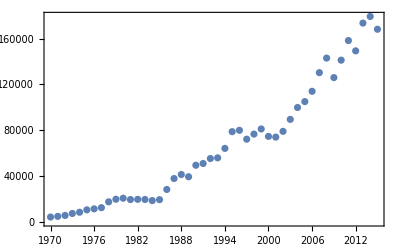

```mathematica
DateListPlot[
CountryData["Liechtenstein", {"GDPPerCapita", All}],
Joined->False]
```

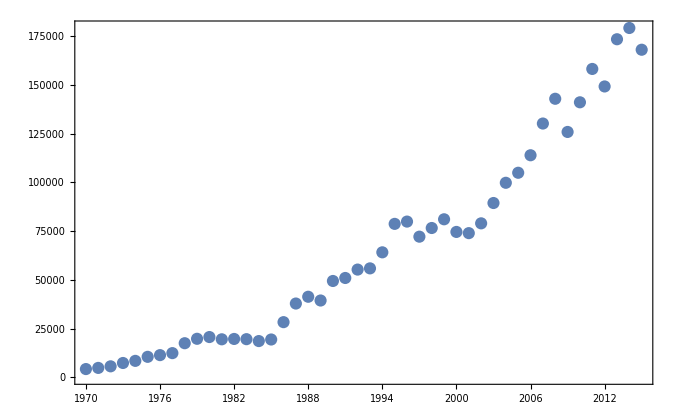

```mathematica
DateListPlot[
CountryData["Liechtenstein", {"GDPPerCapita", All}],
Joined->False]
```

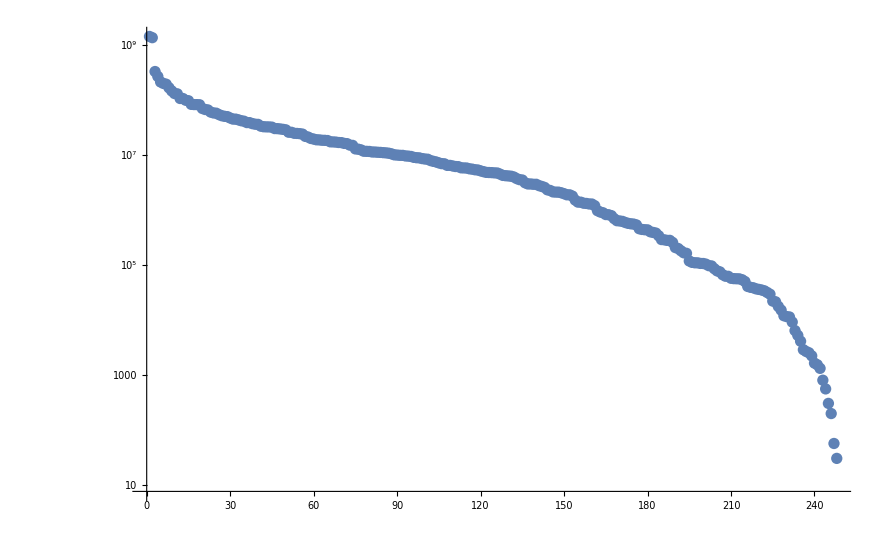

```mathematica
ListLogPlot[Reverse[Sort[CountryData[#,"Population"]&/@CountryData[]]]]
```

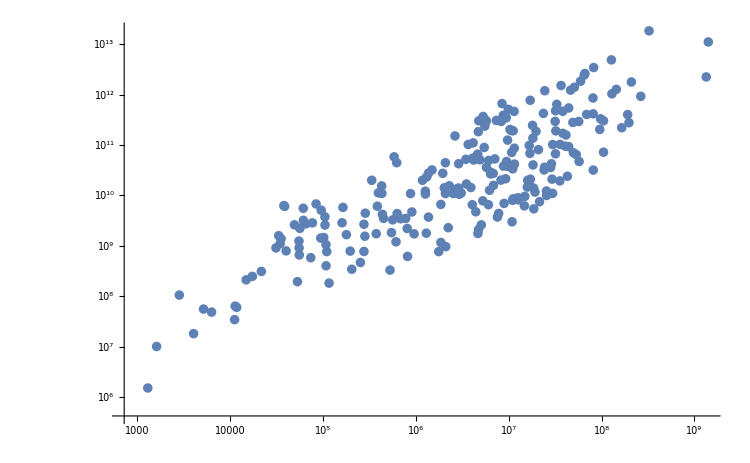

```mathematica
ListLogLogPlot[Tooltip[{CountryData[#,"Population"],CountryData[#,"GDP"]},CountryData[#,"Name"]]&/@CountryData["Countries"]]
```

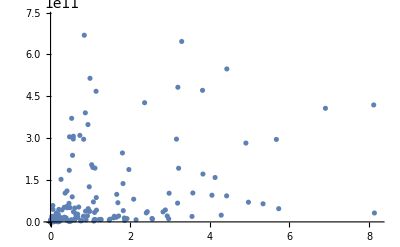

```mathematica
ListPlot[Tooltip[{CountryData[#,"Population"],CountryData[#,"GDP"]},CountryData[#,"Name"]]&/@CountryData["Countries"]]
```

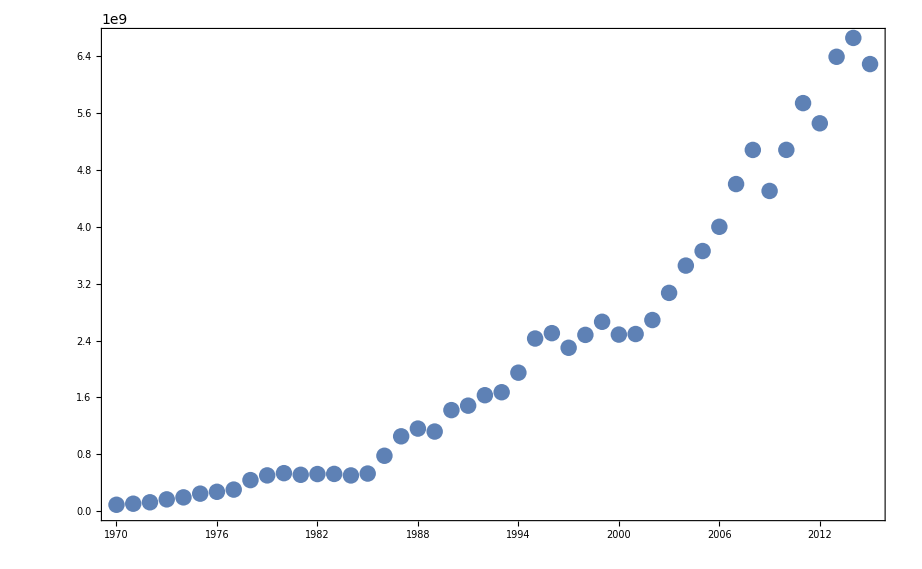

```mathematica
DateListPlot[
CountryData["Liechtenstein",{"GDP", All}],
Joined->False]
```

```mathematica
CountryData["Albania","LargestCities"]
```

{Tirana,Durres,Elbasan,Vlore,Shkoder,Fier,Korce,Berat,Lushnje,Kavaje,Pogradec,Lac,Gjirokaster,Patos,Kruje,Lezhe,Kucove,Kukes,Burrel,Sarande,Peshkopi,Cerrik,Shijak,Corovode,Librazhd,Tepelene,Gramsh,Bulqize,Kamze,Permet,Polican,Fushe-Kruje,Ballsh,Rreshen,Mamurras,Bajram Curri,Erseke,Peqin,Bilisht,Selenice,Roskovec,Puke,Rrogozhine,Vore,Memaliaj,Ure Vajgurore,Himare,Koplik,Perrenjas,Delvine,Maliq,Libohove,Krume,Shengjin,Leskovik,Orikum,Kelcyre,Fushe-Arrez,Rubik,Milot,Kurbnesh,Konispol,Kerrabe,Kraste,Fierze,Klos,Ulze}

```mathematica
CountryData["China","LargestCities"]
```

{Shanghai,Beijing,Zhoukou,Nanyang,Baoding,Chengdu,Linyi,Harbin,Tianjin,Shijiazhuang,Xuzhou,Handan,Heze,Shangqiu,Ganzhou,Zhumadian,Weifang,Xinyang,Wuhan,Jining,Yancheng,Guangzhou,Xian,Wenzhou,Shaoyang,Zhanjiang,Qingdao,Nantong,Changchun,Nanchong,Zunyi,Hengyang,Huanggang,Maoming,Tangshan,Zhengzhou,Shangrao,Xingtai,Cangzhou,Shenyang,Luan,Nanning,Luoyang,Hangzhou,Quanzhou,Jingzhou,Dazhou,Yulin,Yantai,Changsha,Jieyang,Fuzhou,Suzhou,Suzhou,Nanjing,Changde,Qujing,Anqing,Jinan,Xinxiang,Bozhou,Liaocheng,Xiangfan,Yongzhou,Dalian,Suihua,Taizhou,Anyang,Qiqihar,Ningbo,Dezhou,Zhaotong,Yueyang,Weinan,Taian,Yichun,Mianyang,Suqian,Yibin,Huaian,Kunming,Pingdingshan,Xiaogan,Kaifeng,Xianyang,Guilin,Shantou,Guigang,Huaihua,Meizhou,Taizhou,Yuncheng,Ziyang,Nanchang,Luzhou,Hefei,Jiujiang,Lianyungang,Xuchang,Chenzhou}

```mathematica
CityData[Entity["City",{"Shanghai","Shanghai","China"}], "Properties"]
```

{AlternateNames,Coordinates,Country,Elevation,FullName,Latitude,LocationLink,Longitude,Name,Population,Region,RegionName,StandardName,TimeZone}

```mathematica
Grid@
TakeLargestBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "Population"]}&,
CountryData[]]
,Last,30]
```

Power::infy: Infinite expression 1/0 encountered.

Quantity::compatu: Incompatible units.

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

$Aborted[]

```mathematica
Grid@
TakeLargestBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last,30]
```

Quantity::compatu: Incompatible units.

Grid[TakeLargestBy[{{Afghanistan,29849.9 $},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Albania,433019. $},{Algeria,66778.5 $},{American Samoa,3.30653×10^6 $},{Andorra,6.10794×10^6 $},{Angola,82331.8 $},{Anguilla,2.3206×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Argentina,200262. $},{Armenia,374864. $},{Aruba,1.43581×10^7 $},{Australia,156804. $},{Austria,4.74013×10^6 $},{Azerbaijan,458044. $},{Bahamas,1.12505×10^6 $},{Bahrain,4.23409×10^7 $},{Bangladesh,1.701×10^6 $},{Barbados,1.03512×10^7 $},{Belarus,233648. $},{Belgium,1.54553×10^7 $},{Belize,76343.9 $},{Benin,77588.8 $},{Bermuda,1.03217×10^8 $},{Bhutan,57629.8 $},{Bolivia,31206.8 $},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Bosnia and Herzegovina,330363. $},{Botswana,27493.1 $},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Brazil,212330. $},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{British Virgin Islands,6.02112×10^6 $},{Brunei,2.94246×10^6 $},{Bulgaria,490721. $},{Burkina Faso,42707.2 $},{Burundi,117096. $},{Cambodia,113400. $},{Cameroon,68154.9 $},{Canada,168226. $},{Cape Verde,453018. $},{Cayman Islands,1.21479×10^7 $},{Central African Republic,2818.89 $},{Chad,7624.49 $},{Chile,332111. $},{China,1.2008×10^6 $},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Colombia,271939. $},{Comoros,275908. $},{Cook Islands,1.04983×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Cuba,793415. $},{Curacao,6.46622×10^6 $},{Cyprus,2.16936×10^6 $},{Czech Republic,2.52832×10^6 $},{Democratic Republic of the Congo,14084.8 $},{Denmark,7.2324×10^6 $},{Djibouti,74503.9 $},{Dominica,774280. $},{Dominican Republic,1.48145×10^6 $},{East Timor,119872. $},{Ecuador,356212. $},{Egypt,334312. $},{El Salvador,1.29325×10^6 $},{Equatorial Guinea,380906. $},{Eritrea,25819.2 $},{Estonia,550578. $},{Ethiopia,64638.1 $},{Falkland Islands,8633.86 $},{Faroe Islands,1.87614×10^6 $},{Fiji,257395. $},{Finland,785027. $},{France,4.48289×10^6 $},{French Guiana,17397.6 $},{French Polynesia,900847. $},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Gabon,55162.5 $},{Gambia,96459.9 $},{Gaza Strip,2.13333×10^6 $},{Georgia,206284. $},{Germany,9.97441×10^6 $},{Ghana,187620. $},{Gibraltar,1.70154×10^8 $},{Greece,1.47317×10^6 $},{Greenland,1025.07 $},{Grenada,3.07032×10^6 $},{Guadeloupe,2.0592×10^6 $},{Guam,1.06489×10^7 $},{Guatemala,641694. $},{Guernsey,3.51538×10^7 $},{Guinea,33372.7 $},{Guinea-Bissau,41427.6 $},{Guyana,17792.3 $},{Haiti,291097. $},{Honduras,192304. $},{Hong Kong,2.9405×10^8 $},{Hungary,1.40408×10^6 $},{Iceland,199974. $},{India,761401. $},{Indonesia,514614. $},{Iran,256098. $},{Iraq,396816. $},{Ireland,4.42517×10^6 $},{Isle of Man,1.18749×10^7 $},{Israel,1.45635×10^7 $},{Italy,6.31982×10^6 $},{Ivory Coast,114378. $},{Jamaica,1.29784×10^6 $},{Japan,1.31828×10^7 $},{Jersey,4.39655×10^7 $},{Jordan,435291. $},{Kazakhstan,50849.5 $},{Kenya,123922. $},{Kiribati,223861. $},{Kosovo,610810. $},{Kuwait,6.22267×10^6 $},{Kyrgyzstan,34156.7 $},{Laos,68905.2 $},{Latvia,442942. $},{Lebanon,4.82385×10^6 $},{Lesotho,75484.2 $},{Liberia,21812.7 $},{Libya,16568.4 $},{Liechtenstein,3.93073×10^7 $},{Lithuania,681858. $},{Luxembourg,2.26726×10^7 $},{Macau,1.58875×10^9 $},{Macedonia,428561. $},{Madagascar,17197.8 $},{Malawi,57749.1 $},{Malaysia,902266. $},{Maldives,1.41752×10^7 $},{Mali,11502.3 $},{Malta,3.48071×10^7 $},{Marshall Islands,1.07457×10^6 $},{Martinique,5.77075×10^6 $},{Mauritania,4598.14 $},{Mauritius,5.9943×10^6 $},{Mayotte,1.24813×10^6 $},{Mexico,538556. $},{Micronesia,469937. $},{Moldova,199178. $},{Monaco,3.03744×10^9 $},{Mongolia,7198.62 $},{Montenegro,325166. $},{Montserrat,543527. $},{Morocco,232145. $},{Mozambique,14007. $},{Myanmar,99257.4 $},{Namibia,13297.7 $},{Nauru,3.02282×10^6 $},{Nepal,147414. $},{Netherlands,2.29318×10^7 $},{New Caledonia,146777. $},{New Zealand,690129. $},{Nicaragua,105780. $},{Niger,5943.31 $},{Nigeria,444298. $},{Niue,38500. $},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Northern Mariana Islands,2.67672×10^6 $},{North Korea,101971. $},{Norway,1.21951×10^6 $},{Oman,214195. $},{Pakistan,361814. $},{Palau,675922. $},{Panama,742369. $},{Papua New Guinea,44634.6 $},{Paraguay,69025.8 $},{Peru,150162. $},{Philippines,1.02259×10^6 $},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Poland,1.54924×10^6 $},{Portugal,2.23939×10^6 $},{Puerto Rico,1.16274×10^7 $},{Qatar,1.31583×10^7 $},{Republic of the Congo,22938.5 $},{Réunion,4.34783×10^6 $},{Romania,816004. $},{Russia,78348. $},{Rwanda,339551. $},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Saint Kitts and Nevis,3.48603×10^6 $},{Saint Lucia,2.75095×10^6 $},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Saint Pierre and Miquelon,199587. $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Samoa,278751. $},{San Marino,2.60772×10^7 $},{São Tomé and Príncipe,355583. $},{Saudi Arabia,329718. $},{Senegal,76267.1 $},{Serbia,494358. $},{Seychelles,3.13698×10^6 $},{Sierra Leone,52172.4 $},{Singapore,4.32279×10^8 $},{Sint Maarten,2.33353×10^7 $},{Slovakia,1.8661×10^6 $},{Slovenia,2.21868×10^6 $},{Solomon Islands,42954.5 $},{Somalia,9910.14 $},{South Africa,243280. $},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{South Korea,1.43726×10^7 $},{South Sudan,15341.4 $},{Spain,2.47957×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sudan,53448.1 $},{Suriname,21015.5 $},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Eswatini,216267. $},{Sweden,1.25376×10^6 $},{Switzerland,1.67225×10^7 $},{Syria,220035. $},{Taiwan,1.32362×10^7 $},{Tajikistan,49124.8 $},{Tanzania,53443.3 $},{Thailand,796700. $},{Togo,80904.6 $},{Tokelau,125000. $},{Tonga,560059. $},{Trinidad and Tobago,5.42234×10^6 $},{Tunisia,270742. $},{Turkey,1.12224×10^6 $},{Turkmenistan,76989.9 $},{Turks and Caicos Islands,1.45647×10^6 $},{Tuvalu,1.31611×10^6 $},{Uganda,120569. $},{Ukraine,160997. $},{United Arab Emirates,4.17157×10^6 $},{United Kingdom,1.09449×10^7 $},{United States,2.03281×10^6 $},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{United States Virgin Islands,1.08815×10^7 $},{Uruguay,299516. $},{Uzbekistan,158017. $},{Vanuatu,63459.1 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Venezuela,546862. $},{Vietnam,630920. $},{Wallis and Futuna Islands,422535. $},{West Bank,2.37537×10^6 $},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Yemen,68099.8 $},{Zambia,28334.7 $},{Zimbabwe,42962.6 $}},Last,30]]

```mathematica
Grid@
TakeLargestBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last,10]
```

Quantity::compatu: Incompatible units.

Grid[TakeLargestBy[{{Afghanistan,29849.9 $},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Albania,433019. $},{Algeria,66778.5 $},{American Samoa,3.30653×10^6 $},{Andorra,6.10794×10^6 $},{Angola,82331.8 $},{Anguilla,2.3206×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Argentina,200262. $},{Armenia,374864. $},{Aruba,1.43581×10^7 $},{Australia,156804. $},{Austria,4.74013×10^6 $},{Azerbaijan,458044. $},{Bahamas,1.12505×10^6 $},{Bahrain,4.23409×10^7 $},{Bangladesh,1.701×10^6 $},{Barbados,1.03512×10^7 $},{Belarus,233648. $},{Belgium,1.54553×10^7 $},{Belize,76343.9 $},{Benin,77588.8 $},{Bermuda,1.03217×10^8 $},{Bhutan,57629.8 $},{Bolivia,31206.8 $},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Bosnia and Herzegovina,330363. $},{Botswana,27493.1 $},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Brazil,212330. $},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{British Virgin Islands,6.02112×10^6 $},{Brunei,2.94246×10^6 $},{Bulgaria,490721. $},{Burkina Faso,42707.2 $},{Burundi,117096. $},{Cambodia,113400. $},{Cameroon,68154.9 $},{Canada,168226. $},{Cape Verde,453018. $},{Cayman Islands,1.21479×10^7 $},{Central African Republic,2818.89 $},{Chad,7624.49 $},{Chile,332111. $},{China,1.2008×10^6 $},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Colombia,271939. $},{Comoros,275908. $},{Cook Islands,1.04983×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Cuba,793415. $},{Curacao,6.46622×10^6 $},{Cyprus,2.16936×10^6 $},{Czech Republic,2.52832×10^6 $},{Democratic Republic of the Congo,14084.8 $},{Denmark,7.2324×10^6 $},{Djibouti,74503.9 $},{Dominica,774280. $},{Dominican Republic,1.48145×10^6 $},{East Timor,119872. $},{Ecuador,356212. $},{Egypt,334312. $},{El Salvador,1.29325×10^6 $},{Equatorial Guinea,380906. $},{Eritrea,25819.2 $},{Estonia,550578. $},{Ethiopia,64638.1 $},{Falkland Islands,8633.86 $},{Faroe Islands,1.87614×10^6 $},{Fiji,257395. $},{Finland,785027. $},{France,4.48289×10^6 $},{French Guiana,17397.6 $},{French Polynesia,900847. $},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Gabon,55162.5 $},{Gambia,96459.9 $},{Gaza Strip,2.13333×10^6 $},{Georgia,206284. $},{Germany,9.97441×10^6 $},{Ghana,187620. $},{Gibraltar,1.70154×10^8 $},{Greece,1.47317×10^6 $},{Greenland,1025.07 $},{Grenada,3.07032×10^6 $},{Guadeloupe,2.0592×10^6 $},{Guam,1.06489×10^7 $},{Guatemala,641694. $},{Guernsey,3.51538×10^7 $},{Guinea,33372.7 $},{Guinea-Bissau,41427.6 $},{Guyana,17792.3 $},{Haiti,291097. $},{Honduras,192304. $},{Hong Kong,2.9405×10^8 $},{Hungary,1.40408×10^6 $},{Iceland,199974. $},{India,761401. $},{Indonesia,514614. $},{Iran,256098. $},{Iraq,396816. $},{Ireland,4.42517×10^6 $},{Isle of Man,1.18749×10^7 $},{Israel,1.45635×10^7 $},{Italy,6.31982×10^6 $},{Ivory Coast,114378. $},{Jamaica,1.29784×10^6 $},{Japan,1.31828×10^7 $},{Jersey,4.39655×10^7 $},{Jordan,435291. $},{Kazakhstan,50849.5 $},{Kenya,123922. $},{Kiribati,223861. $},{Kosovo,610810. $},{Kuwait,6.22267×10^6 $},{Kyrgyzstan,34156.7 $},{Laos,68905.2 $},{Latvia,442942. $},{Lebanon,4.82385×10^6 $},{Lesotho,75484.2 $},{Liberia,21812.7 $},{Libya,16568.4 $},{Liechtenstein,3.93073×10^7 $},{Lithuania,681858. $},{Luxembourg,2.26726×10^7 $},{Macau,1.58875×10^9 $},{Macedonia,428561. $},{Madagascar,17197.8 $},{Malawi,57749.1 $},{Malaysia,902266. $},{Maldives,1.41752×10^7 $},{Mali,11502.3 $},{Malta,3.48071×10^7 $},{Marshall Islands,1.07457×10^6 $},{Martinique,5.77075×10^6 $},{Mauritania,4598.14 $},{Mauritius,5.9943×10^6 $},{Mayotte,1.24813×10^6 $},{Mexico,538556. $},{Micronesia,469937. $},{Moldova,199178. $},{Monaco,3.03744×10^9 $},{Mongolia,7198.62 $},{Montenegro,325166. $},{Montserrat,543527. $},{Morocco,232145. $},{Mozambique,14007. $},{Myanmar,99257.4 $},{Namibia,13297.7 $},{Nauru,3.02282×10^6 $},{Nepal,147414. $},{Netherlands,2.29318×10^7 $},{New Caledonia,146777. $},{New Zealand,690129. $},{Nicaragua,105780. $},{Niger,5943.31 $},{Nigeria,444298. $},{Niue,38500. $},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Northern Mariana Islands,2.67672×10^6 $},{North Korea,101971. $},{Norway,1.21951×10^6 $},{Oman,214195. $},{Pakistan,361814. $},{Palau,675922. $},{Panama,742369. $},{Papua New Guinea,44634.6 $},{Paraguay,69025.8 $},{Peru,150162. $},{Philippines,1.02259×10^6 $},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Poland,1.54924×10^6 $},{Portugal,2.23939×10^6 $},{Puerto Rico,1.16274×10^7 $},{Qatar,1.31583×10^7 $},{Republic of the Congo,22938.5 $},{Réunion,4.34783×10^6 $},{Romania,816004. $},{Russia,78348. $},{Rwanda,339551. $},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Saint Kitts and Nevis,3.48603×10^6 $},{Saint Lucia,2.75095×10^6 $},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Saint Pierre and Miquelon,199587. $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Samoa,278751. $},{San Marino,2.60772×10^7 $},{São Tomé and Príncipe,355583. $},{Saudi Arabia,329718. $},{Senegal,76267.1 $},{Serbia,494358. $},{Seychelles,3.13698×10^6 $},{Sierra Leone,52172.4 $},{Singapore,4.32279×10^8 $},{Sint Maarten,2.33353×10^7 $},{Slovakia,1.8661×10^6 $},{Slovenia,2.21868×10^6 $},{Solomon Islands,42954.5 $},{Somalia,9910.14 $},{South Africa,243280. $},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{South Korea,1.43726×10^7 $},{South Sudan,15341.4 $},{Spain,2.47957×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sudan,53448.1 $},{Suriname,21015.5 $},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Eswatini,216267. $},{Sweden,1.25376×10^6 $},{Switzerland,1.67225×10^7 $},{Syria,220035. $},{Taiwan,1.32362×10^7 $},{Tajikistan,49124.8 $},{Tanzania,53443.3 $},{Thailand,796700. $},{Togo,80904.6 $},{Tokelau,125000. $},{Tonga,560059. $},{Trinidad and Tobago,5.42234×10^6 $},{Tunisia,270742. $},{Turkey,1.12224×10^6 $},{Turkmenistan,76989.9 $},{Turks and Caicos Islands,1.45647×10^6 $},{Tuvalu,1.31611×10^6 $},{Uganda,120569. $},{Ukraine,160997. $},{United Arab Emirates,4.17157×10^6 $},{United Kingdom,1.09449×10^7 $},{United States,2.03281×10^6 $},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{United States Virgin Islands,1.08815×10^7 $},{Uruguay,299516. $},{Uzbekistan,158017. $},{Vanuatu,63459.1 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Venezuela,546862. $},{Vietnam,630920. $},{Wallis and Futuna Islands,422535. $},{West Bank,2.37537×10^6 $},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Yemen,68099.8 $},{Zambia,28334.7 $},{Zimbabwe,42962.6 $}},Last,10]]

```mathematica
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
```

{{Afghanistan,29849.9 $},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Albania,433019. $},{Algeria,66778.5 $},{American Samoa,3.30653×10^6 $},{Andorra,6.10794×10^6 $},{Angola,82331.8 $},{Anguilla,2.3206×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Argentina,200262. $},{Armenia,374864. $},{Aruba,1.43581×10^7 $},{Australia,156804. $},{Austria,4.74013×10^6 $},{Azerbaijan,458044. $},{Bahamas,1.12505×10^6 $},{Bahrain,4.23409×10^7 $},{Bangladesh,1.701×10^6 $},{Barbados,1.03512×10^7 $},{Belarus,233648. $},{Belgium,1.54553×10^7 $},{Belize,76343.9 $},{Benin,77588.8 $},{Bermuda,1.03217×10^8 $},{Bhutan,57629.8 $},{Bolivia,31206.8 $},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Bosnia and Herzegovina,330363. $},{Botswana,27493.1 $},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Brazil,212330. $},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{British Virgin Islands,6.02112×10^6 $},{Brunei,2.94246×10^6 $},{Bulgaria,490721. $},{Burkina Faso,42707.2 $},{Burundi,117096. $},{Cambodia,113400. $},{Cameroon,68154.9 $},{Canada,168226. $},{Cape Verde,453018. $},{Cayman Islands,1.21479×10^7 $},{Central African Republic,2818.89 $},{Chad,7624.49 $},{Chile,332111. $},{China,1.2008×10^6 $},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Colombia,271939. $},{Comoros,275908. $},{Cook Islands,1.04983×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Cuba,793415. $},{Curacao,6.46622×10^6 $},{Cyprus,2.16936×10^6 $},{Czech Republic,2.52832×10^6 $},{Democratic Republic of the Congo,14084.8 $},{Denmark,7.2324×10^6 $},{Djibouti,74503.9 $},{Dominica,774280. $},{Dominican Republic,1.48145×10^6 $},{East Timor,119872. $},{Ecuador,356212. $},{Egypt,334312. $},{El Salvador,1.29325×10^6 $},{Equatorial Guinea,380906. $},{Eritrea,25819.2 $},{Estonia,550578. $},{Ethiopia,64638.1 $},{Falkland Islands,8633.86 $},{Faroe Islands,1.87614×10^6 $},{Fiji,257395. $},{Finland,785027. $},{France,4.48289×10^6 $},{French Guiana,17397.6 $},{French Polynesia,900847. $},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Gabon,55162.5 $},{Gambia,96459.9 $},{Gaza Strip,2.13333×10^6 $},{Georgia,206284. $},{Germany,9.97441×10^6 $},{Ghana,187620. $},{Gibraltar,1.70154×10^8 $},{Greece,1.47317×10^6 $},{Greenland,1025.07 $},{Grenada,3.07032×10^6 $},{Guadeloupe,2.0592×10^6 $},{Guam,1.06489×10^7 $},{Guatemala,641694. $},{Guernsey,3.51538×10^7 $},{Guinea,33372.7 $},{Guinea-Bissau,41427.6 $},{Guyana,17792.3 $},{Haiti,291097. $},{Honduras,192304. $},{Hong Kong,2.9405×10^8 $},{Hungary,1.40408×10^6 $},{Iceland,199974. $},{India,761401. $},{Indonesia,514614. $},{Iran,256098. $},{Iraq,396816. $},{Ireland,4.42517×10^6 $},{Isle of Man,1.18749×10^7 $},{Israel,1.45635×10^7 $},{Italy,6.31982×10^6 $},{Ivory Coast,114378. $},{Jamaica,1.29784×10^6 $},{Japan,1.31828×10^7 $},{Jersey,4.39655×10^7 $},{Jordan,435291. $},{Kazakhstan,50849.5 $},{Kenya,123922. $},{Kiribati,223861. $},{Kosovo,610810. $},{Kuwait,6.22267×10^6 $},{Kyrgyzstan,34156.7 $},{Laos,68905.2 $},{Latvia,442942. $},{Lebanon,4.82385×10^6 $},{Lesotho,75484.2 $},{Liberia,21812.7 $},{Libya,16568.4 $},{Liechtenstein,3.93073×10^7 $},{Lithuania,681858. $},{Luxembourg,2.26726×10^7 $},{Macau,1.58875×10^9 $},{Macedonia,428561. $},{Madagascar,17197.8 $},{Malawi,57749.1 $},{Malaysia,902266. $},{Maldives,1.41752×10^7 $},{Mali,11502.3 $},{Malta,3.48071×10^7 $},{Marshall Islands,1.07457×10^6 $},{Martinique,5.77075×10^6 $},{Mauritania,4598.14 $},{Mauritius,5.9943×10^6 $},{Mayotte,1.24813×10^6 $},{Mexico,538556. $},{Micronesia,469937. $},{Moldova,199178. $},{Monaco,3.03744×10^9 $},{Mongolia,7198.62 $},{Montenegro,325166. $},{Montserrat,543527. $},{Morocco,232145. $},{Mozambique,14007. $},{Myanmar,99257.4 $},{Namibia,13297.7 $},{Nauru,3.02282×10^6 $},{Nepal,147414. $},{Netherlands,2.29318×10^7 $},{New Caledonia,146777. $},{New Zealand,690129. $},{Nicaragua,105780. $},{Niger,5943.31 $},{Nigeria,444298. $},{Niue,38500. $},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Northern Mariana Islands,2.67672×10^6 $},{North Korea,101971. $},{Norway,1.21951×10^6 $},{Oman,214195. $},{Pakistan,361814. $},{Palau,675922. $},{Panama,742369. $},{Papua New Guinea,44634.6 $},{Paraguay,69025.8 $},{Peru,150162. $},{Philippines,1.02259×10^6 $},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Poland,1.54924×10^6 $},{Portugal,2.23939×10^6 $},{Puerto Rico,1.16274×10^7 $},{Qatar,1.31583×10^7 $},{Republic of the Congo,22938.5 $},{Réunion,4.34783×10^6 $},{Romania,816004. $},{Russia,78348. $},{Rwanda,339551. $},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Saint Kitts and Nevis,3.48603×10^6 $},{Saint Lucia,2.75095×10^6 $},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Saint Pierre and Miquelon,199587. $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Samoa,278751. $},{San Marino,2.60772×10^7 $},{São Tomé and Príncipe,355583. $},{Saudi Arabia,329718. $},{Senegal,76267.1 $},{Serbia,494358. $},{Seychelles,3.13698×10^6 $},{Sierra Leone,52172.4 $},{Singapore,4.32279×10^8 $},{Sint Maarten,2.33353×10^7 $},{Slovakia,1.8661×10^6 $},{Slovenia,2.21868×10^6 $},{Solomon Islands,42954.5 $},{Somalia,9910.14 $},{South Africa,243280. $},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{South Korea,1.43726×10^7 $},{South Sudan,15341.4 $},{Spain,2.47957×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sudan,53448.1 $},{Suriname,21015.5 $},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Eswatini,216267. $},{Sweden,1.25376×10^6 $},{Switzerland,1.67225×10^7 $},{Syria,220035. $},{Taiwan,1.32362×10^7 $},{Tajikistan,49124.8 $},{Tanzania,53443.3 $},{Thailand,796700. $},{Togo,80904.6 $},{Tokelau,125000. $},{Tonga,560059. $},{Trinidad and Tobago,5.42234×10^6 $},{Tunisia,270742. $},{Turkey,1.12224×10^6 $},{Turkmenistan,76989.9 $},{Turks and Caicos Islands,1.45647×10^6 $},{Tuvalu,1.31611×10^6 $},{Uganda,120569. $},{Ukraine,160997. $},{United Arab Emirates,4.17157×10^6 $},{United Kingdom,1.09449×10^7 $},{United States,2.03281×10^6 $},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{United States Virgin Islands,1.08815×10^7 $},{Uruguay,299516. $},{Uzbekistan,158017. $},{Vanuatu,63459.1 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Venezuela,546862. $},{Vietnam,630920. $},{Wallis and Futuna Islands,422535. $},{West Bank,2.37537×10^6 $},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Yemen,68099.8 $},{Zambia,28334.7 $},{Zimbabwe,42962.6 $}}

```mathematica
SortBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last]
```

{{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Greenland,1025.07 $},{Central African Republic,2818.89 $},{Mauritania,4598.14 $},{Niger,5943.31 $},{Mongolia,7198.62 $},{Chad,7624.49 $},{Falkland Islands,8633.86 $},{Somalia,9910.14 $},{Mali,11502.3 $},{Namibia,13297.7 $},{Mozambique,14007. $},{Democratic Republic of the Congo,14084.8 $},{South Sudan,15341.4 $},{Libya,16568.4 $},{Madagascar,17197.8 $},{French Guiana,17397.6 $},{Guyana,17792.3 $},{Suriname,21015.5 $},{Liberia,21812.7 $},{Republic of the Congo,22938.5 $},{Eritrea,25819.2 $},{Botswana,27493.1 $},{Zambia,28334.7 $},{Afghanistan,29849.9 $},{Bolivia,31206.8 $},{Guinea,33372.7 $},{Kyrgyzstan,34156.7 $},{Niue,38500. $},{Guinea-Bissau,41427.6 $},{Burkina Faso,42707.2 $},{Solomon Islands,42954.5 $},{Zimbabwe,42962.6 $},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Papua New Guinea,44634.6 $},{Tajikistan,49124.8 $},{Kazakhstan,50849.5 $},{Sierra Leone,52172.4 $},{Tanzania,53443.3 $},{Sudan,53448.1 $},{Gabon,55162.5 $},{Bhutan,57629.8 $},{Malawi,57749.1 $},{Vanuatu,63459.1 $},{Ethiopia,64638.1 $},{Algeria,66778.5 $},{Yemen,68099.8 $},{Cameroon,68154.9 $},{Laos,68905.2 $},{Paraguay,69025.8 $},{Djibouti,74503.9 $},{Lesotho,75484.2 $},{Senegal,76267.1 $},{Belize,76343.9 $},{Turkmenistan,76989.9 $},{Benin,77588.8 $},{Russia,78348. $},{Togo,80904.6 $},{Angola,82331.8 $},{Gambia,96459.9 $},{Myanmar,99257.4 $},{North Korea,101971. $},{Nicaragua,105780. $},{Cambodia,113400. $},{Ivory Coast,114378. $},{Burundi,117096. $},{East Timor,119872. $},{Uganda,120569. $},{Kenya,123922. $},{Tokelau,125000. $},{New Caledonia,146777. $},{Nepal,147414. $},{Peru,150162. $},{Australia,156804. $},{Uzbekistan,158017. $},{Ukraine,160997. $},{Canada,168226. $},{Ghana,187620. $},{Honduras,192304. $},{Moldova,199178. $},{Saint Pierre and Miquelon,199587. $},{Iceland,199974. $},{Argentina,200262. $},{Georgia,206284. $},{Brazil,212330. $},{Oman,214195. $},{Eswatini,216267. $},{Syria,220035. $},{Kiribati,223861. $},{Morocco,232145. $},{Belarus,233648. $},{South Africa,243280. $},{Iran,256098. $},{Fiji,257395. $},{Tunisia,270742. $},{Colombia,271939. $},{Comoros,275908. $},{Samoa,278751. $},{Haiti,291097. $},{Uruguay,299516. $},{Montenegro,325166. $},{Saudi Arabia,329718. $},{Bosnia and Herzegovina,330363. $},{Chile,332111. $},{Egypt,334312. $},{Rwanda,339551. $},{São Tomé and Príncipe,355583. $},{Ecuador,356212. $},{Pakistan,361814. $},{Armenia,374864. $},{Equatorial Guinea,380906. $},{Iraq,396816. $},{Wallis and Futuna Islands,422535. $},{Macedonia,428561. $},{Albania,433019. $},{Jordan,435291. $},{Latvia,442942. $},{Nigeria,444298. $},{Cape Verde,453018. $},{Azerbaijan,458044. $},{Micronesia,469937. $},{Bulgaria,490721. $},{Serbia,494358. $},{Indonesia,514614. $},{Mexico,538556. $},{Montserrat,543527. $},{Venezuela,546862. $},{Estonia,550578. $},{Tonga,560059. $},{Kosovo,610810. $},{Vietnam,630920. $},{Guatemala,641694. $},{Palau,675922. $},{Lithuania,681858. $},{New Zealand,690129. $},{Panama,742369. $},{India,761401. $},{Dominica,774280. $},{Finland,785027. $},{Cuba,793415. $},{Thailand,796700. $},{Romania,816004. $},{French Polynesia,900847. $},{Malaysia,902266. $},{Croatia,906045. $},{Costa Rica,1.00091×10^6 $},{Philippines,1.02259×10^6 $},{Cook Islands,1.04983×10^6 $},{Marshall Islands,1.07457×10^6 $},{Turkey,1.12224×10^6 $},{Bahamas,1.12505×10^6 $},{China,1.2008×10^6 $},{Norway,1.21951×10^6 $},{Mayotte,1.24813×10^6 $},{Sweden,1.25376×10^6 $},{Sri Lanka,1.25827×10^6 $},{El Salvador,1.29325×10^6 $},{Jamaica,1.29784×10^6 $},{Tuvalu,1.31611×10^6 $},{Hungary,1.40408×10^6 $},{Turks and Caicos Islands,1.45647×10^6 $},{Greece,1.47317×10^6 $},{Dominican Republic,1.48145×10^6 $},{Poland,1.54924×10^6 $},{Bangladesh,1.701×10^6 $},{Slovakia,1.8661×10^6 $},{Faroe Islands,1.87614×10^6 $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{United States,2.03281×10^6 $},{Guadeloupe,2.0592×10^6 $},{Gaza Strip,2.13333×10^6 $},{Cyprus,2.16936×10^6 $},{Slovenia,2.21868×10^6 $},{Portugal,2.23939×10^6 $},{Anguilla,2.3206×10^6 $},{West Bank,2.37537×10^6 $},{Spain,2.47957×10^6 $},{Czech Republic,2.52832×10^6 $},{Northern Mariana Islands,2.67672×10^6 $},{Saint Lucia,2.75095×10^6 $},{Brunei,2.94246×10^6 $},{Nauru,3.02282×10^6 $},{Grenada,3.07032×10^6 $},{Seychelles,3.13698×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{American Samoa,3.30653×10^6 $},{Saint Kitts and Nevis,3.48603×10^6 $},{United Arab Emirates,4.17157×10^6 $},{Réunion,4.34783×10^6 $},{Ireland,4.42517×10^6 $},{France,4.48289×10^6 $},{Austria,4.74013×10^6 $},{Lebanon,4.82385×10^6 $},{Trinidad and Tobago,5.42234×10^6 $},{Martinique,5.77075×10^6 $},{Mauritius,5.9943×10^6 $},{British Virgin Islands,6.02112×10^6 $},{Andorra,6.10794×10^6 $},{Kuwait,6.22267×10^6 $},{Italy,6.31982×10^6 $},{Curacao,6.46622×10^6 $},{Denmark,7.2324×10^6 $},{Germany,9.97441×10^6 $},{Barbados,1.03512×10^7 $},{Guam,1.06489×10^7 $},{United States Virgin Islands,1.08815×10^7 $},{United Kingdom,1.09449×10^7 $},{Puerto Rico,1.16274×10^7 $},{Isle of Man,1.18749×10^7 $},{Cayman Islands,1.21479×10^7 $},{Qatar,1.31583×10^7 $},{Japan,1.31828×10^7 $},{Taiwan,1.32362×10^7 $},{Maldives,1.41752×10^7 $},{Aruba,1.43581×10^7 $},{South Korea,1.43726×10^7 $},{Israel,1.45635×10^7 $},{Belgium,1.54553×10^7 $},{Switzerland,1.67225×10^7 $},{Luxembourg,2.26726×10^7 $},{Netherlands,2.29318×10^7 $},{Sint Maarten,2.33353×10^7 $},{San Marino,2.60772×10^7 $},{Malta,3.48071×10^7 $},{Guernsey,3.51538×10^7 $},{Liechtenstein,3.93073×10^7 $},{Bahrain,4.23409×10^7 $},{Jersey,4.39655×10^7 $},{Bermuda,1.03217×10^8 $},{Gibraltar,1.70154×10^8 $},{Hong Kong,2.9405×10^8 $},{Singapore,4.32279×10^8 $},{Macau,1.58875×10^9 $},{Monaco,3.03744×10^9 $}}

```mathematica
TakeLargestBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last, 10]
```

Quantity::compatu: Incompatible units.

TakeLargestBy[{{Afghanistan,29849.9 $},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Albania,433019. $},{Algeria,66778.5 $},{American Samoa,3.30653×10^6 $},{Andorra,6.10794×10^6 $},{Angola,82331.8 $},{Anguilla,2.3206×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Argentina,200262. $},{Armenia,374864. $},{Aruba,1.43581×10^7 $},{Australia,156804. $},{Austria,4.74013×10^6 $},{Azerbaijan,458044. $},{Bahamas,1.12505×10^6 $},{Bahrain,4.23409×10^7 $},{Bangladesh,1.701×10^6 $},{Barbados,1.03512×10^7 $},{Belarus,233648. $},{Belgium,1.54553×10^7 $},{Belize,76343.9 $},{Benin,77588.8 $},{Bermuda,1.03217×10^8 $},{Bhutan,57629.8 $},{Bolivia,31206.8 $},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Bosnia and Herzegovina,330363. $},{Botswana,27493.1 $},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Brazil,212330. $},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{British Virgin Islands,6.02112×10^6 $},{Brunei,2.94246×10^6 $},{Bulgaria,490721. $},{Burkina Faso,42707.2 $},{Burundi,117096. $},{Cambodia,113400. $},{Cameroon,68154.9 $},{Canada,168226. $},{Cape Verde,453018. $},{Cayman Islands,1.21479×10^7 $},{Central African Republic,2818.89 $},{Chad,7624.49 $},{Chile,332111. $},{China,1.2008×10^6 $},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Colombia,271939. $},{Comoros,275908. $},{Cook Islands,1.04983×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Cuba,793415. $},{Curacao,6.46622×10^6 $},{Cyprus,2.16936×10^6 $},{Czech Republic,2.52832×10^6 $},{Democratic Republic of the Congo,14084.8 $},{Denmark,7.2324×10^6 $},{Djibouti,74503.9 $},{Dominica,774280. $},{Dominican Republic,1.48145×10^6 $},{East Timor,119872. $},{Ecuador,356212. $},{Egypt,334312. $},{El Salvador,1.29325×10^6 $},{Equatorial Guinea,380906. $},{Eritrea,25819.2 $},{Estonia,550578. $},{Ethiopia,64638.1 $},{Falkland Islands,8633.86 $},{Faroe Islands,1.87614×10^6 $},{Fiji,257395. $},{Finland,785027. $},{France,4.48289×10^6 $},{French Guiana,17397.6 $},{French Polynesia,900847. $},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Gabon,55162.5 $},{Gambia,96459.9 $},{Gaza Strip,2.13333×10^6 $},{Georgia,206284. $},{Germany,9.97441×10^6 $},{Ghana,187620. $},{Gibraltar,1.70154×10^8 $},{Greece,1.47317×10^6 $},{Greenland,1025.07 $},{Grenada,3.07032×10^6 $},{Guadeloupe,2.0592×10^6 $},{Guam,1.06489×10^7 $},{Guatemala,641694. $},{Guernsey,3.51538×10^7 $},{Guinea,33372.7 $},{Guinea-Bissau,41427.6 $},{Guyana,17792.3 $},{Haiti,291097. $},{Honduras,192304. $},{Hong Kong,2.9405×10^8 $},{Hungary,1.40408×10^6 $},{Iceland,199974. $},{India,761401. $},{Indonesia,514614. $},{Iran,256098. $},{Iraq,396816. $},{Ireland,4.42517×10^6 $},{Isle of Man,1.18749×10^7 $},{Israel,1.45635×10^7 $},{Italy,6.31982×10^6 $},{Ivory Coast,114378. $},{Jamaica,1.29784×10^6 $},{Japan,1.31828×10^7 $},{Jersey,4.39655×10^7 $},{Jordan,435291. $},{Kazakhstan,50849.5 $},{Kenya,123922. $},{Kiribati,223861. $},{Kosovo,610810. $},{Kuwait,6.22267×10^6 $},{Kyrgyzstan,34156.7 $},{Laos,68905.2 $},{Latvia,442942. $},{Lebanon,4.82385×10^6 $},{Lesotho,75484.2 $},{Liberia,21812.7 $},{Libya,16568.4 $},{Liechtenstein,3.93073×10^7 $},{Lithuania,681858. $},{Luxembourg,2.26726×10^7 $},{Macau,1.58875×10^9 $},{Macedonia,428561. $},{Madagascar,17197.8 $},{Malawi,57749.1 $},{Malaysia,902266. $},{Maldives,1.41752×10^7 $},{Mali,11502.3 $},{Malta,3.48071×10^7 $},{Marshall Islands,1.07457×10^6 $},{Martinique,5.77075×10^6 $},{Mauritania,4598.14 $},{Mauritius,5.9943×10^6 $},{Mayotte,1.24813×10^6 $},{Mexico,538556. $},{Micronesia,469937. $},{Moldova,199178. $},{Monaco,3.03744×10^9 $},{Mongolia,7198.62 $},{Montenegro,325166. $},{Montserrat,543527. $},{Morocco,232145. $},{Mozambique,14007. $},{Myanmar,99257.4 $},{Namibia,13297.7 $},{Nauru,3.02282×10^6 $},{Nepal,147414. $},{Netherlands,2.29318×10^7 $},{New Caledonia,146777. $},{New Zealand,690129. $},{Nicaragua,105780. $},{Niger,5943.31 $},{Nigeria,444298. $},{Niue,38500. $},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Northern Mariana Islands,2.67672×10^6 $},{North Korea,101971. $},{Norway,1.21951×10^6 $},{Oman,214195. $},{Pakistan,361814. $},{Palau,675922. $},{Panama,742369. $},{Papua New Guinea,44634.6 $},{Paraguay,69025.8 $},{Peru,150162. $},{Philippines,1.02259×10^6 $},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Poland,1.54924×10^6 $},{Portugal,2.23939×10^6 $},{Puerto Rico,1.16274×10^7 $},{Qatar,1.31583×10^7 $},{Republic of the Congo,22938.5 $},{Réunion,4.34783×10^6 $},{Romania,816004. $},{Russia,78348. $},{Rwanda,339551. $},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Saint Kitts and Nevis,3.48603×10^6 $},{Saint Lucia,2.75095×10^6 $},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Saint Pierre and Miquelon,199587. $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Samoa,278751. $},{San Marino,2.60772×10^7 $},{São Tomé and Príncipe,355583. $},{Saudi Arabia,329718. $},{Senegal,76267.1 $},{Serbia,494358. $},{Seychelles,3.13698×10^6 $},{Sierra Leone,52172.4 $},{Singapore,4.32279×10^8 $},{Sint Maarten,2.33353×10^7 $},{Slovakia,1.8661×10^6 $},{Slovenia,2.21868×10^6 $},{Solomon Islands,42954.5 $},{Somalia,9910.14 $},{South Africa,243280. $},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{South Korea,1.43726×10^7 $},{South Sudan,15341.4 $},{Spain,2.47957×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sudan,53448.1 $},{Suriname,21015.5 $},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Eswatini,216267. $},{Sweden,1.25376×10^6 $},{Switzerland,1.67225×10^7 $},{Syria,220035. $},{Taiwan,1.32362×10^7 $},{Tajikistan,49124.8 $},{Tanzania,53443.3 $},{Thailand,796700. $},{Togo,80904.6 $},{Tokelau,125000. $},{Tonga,560059. $},{Trinidad and Tobago,5.42234×10^6 $},{Tunisia,270742. $},{Turkey,1.12224×10^6 $},{Turkmenistan,76989.9 $},{Turks and Caicos Islands,1.45647×10^6 $},{Tuvalu,1.31611×10^6 $},{Uganda,120569. $},{Ukraine,160997. $},{United Arab Emirates,4.17157×10^6 $},{United Kingdom,1.09449×10^7 $},{United States,2.03281×10^6 $},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{United States Virgin Islands,1.08815×10^7 $},{Uruguay,299516. $},{Uzbekistan,158017. $},{Vanuatu,63459.1 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Venezuela,546862. $},{Vietnam,630920. $},{Wallis and Futuna Islands,422535. $},{West Bank,2.37537×10^6 $},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Yemen,68099.8 $},{Zambia,28334.7 $},{Zimbabwe,42962.6 $}},Last,10]

```mathematica
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
```

{{Afghanistan,29849.9 $},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{Albania,433019. $},{Algeria,66778.5 $},{American Samoa,3.30653×10^6 $},{Andorra,6.10794×10^6 $},{Angola,82331.8 $},{Anguilla,2.3206×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Argentina,200262. $},{Armenia,374864. $},{Aruba,1.43581×10^7 $},{Australia,156804. $},{Austria,4.74013×10^6 $},{Azerbaijan,458044. $},{Bahamas,1.12505×10^6 $},{Bahrain,4.23409×10^7 $},{Bangladesh,1.701×10^6 $},{Barbados,1.03512×10^7 $},{Belarus,233648. $},{Belgium,1.54553×10^7 $},{Belize,76343.9 $},{Benin,77588.8 $},{Bermuda,1.03217×10^8 $},{Bhutan,57629.8 $},{Bolivia,31206.8 $},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Bosnia and Herzegovina,330363. $},{Botswana,27493.1 $},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Brazil,212330. $},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{British Virgin Islands,6.02112×10^6 $},{Brunei,2.94246×10^6 $},{Bulgaria,490721. $},{Burkina Faso,42707.2 $},{Burundi,117096. $},{Cambodia,113400. $},{Cameroon,68154.9 $},{Canada,168226. $},{Cape Verde,453018. $},{Cayman Islands,1.21479×10^7 $},{Central African Republic,2818.89 $},{Chad,7624.49 $},{Chile,332111. $},{China,1.2008×10^6 $},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Colombia,271939. $},{Comoros,275908. $},{Cook Islands,1.04983×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Cuba,793415. $},{Curacao,6.46622×10^6 $},{Cyprus,2.16936×10^6 $},{Czech Republic,2.52832×10^6 $},{Democratic Republic of the Congo,14084.8 $},{Denmark,7.2324×10^6 $},{Djibouti,74503.9 $},{Dominica,774280. $},{Dominican Republic,1.48145×10^6 $},{East Timor,119872. $},{Ecuador,356212. $},{Egypt,334312. $},{El Salvador,1.29325×10^6 $},{Equatorial Guinea,380906. $},{Eritrea,25819.2 $},{Estonia,550578. $},{Ethiopia,64638.1 $},{Falkland Islands,8633.86 $},{Faroe Islands,1.87614×10^6 $},{Fiji,257395. $},{Finland,785027. $},{France,4.48289×10^6 $},{French Guiana,17397.6 $},{French Polynesia,900847. $},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)},{Gabon,55162.5 $},{Gambia,96459.9 $},{Gaza Strip,2.13333×10^6 $},{Georgia,206284. $},{Germany,9.97441×10^6 $},{Ghana,187620. $},{Gibraltar,1.70154×10^8 $},{Greece,1.47317×10^6 $},{Greenland,1025.07 $},{Grenada,3.07032×10^6 $},{Guadeloupe,2.0592×10^6 $},{Guam,1.06489×10^7 $},{Guatemala,641694. $},{Guernsey,3.51538×10^7 $},{Guinea,33372.7 $},{Guinea-Bissau,41427.6 $},{Guyana,17792.3 $},{Haiti,291097. $},{Honduras,192304. $},{Hong Kong,2.9405×10^8 $},{Hungary,1.40408×10^6 $},{Iceland,199974. $},{India,761401. $},{Indonesia,514614. $},{Iran,256098. $},{Iraq,396816. $},{Ireland,4.42517×10^6 $},{Isle of Man,1.18749×10^7 $},{Israel,1.45635×10^7 $},{Italy,6.31982×10^6 $},{Ivory Coast,114378. $},{Jamaica,1.29784×10^6 $},{Japan,1.31828×10^7 $},{Jersey,4.39655×10^7 $},{Jordan,435291. $},{Kazakhstan,50849.5 $},{Kenya,123922. $},{Kiribati,223861. $},{Kosovo,610810. $},{Kuwait,6.22267×10^6 $},{Kyrgyzstan,34156.7 $},{Laos,68905.2 $},{Latvia,442942. $},{Lebanon,4.82385×10^6 $},{Lesotho,75484.2 $},{Liberia,21812.7 $},{Libya,16568.4 $},{Liechtenstein,3.93073×10^7 $},{Lithuania,681858. $},{Luxembourg,2.26726×10^7 $},{Macau,1.58875×10^9 $},{Macedonia,428561. $},{Madagascar,17197.8 $},{Malawi,57749.1 $},{Malaysia,902266. $},{Maldives,1.41752×10^7 $},{Mali,11502.3 $},{Malta,3.48071×10^7 $},{Marshall Islands,1.07457×10^6 $},{Martinique,5.77075×10^6 $},{Mauritania,4598.14 $},{Mauritius,5.9943×10^6 $},{Mayotte,1.24813×10^6 $},{Mexico,538556. $},{Micronesia,469937. $},{Moldova,199178. $},{Monaco,3.03744×10^9 $},{Mongolia,7198.62 $},{Montenegro,325166. $},{Montserrat,543527. $},{Morocco,232145. $},{Mozambique,14007. $},{Myanmar,99257.4 $},{Namibia,13297.7 $},{Nauru,3.02282×10^6 $},{Nepal,147414. $},{Netherlands,2.29318×10^7 $},{New Caledonia,146777. $},{New Zealand,690129. $},{Nicaragua,105780. $},{Niger,5943.31 $},{Nigeria,444298. $},{Niue,38500. $},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Northern Mariana Islands,2.67672×10^6 $},{North Korea,101971. $},{Norway,1.21951×10^6 $},{Oman,214195. $},{Pakistan,361814. $},{Palau,675922. $},{Panama,742369. $},{Papua New Guinea,44634.6 $},{Paraguay,69025.8 $},{Peru,150162. $},{Philippines,1.02259×10^6 $},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Poland,1.54924×10^6 $},{Portugal,2.23939×10^6 $},{Puerto Rico,1.16274×10^7 $},{Qatar,1.31583×10^7 $},{Republic of the Congo,22938.5 $},{Réunion,4.34783×10^6 $},{Romania,816004. $},{Russia,78348. $},{Rwanda,339551. $},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Saint Kitts and Nevis,3.48603×10^6 $},{Saint Lucia,2.75095×10^6 $},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{Saint Pierre and Miquelon,199587. $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Samoa,278751. $},{San Marino,2.60772×10^7 $},{São Tomé and Príncipe,355583. $},{Saudi Arabia,329718. $},{Senegal,76267.1 $},{Serbia,494358. $},{Seychelles,3.13698×10^6 $},{Sierra Leone,52172.4 $},{Singapore,4.32279×10^8 $},{Sint Maarten,2.33353×10^7 $},{Slovakia,1.8661×10^6 $},{Slovenia,2.21868×10^6 $},{Solomon Islands,42954.5 $},{Somalia,9910.14 $},{South Africa,243280. $},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{South Korea,1.43726×10^7 $},{South Sudan,15341.4 $},{Spain,2.47957×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sudan,53448.1 $},{Suriname,21015.5 $},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Eswatini,216267. $},{Sweden,1.25376×10^6 $},{Switzerland,1.67225×10^7 $},{Syria,220035. $},{Taiwan,1.32362×10^7 $},{Tajikistan,49124.8 $},{Tanzania,53443.3 $},{Thailand,796700. $},{Togo,80904.6 $},{Tokelau,125000. $},{Tonga,560059. $},{Trinidad and Tobago,5.42234×10^6 $},{Tunisia,270742. $},{Turkey,1.12224×10^6 $},{Turkmenistan,76989.9 $},{Turks and Caicos Islands,1.45647×10^6 $},{Tuvalu,1.31611×10^6 $},{Uganda,120569. $},{Ukraine,160997. $},{United Arab Emirates,4.17157×10^6 $},{United Kingdom,1.09449×10^7 $},{United States,2.03281×10^6 $},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{United States Virgin Islands,1.08815×10^7 $},{Uruguay,299516. $},{Uzbekistan,158017. $},{Vanuatu,63459.1 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{Venezuela,546862. $},{Vietnam,630920. $},{Wallis and Futuna Islands,422535. $},{West Bank,2.37537×10^6 $},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{Yemen,68099.8 $},{Zambia,28334.7 $},{Zimbabwe,42962.6 $}}

```mathematica
ReverseSortBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last]
```

{{Monaco,3.03744×10^9 $},{Macau,1.58875×10^9 $},{Singapore,4.32279×10^8 $},{Hong Kong,2.9405×10^8 $},{Gibraltar,1.70154×10^8 $},{Bermuda,1.03217×10^8 $},{Jersey,4.39655×10^7 $},{Bahrain,4.23409×10^7 $},{Liechtenstein,3.93073×10^7 $},{Guernsey,3.51538×10^7 $},{Malta,3.48071×10^7 $},{San Marino,2.60772×10^7 $},{Sint Maarten,2.33353×10^7 $},{Netherlands,2.29318×10^7 $},{Luxembourg,2.26726×10^7 $},{Switzerland,1.67225×10^7 $},{Belgium,1.54553×10^7 $},{Israel,1.45635×10^7 $},{South Korea,1.43726×10^7 $},{Aruba,1.43581×10^7 $},{Maldives,1.41752×10^7 $},{Taiwan,1.32362×10^7 $},{Japan,1.31828×10^7 $},{Qatar,1.31583×10^7 $},{Cayman Islands,1.21479×10^7 $},{Isle of Man,1.18749×10^7 $},{Puerto Rico,1.16274×10^7 $},{United Kingdom,1.09449×10^7 $},{United States Virgin Islands,1.08815×10^7 $},{Guam,1.06489×10^7 $},{Barbados,1.03512×10^7 $},{Germany,9.97441×10^6 $},{Denmark,7.2324×10^6 $},{Curacao,6.46622×10^6 $},{Italy,6.31982×10^6 $},{Kuwait,6.22267×10^6 $},{Andorra,6.10794×10^6 $},{British Virgin Islands,6.02112×10^6 $},{Mauritius,5.9943×10^6 $},{Martinique,5.77075×10^6 $},{Trinidad and Tobago,5.42234×10^6 $},{Lebanon,4.82385×10^6 $},{Austria,4.74013×10^6 $},{France,4.48289×10^6 $},{Ireland,4.42517×10^6 $},{Réunion,4.34783×10^6 $},{United Arab Emirates,4.17157×10^6 $},{Saint Kitts and Nevis,3.48603×10^6 $},{American Samoa,3.30653×10^6 $},{Antigua and Barbuda,3.29902×10^6 $},{Seychelles,3.13698×10^6 $},{Grenada,3.07032×10^6 $},{Nauru,3.02282×10^6 $},{Brunei,2.94246×10^6 $},{Saint Lucia,2.75095×10^6 $},{Northern Mariana Islands,2.67672×10^6 $},{Czech Republic,2.52832×10^6 $},{Spain,2.47957×10^6 $},{West Bank,2.37537×10^6 $},{Anguilla,2.3206×10^6 $},{Portugal,2.23939×10^6 $},{Slovenia,2.21868×10^6 $},{Cyprus,2.16936×10^6 $},{Gaza Strip,2.13333×10^6 $},{Guadeloupe,2.0592×10^6 $},{United States,2.03281×10^6 $},{Saint Vincent and the Grenadines,1.97487×10^6 $},{Faroe Islands,1.87614×10^6 $},{Slovakia,1.8661×10^6 $},{Bangladesh,1.701×10^6 $},{Poland,1.54924×10^6 $},{Dominican Republic,1.48145×10^6 $},{Greece,1.47317×10^6 $},{Turks and Caicos Islands,1.45647×10^6 $},{Hungary,1.40408×10^6 $},{Tuvalu,1.31611×10^6 $},{Jamaica,1.29784×10^6 $},{El Salvador,1.29325×10^6 $},{Sri Lanka,1.25827×10^6 $},{Sweden,1.25376×10^6 $},{Mayotte,1.24813×10^6 $},{Norway,1.21951×10^6 $},{China,1.2008×10^6 $},{Bahamas,1.12505×10^6 $},{Turkey,1.12224×10^6 $},{Marshall Islands,1.07457×10^6 $},{Cook Islands,1.04983×10^6 $},{Philippines,1.02259×10^6 $},{Costa Rica,1.00091×10^6 $},{Croatia,906045. $},{Malaysia,902266. $},{French Polynesia,900847. $},{Romania,816004. $},{Thailand,796700. $},{Cuba,793415. $},{Finland,785027. $},{Dominica,774280. $},{India,761401. $},{Panama,742369. $},{New Zealand,690129. $},{Lithuania,681858. $},{Palau,675922. $},{Guatemala,641694. $},{Vietnam,630920. $},{Kosovo,610810. $},{Tonga,560059. $},{Estonia,550578. $},{Venezuela,546862. $},{Montserrat,543527. $},{Mexico,538556. $},{Indonesia,514614. $},{Serbia,494358. $},{Bulgaria,490721. $},{Micronesia,469937. $},{Azerbaijan,458044. $},{Cape Verde,453018. $},{Nigeria,444298. $},{Latvia,442942. $},{Jordan,435291. $},{Albania,433019. $},{Macedonia,428561. $},{Wallis and Futuna Islands,422535. $},{Iraq,396816. $},{Equatorial Guinea,380906. $},{Armenia,374864. $},{Pakistan,361814. $},{Ecuador,356212. $},{São Tomé and Príncipe,355583. $},{Rwanda,339551. $},{Egypt,334312. $},{Chile,332111. $},{Bosnia and Herzegovina,330363. $},{Saudi Arabia,329718. $},{Montenegro,325166. $},{Uruguay,299516. $},{Haiti,291097. $},{Samoa,278751. $},{Comoros,275908. $},{Colombia,271939. $},{Tunisia,270742. $},{Fiji,257395. $},{Iran,256098. $},{South Africa,243280. $},{Belarus,233648. $},{Morocco,232145. $},{Kiribati,223861. $},{Syria,220035. $},{Eswatini,216267. $},{Oman,214195. $},{Brazil,212330. $},{Georgia,206284. $},{Argentina,200262. $},{Iceland,199974. $},{Saint Pierre and Miquelon,199587. $},{Moldova,199178. $},{Honduras,192304. $},{Ghana,187620. $},{Canada,168226. $},{Ukraine,160997. $},{Uzbekistan,158017. $},{Australia,156804. $},{Peru,150162. $},{Nepal,147414. $},{New Caledonia,146777. $},{Tokelau,125000. $},{Kenya,123922. $},{Uganda,120569. $},{East Timor,119872. $},{Burundi,117096. $},{Ivory Coast,114378. $},{Cambodia,113400. $},{Nicaragua,105780. $},{North Korea,101971. $},{Myanmar,99257.4 $},{Gambia,96459.9 $},{Angola,82331.8 $},{Togo,80904.6 $},{Russia,78348. $},{Benin,77588.8 $},{Turkmenistan,76989.9 $},{Belize,76343.9 $},{Senegal,76267.1 $},{Lesotho,75484.2 $},{Djibouti,74503.9 $},{Paraguay,69025.8 $},{Laos,68905.2 $},{Cameroon,68154.9 $},{Yemen,68099.8 $},{Algeria,66778.5 $},{Ethiopia,64638.1 $},{Vanuatu,63459.1 $},{Malawi,57749.1 $},{Bhutan,57629.8 $},{Gabon,55162.5 $},{Sudan,53448.1 $},{Tanzania,53443.3 $},{Sierra Leone,52172.4 $},{Kazakhstan,50849.5 $},{Tajikistan,49124.8 $},{Papua New Guinea,44634.6 $},{Saint Helena, Ascension and Tristan da Cunha,43583.5 $},{Zimbabwe,42962.6 $},{Solomon Islands,42954.5 $},{Burkina Faso,42707.2 $},{Guinea-Bissau,41427.6 $},{Niue,38500. $},{Kyrgyzstan,34156.7 $},{Guinea,33372.7 $},{Bolivia,31206.8 $},{Afghanistan,29849.9 $},{Zambia,28334.7 $},{Botswana,27493.1 $},{Eritrea,25819.2 $},{Republic of the Congo,22938.5 $},{Liberia,21812.7 $},{Suriname,21015.5 $},{Guyana,17792.3 $},{French Guiana,17397.6 $},{Madagascar,17197.8 $},{Libya,16568.4 $},{South Sudan,15341.4 $},{Democratic Republic of the Congo,14084.8 $},{Mozambique,14007. $},{Namibia,13297.7 $},{Mali,11502.3 $},{Somalia,9910.14 $},{Falkland Islands,8633.86 $},{Chad,7624.49 $},{Mongolia,7198.62 $},{Niger,5943.31 $},{Mauritania,4598.14 $},{Central African Republic,2818.89 $},{Greenland,1025.07 $},{Vatican City,Missing[NotAvailable] (2.27273 /km^2)},{United States Minor Outlying Islands,Missing[NotAvailable] (0.25641 /km^2)},{Cocos Keeling Islands,Missing[NotAvailable] (0.0714286 /km^2)},{Saint Barthelemy,Missing[NotAvailable] (0.04 /km^2)},{Norfolk Island,Missing[NotAvailable] (0.0277778 /km^2)},{Pitcairn Islands,Missing[NotAvailable] (0.0212766 /km^2)},{Bouvet Island,Missing[NotAvailable] (0.0204082 /km^2)},{Saint Martin,Missing[NotAvailable] (0.018797 /km^2)},{British Indian Ocean Territory,Missing[NotAvailable] (0.0166667 /km^2)},{Christmas Island,Missing[NotAvailable] (0.00740741 /km^2)},{Caribbean Netherlands,Missing[NotAvailable] (0.00304878 /km^2)},{Aland Islands,Missing[NotAvailable] (0.00063282 /km^2)},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (0.000256213 /km^2)},{Svalbard,Missing[NotAvailable] (0.0000161173 /km^2)},{Western Sahara,Missing[NotAvailable] (3.7594×10^-6 /km^2)},{French Southern And Antarctic lands,Missing[NotAvailable] (2.27386×10^-6 /km^2)}}

```mathematica
Take[
ReverseSortBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last]
,30]
```

{{Monaco,3.03744×10^9 $},{Macau,1.58875×10^9 $},{Singapore,4.32279×10^8 $},{Hong Kong,2.9405×10^8 $},{Gibraltar,1.70154×10^8 $},{Bermuda,1.03217×10^8 $},{Jersey,4.39655×10^7 $},{Bahrain,4.23409×10^7 $},{Liechtenstein,3.93073×10^7 $},{Guernsey,3.51538×10^7 $},{Malta,3.48071×10^7 $},{San Marino,2.60772×10^7 $},{Sint Maarten,2.33353×10^7 $},{Netherlands,2.29318×10^7 $},{Luxembourg,2.26726×10^7 $},{Switzerland,1.67225×10^7 $},{Belgium,1.54553×10^7 $},{Israel,1.45635×10^7 $},{South Korea,1.43726×10^7 $},{Aruba,1.43581×10^7 $},{Maldives,1.41752×10^7 $},{Taiwan,1.32362×10^7 $},{Japan,1.31828×10^7 $},{Qatar,1.31583×10^7 $},{Cayman Islands,1.21479×10^7 $},{Isle of Man,1.18749×10^7 $},{Puerto Rico,1.16274×10^7 $},{United Kingdom,1.09449×10^7 $},{United States Virgin Islands,1.08815×10^7 $},{Guam,1.06489×10^7 $}}

```mathematica
Grid@
Take[
ReverseSortBy[
Map[
{#,CountryData[#, "GDP"]/CountryData[#, "LandArea"]}&,
CountryData[]]
,Last]
,30]
```

Monaco | 3.03744×10^9 $
Macau | 1.58875×10^9 $
Singapore | 4.32279×10^8 $
Hong Kong | 2.9405×10^8 $
Gibraltar | 1.70154×10^8 $
Bermuda | 1.03217×10^8 $
Jersey | 4.39655×10^7 $
Bahrain | 4.23409×10^7 $
Liechtenstein | 3.93073×10^7 $
Guernsey | 3.51538×10^7 $
Malta | 3.48071×10^7 $
San Marino | 2.60772×10^7 $
Sint Maarten | 2.33353×10^7 $
Netherlands | 2.29318×10^7 $
Luxembourg | 2.26726×10^7 $
Switzerland | 1.67225×10^7 $
Belgium | 1.54553×10^7 $
Israel | 1.45635×10^7 $
South Korea | 1.43726×10^7 $
Aruba | 1.43581×10^7 $
Maldives | 1.41752×10^7 $
Taiwan | 1.32362×10^7 $
Japan | 1.31828×10^7 $
Qatar | 1.31583×10^7 $
Cayman Islands | 1.21479×10^7 $
Isle of Man | 1.18749×10^7 $
Puerto Rico | 1.16274×10^7 $
United Kingdom | 1.09449×10^7 $
United States Virgin Islands | 1.08815×10^7 $
Guam | 1.06489×10^7 $

```mathematica
ReverseSortBy[
Map[
#->LanguageData[#, "Speakers"]&,
RandomSample[LanguageData[], 100]]
,Last]
```

{Yuat→Missing[NotAvailable],Yom-Nawdm→Missing[NotAvailable],Yanda→Missing[NotAvailable],Yadhaykenu→Missing[NotAvailable],Womo→Missing[NotAvailable],Wirangu→Missing[NotAvailable],Tonga→Missing[NotAvailable],Tetserret→Missing[NotAvailable],Tate→Missing[NotAvailable],Subi→Missing[NotAvailable],Sengmai→Missing[NotAvailable],Rasawa Saponi→Missing[NotAvailable],PyuMyanmar::m7842→Missing[NotAvailable],Pakanha→Missing[NotAvailable],Old Welsh→Missing[NotAvailable],Old Irish→Missing[NotAvailable],Nuclear→Missing[NotAvailable],Northern Amami Okinawan→Missing[NotAvailable],Nimoa Sudest→Missing[NotAvailable],Nhanda→Missing[NotAvailable],Narungga→Missing[NotAvailable],Morokodo Beli→Missing[NotAvailable],Misegian→Missing[NotAvailable],Mid Southern→Missing[NotAvailable],Mahakam→Missing[NotAvailable],Laurentian→Missing[NotAvailable],Koraga→Missing[NotAvailable],Kissi→Missing[NotAvailable],K'iche', Joyabaj→Missing[NotAvailable],K'iche', Eastern→Missing[NotAvailable],Sakan→Missing[NotAvailable],Kayu Agung→Missing[NotAvailable],Hachijo→Missing[NotAvailable],Gurindji Kriol→Missing[NotAvailable],Etruscan→Missing[NotAvailable],Tiranige Diga Dogon→Missing[NotAvailable],Chipiajes→Missing[NotAvailable],Chapakura→Missing[NotAvailable],Calo→Missing[NotAvailable],Buya→Missing[NotAvailable],Bunganditj→Missing[NotAvailable],Brazilian sign language→Missing[NotAvailable],Bi Ka→Missing[NotAvailable],Bengali Assamese→Missing[NotAvailable],Batyala→Missing[NotAvailable],Batanta→Missing[NotAvailable],Akar-Bale→Missing[NotAvailable],Nafusi→{Libya→141000,Tunisia→26000},Darmiya→{India→2000,Nepal→1200},Karelian→{Finland→10000,Russia→118000},Tolomako→{Vanuatu→400},Tokelauan→{Tokelau→1400},Kara→{Tanzania→86000},Simbo→{Solomon Islands→2700},Malaynon→{Philippines→8500},Molbog→{Philippines→6700},Nii→{Papua New Guinea→12000},Inoke-Yate→{Papua New Guinea→10000},Yagwoia→{Papua New Guinea→9000},Burum-Mindik→{Papua New Guinea→8300},Zenag→{Papua New Guinea→1800},Domu→{Papua New Guinea→900},Binahari→{Papua New Guinea→800},Tomoip→{Papua New Guinea→700},Sauk→{Papua New Guinea→600},Malas→{Papua New Guinea→600},Bhaya→{Pakistan→100},Bekwarra→{Nigeria→100000},Dghwede→{Nigeria→30000},Polci→{Nigeria→22000},Khaling→{Nepal→9300},Namonuito→{Micronesia→900},Itundujia Mixtec→{Mexico→1100},Durango Nahuatl→{Mexico→1000},Ometepec Nahuatl→{Mexico→400},Asunción Mixtepec Zapotec→{Mexico→100},Oluta Popoloca→{Mexico→100},Narom→{Malaysia→2400},Cutchi-Swahili→{Kenya→46000},Sagalla→{Kenya→10000},Amami-Oshima Southern→{Japan→1800},Wersing→{Indonesia→3700},Bareli Rathwi→{India→63700},Naga Puimei→{India→3000},Aranadan→{India→200},Lika→{Democratic Republic of the Congo→60000},Eastern Qiandong Hmong→{China→200000},Guanyinqiao→{China→50000},Pumi Northern→{China→35000},Mili Yi→{China→23000},Mubi→{Chad→35300},Dogrib→{Canada→2100},Kwanja→{Cameroon→20000},Vame→{Cameroon→8500},Osatu→{Cameroon→400},Canela→{Brazil→1400},Uru-Pa-In→{Brazil→200},Kuruáya→{Brazil→100},Jabutí→{Brazil→0},|Gwi→{Botswana→2500}}

```mathematica
Map[
CountryData[#, "Languages"]&,
RandomSample[CountryData[], 1]]
```

{{Jamaican Creole English}}

```mathematica
Join@Map[
CountryData[#, "Languages"]&,
RandomSample[CountryData[], 1]]
```

{{Turks Caicos Creole English,English}}

```mathematica
Join@Map[
CountryData[#, "Languages"]&,
RandomSample[CountryData[], 2]]
```

{{Plateau Malagasy,Tsimihety Malagasy,Northern Betsimisaraka Malagasy,Tandroy-Mahafaly Malagasy,Southern Betsimisaraka Malagasy,Bara Malagasy,Tanosy Malagasy,Sakalava Malagasy,Malagasy Masikoro,Malagasy Antankarana,Maore Comorian,French},{Palauan,Sonsorol,Tobian}}

```mathematica
Flatten[
Map[
CountryData[#, "Languages"]&,
RandomSample[CountryData[], 2]]
,1]
```

{Spanish,Mapudungun,Rapa Nui,Huilliche,Central Aymara,Qawasqar,Yámana,Palauan,Sonsorol,Tobian}

```mathematica
Flatten[
Map[
CountryData[#, "Languages"]&,
RandomSample[CountryData[], 3]]
,1]
```

{Mandarin Chinese,Wu Chinese,Yue Chinese,Jinyu Chinese,Xiang Chinese,Min Nan Chinese,Hakka Chinese,Gan Chinese,Min Bei Chinese,Qiubei Zhuang,Min Dong Chinese,Uighur,Zuojiang Zhuang,Peripheral Mongolian,Pu-Xian Chinese,Bouyei,Korean,Sichuan Yi,Khams Tibetan,Kazakh,Tibetan,Hmong Njua,Southern Dong,Wusa Nasu,Northern Qiandong Miao,Amdo Tibetan,Central Bai,Western Xiangxi Miao,Hlai,Lingao,Lisu,Hani,Eastern Nisu,Northern Dong,Kirghiz,Lahu,Southern Bai,Iu Mien,Lolopo,Dongshanba Lalo,Naxi,Xishanba Lalo,Northern Nisu,Waxianghua,Southern Qiandong Miao,Wa,Bu-Nao Bunu,Tai Nüa,Lü,Dongxiang,Hmong Daw,Yi Yuanjiang-Mojiang Yi,Pholo,Wuding-Luquan Yi,Wumeng Nasu,Sui,Kim Mun,Northeastern Dian Hmong,Eastern Qiandong Hmong,Southern Lolopho Yi,Parauk,Dayao Yi,Tu,Tai Hongjin,Kalmyk,Akha,Kado,Honi,Biyo,Daur,Sani Yi,Jiarong,Qiang Southern,Zaiwa,Cun,Western Lawa,Northern Tujia,Eastern Xiangxi Hmong,Chonganjiang Hmong,Buriat China,Cao Miao,Lipo,Axi Yi,Salar,Northern Guiyang Hmong,Dzao Min,English,Qiang Northern,Jiamao,Muji Yi,Mulam,Southwestern Guiyang Hmong,Northern Huishui Hmong,Central Mashan Hmong,Guanyinqiao,Biao,Biao-Jiao Mien,Wumeng Yi,Naluo Yi,Azhe Yi,Kachin,Southwestern Huishui Hmong,Luopohe Hmong,Cao Lan,Northern Bai,Western Lalu Yi,Eastern Lalu Yi,Horpa,Southeastern Lolo Yi,Moinba,Ache Yi,Pumi Northern,Kang,Tai Ya,Xibe,Central Huishui Hmong,E,Puwa Yi,Limi Yi,Achang,Pa-Hng,Northern Mashan Hmong,Choni,Blang,Mili Yi,Pula Yi,Awu Yi,Maonan,Southern Guiyang Hmong,Eastern Huishui Hmong,Biao Mon,Pumi Southern,Evenki,Bunu Wunai,Sarikoli,T'en,Russian,Miqie Yi,Muya,Jinuo Youle,Groma,Tseku,Panang,Lakkia,Ladakhi,Drung,Baima,Samei,Mak,Western Mashan Hmong,Bolyu,Bunu Younuo,Ersu,Zhaba,Nusu,Vietnamese,Queyu,Southern Mashan Hmong,Ainu,Kon Keu,Wakhi,Guiqiong,Bonan,Bogan,Kaduo,Northern Uzbek,Tshangla,Ruching Palaung,Lahu Shi,Phula,Shangzhai,Namuyi,Macanese,Tsat,Maru,East Yugur,U,Riang,Gelao,Bugan,Buyang,Ai-Cham,West Yugur,Tuvinian,Zauzou,Ayi,Wutunhua,Shwe Palaung,Rumai Palaung,Bisu,Shixing,Lashi,Khmu,Southern Tujia,Oroqen,Lachi,Adi,Bunu Jiongnai,Pa Di,Lhomi,Kuanhua,Khuen,Kemiehua,Jinuo Buyuan,Hu,She,Man Met,Darang Deng,Tatar,Sherpa,Mang,Bit,Tinani,Pela,Nung (Viet Nam),Yerong,Kangjia,Qabiao,Thangmi,Geman Deng,Buxinhua,Ili Turki,Xiandao,Samtao,Kyerung,Idu-Mishmi,Manchu,Nanai,Khakas,Spanish,English,Bengali,Chittagonian,Sylheti,Chakma,Burmese,Rakhine,Sadri Oraon,Santali,Garo,Tippera,Kok Borok,Mru,Bishnupriya,Tangchangya,War,Manipuri,Rajbanshi,Darlong,Megam,Chin Bawm,Chak,Usui,Pnar,Pankhu,Chin Asho,Hakha Chin,Chin Khumi,Lushai,Riang,Shendu}

```mathematica
Flatten[
Map[
CountryData[#, "Languages"]&,
CountryData[]]
,1]
```

{Dari,Hazaragi,Southern Uzbek,Southern Pashto,Turkmen,Aimaq,Brahui,Western Balochi,Southwest Pashayi,Southeast Pashayi,Northeast Pashayi,Shughni,Kati,Tangshewi,Darwazi,Wakhi,Gawar-Bati,Warduji,Grangali,Tajiki Arabic,Kamviri,Munji,Uighur,Savi,Malakhel,Pahlavani,Wotapuri-Katarqalai,Kazakh,Kara-Kalpak,Gujari,Waigali,Jakati,Parya,Ashkun,Tregami,Shumashti,Sanglechi-Ishkashimi,Prasuni,Kirghiz,Parachi,Mogholi,Tirahi,Ormuri,Missing[NotAvailable],Tosk Albanian,Gheg Albanian,Vlax Romani,Modern Greek,Macedo-Romanian,Macedonian,Algerian Arabic,Kabyle,Tachawit,French,Algerian Saharan Arabic,Tumzabt,Taznatit,Tamahaq Tahaggart,Tidikelt Tamazight,Temacine Tamazight,Tagargrent,Chenoua,Samoan,English,Catalan,Spanish,French,Portuguese,Umbundu,Kimbundu,Luvale,Chokwe,Kuanyama,San Salvador Kongo,Nyaneka,Ndonga,Nyemba,Mbwela,Yaka (Democratic Republic of Congo),Lunda,Luchazi,Nkhumbi,Mbunda,Ruund,Nsongo,Luimbi,Yombe,Luyana,Sama,Holu,Ndombe,Mbangala,Nkangala,Zemba,Yauma,Ngandyera,Kwangali,Nyengo,Mbukushu,Mashi,Bolo,Maligo,Kung-Ekoka,Kxoe,Antigua Barbuda Creole English,English,Antigua Barbuda Creole English,Spanish,South Bolivian Quechua,Mapudungun,Santiago del Estero Quichua,Wichí Lhamtés Vejoz,Welsh,Toba,Wichí Lhamtés Güisnay,Eastern Guaraní Bolivian,Mocoví,Guaraní Mbyá,Pilagá,Chorote Iyo'wujwa,Chorote Iyojwa'ja,Kaiwa,Nivaclé,Wichí Lhamtés Nocten,Tapieté,Vilela,Puelche,Tehuelche,Ona,Armenian,North Azerbaijani,Northern Kurdish,Assyrian Neo-Aramaic,Lomavren,Papiamento,Dutch,English,English,Torres Strait Creole,Australian sign language,Kriol,Angloromani,Warlpiri,Kala Lagaw Ya,Pitjantjatjara,Eastern Arrernte,Gunwinggu,Tiwi,Alyawarr,Ngaanyatjarra,Walmajarri,Malay Cocos Islands,Western Arrarnta,Anindilyakwa,Murrinh Patha,Pintupi-Luritja,Anmatyerre,Martu Wangka,Kuku-Yalanji,Nyangumarta,Yindjibarndi,Dhuwal,Gupapuyngu,Djambarrpuyngu,Wik-Mungkan,Burarra,Dhangu,Ritarungo,Nunggubuyu,Meriam,Kukatja,Gumatj,Nangikurrunggurr,Jaru,Gurinji,Djinang,Yankunytjatjara,Warumungu,Pintiini,Maung,Kaytetye,Garawa,Dayi,Ngarinman,Thayore,Rembarunga,Iwaidja,Wik-Ngathana,Umpila,Kuuku-Ya'u,Kitja,Gooniyandi,Djeebbana,Djauan,Wikalkan,Ngarinyin,Nakara,Yanyuwa,Ngarluma,Djinba,Wikngenchera,Warlmanpa,Wardaman,Wajarri,Panytyima,Nyigina,Mudbura,Mangarayi,Kwini,Kurrama,Kunbarlang,Kanju,Bunaba,Antakarinya,Wik-Iiyanh,Kuku-Uwanh,Jarnango,Dyirbal,Broome Pearling Lugger Pidgin,Kuku-Muminh,Yawuru,Maringarr,Gurdjar,Djamindjung,Ami,Marithiel,6633,Bieria,Nokuku,Narango,Wetamut,Tutuba,Tiale,Tasmate,Roria,Piamatsina,Morouas,Lehali,Larevat,Fortsenal,Amblong,Hiw,Koro,Wailapa,Maii,Repanbitip,Lehalurup,Tambotalo,Mafea,Dixon Reef,Sowa,Nasarian,Maragus,Araki,Ura,Aore,Italian,Spanish,Wayuu,Warao,Yanomamö,Piaroa,Carib,Pemon,Guahibo,Maquiritari,Sanumá,Pumé,Mandahuaca,Maco,Nhengatu,Eñepa,Bari,Cuiba,Macushi,Yukpa,Baniwa,Guarequena,Yuwana,Saliba,Puinave,Curripaco,Ninam,Arawak,Piapoco,Japrería,Yabarana,Sapé,Mapoyo,Arutani,Pémono,Vietnamese,Tày,Muong,Khmer,Yue Chinese,Nung (Viet Nam),Tai Dam,Iu Mien,Jarai,Tai Dón,Rade,Phu Thai,Kim Mun,Bahnar,Cao Lan,Tai Daeng,Koho,Hre,Sedang,Cham Eastern,Tho,Khmu,Eastern Bru,Roglai Northern,Katu Eastern,Bouyei,Roglai Southern,Haroi,Maa,Central Mnong,Southern Mnong,Eastern Mnong,Cua,Western Cham,Chrau,Tai Thanh,Upper Ta'oih,Puoc,Hani,Rengao,Pacoh,Jeh,Phuong,Trieng,Chru,Halang,Takua,Ts'ün-Lao,Tai Hang Tong,Khao,Todrah,Phula,Lachi,Lahu Shi,Lahu,Laha,Pa-Hng,Monom,Lü,Kháng,Chut,Roglai Cacgia,Khua,Katua,Mang,Nguôn,Kayong,Halang Doan,Côông,Lachi White,Akha,Ná-Meo,Mantsi,Sila,Hung,Lave,Qabiao,O'du,Tày Sa Pa,Tai Do,Pa Di,Laghuu,Gelao Green,Romam,Thu Lao,Maleng,En,Sui,Shua Hmong,Gelao White,Gelao Red,Arem,Wallisian,East Futuna,French,Arabic,Domari,South Levantine Arabic,Eastern Egyptian Bedawi Arabic,Samaritan Aramaic,Hassaniyya,Moroccan Arabic,Spanish,Sanaani Arabic,Ta'izzi-Adeni Arabic,Hadrami Arabic,Mehri,Soqotri,Judeo-Yemeni Arabic,Bemba (Zambia),Nyanja,Tonga (Zambia),Lozi,Nsenga,Tumbuka,Lala-Bisa,Nyiha (Tanzania),Mambwe-Lungu,Kaonde,Lunda,Lamba,Luvale,Lenje,Nyamwanga,Mbunda,Aushi,Simaa,Luyana,Nkoya,Ila,Taabwa,Soli,Luchazi,Chokwe,Kunda,English,Shona,Mashi,Sala,Totela,Bwile,Gujarati,Subiya,Mbowe,Yao,Kxoe,Shona,North Ndebele,Manyika,Ndau,Kalanga,English,Nyanja,Kunda,Tonga (Zambia),Nambya,Venda,Lozi,Tswana,Nsenga,Tsoa}
 |  |  |  |

```mathematica
DeleteDuplicates@Flatten[
Map[
CountryData[#, "Languages"]&,
CountryData[]]
,1]
```

{Dari,Hazaragi,Southern Uzbek,Southern Pashto,Turkmen,Aimaq,Brahui,Western Balochi,Southwest Pashayi,Southeast Pashayi,Northeast Pashayi,Shughni,Kati,Tangshewi,Darwazi,Wakhi,Gawar-Bati,Warduji,Grangali,Tajiki Arabic,Kamviri,Munji,Uighur,Savi,Malakhel,Pahlavani,Wotapuri-Katarqalai,Kazakh,Kara-Kalpak,Gujari,Waigali,Jakati,Parya,Ashkun,Tregami,Shumashti,Sanglechi-Ishkashimi,Prasuni,Kirghiz,Parachi,Mogholi,Tirahi,Ormuri,Missing[NotAvailable],Tosk Albanian,Gheg Albanian,Vlax Romani,Modern Greek,Macedo-Romanian,Macedonian,Algerian Arabic,Kabyle,Tachawit,French,Algerian Saharan Arabic,Tumzabt,Taznatit,Tamahaq Tahaggart,Tidikelt Tamazight,Temacine Tamazight,Tagargrent,Chenoua,Samoan,English,Catalan,Spanish,Portuguese,Umbundu,Kimbundu,Luvale,Chokwe,Kuanyama,San Salvador Kongo,Nyaneka,Ndonga,Nyemba,Mbwela,Yaka (Democratic Republic of Congo),Lunda,Luchazi,Nkhumbi,Mbunda,Ruund,Nsongo,Luimbi,Yombe,Luyana,Sama,Holu,Ndombe,Mbangala,Nkangala,Zemba,Yauma,Ngandyera,Kwangali,Nyengo,Mbukushu,Mashi,Bolo,Maligo,Kung-Ekoka,Kxoe,Antigua Barbuda Creole English,South Bolivian Quechua,Mapudungun,Santiago del Estero Quichua,Wichí Lhamtés Vejoz,Welsh,Toba,Wichí Lhamtés Güisnay,Eastern Guaraní Bolivian,Mocoví,Guaraní Mbyá,Pilagá,Chorote Iyo'wujwa,Chorote Iyojwa'ja,Kaiwa,Nivaclé,Wichí Lhamtés Nocten,Tapieté,Vilela,Puelche,Tehuelche,Ona,Armenian,North Azerbaijani,Northern Kurdish,Assyrian Neo-Aramaic,Lomavren,Papiamento,Dutch,Torres Strait Creole,Australian sign language,Kriol,Angloromani,Warlpiri,Kala Lagaw Ya,Pitjantjatjara,Eastern Arrernte,Gunwinggu,Tiwi,Alyawarr,Ngaanyatjarra,Walmajarri,Malay Cocos Islands,Western Arrarnta,Anindilyakwa,Murrinh Patha,Pintupi-Luritja,Anmatyerre,Martu Wangka,Kuku-Yalanji,Nyangumarta,Yindjibarndi,Dhuwal,Gupapuyngu,Djambarrpuyngu,Wik-Mungkan,Burarra,Dhangu,Ritarungo,Nunggubuyu,Meriam,Kukatja,Gumatj,Nangikurrunggurr,Jaru,Gurinji,Djinang,Yankunytjatjara,Warumungu,Pintiini,Maung,Kaytetye,Garawa,Dayi,Ngarinman,Thayore,Rembarunga,Iwaidja,Wik-Ngathana,Umpila,Kuuku-Ya'u,Kitja,Gooniyandi,Djeebbana,Djauan,Wikalkan,Ngarinyin,Nakara,Yanyuwa,Ngarluma,Djinba,Wikngenchera,Warlmanpa,Wardaman,Wajarri,Panytyima,Nyigina,Mudbura,Mangarayi,Kwini,Kurrama,Kunbarlang,Kanju,Bunaba,Antakarinya,Wik-Iiyanh,Kuku-Uwanh,Jarnango,Dyirbal,Broome Pearling Lugger Pidgin,Kuku-Muminh,Yawuru,Maringarr,Gurdjar,Djamindjung,Ami,Marithiel,Manda,Wunambal,Worora,Wanman,Nyamal,Ngalkbun,5194,Pawnee,Panamint,Degexit'an,Arikara,Kansa,Apache Kiowa,Yurok,Central Sierra Miwok,Holikachuk,Chinook,Yuchi,Washo,Tututni,Snohomish,Quileute,Ottawa,Karok,Gros Ventre,Clallam,Achumawi,Kawaiisu,Hupa,Southern Sierra Miwok,Cahuilla,Tubatulabal,Northern Sierra Miwok,Mandan,Wintu,Southeastern Pomo,Osage,Coeur d' Alene,Chetco,Tolowa,Wichita,Maidu Northwest,Atsugewi,Central Pomo,Apache Lipan,Serrano,Southern Pomo,Nisenan,Plains Miwok,Lake Miwok,Maidu Northeast,Klamath Modoc,Kalapuya,Eyak,Coos,Uzbeki Arabic,Hano,Lenakel,Uripiv-Wala-Rano-Atchin,Paama,Ambae East,Apma,Ambae West,Efate South,Whitesands,Efate North,Namakura,Ambrym North,Kwamera,Tanna Southwest,Tanna North,Mele-Fila,Sa,Big Nambas,Ambrym Southeast,Sakao,Malo,Sie,Vao,Merlav,Motlav,Maskelynes,Tangoa,Port Vato,Port Sandwich,Mae,Lewo,Lamenu,Akei,Vatrata,Malfaxal,Lonwolwol,Futuna-Aniwa,Dakaka,Aneityum,Baetora,Unua,Navut,Butmas-Tur,Burmbar,Axamb,Tolomako,Nume,Mota,Katbol,Bierebo,Mosina,Merei,Lelepa,Vunapu,Rerep,Central Maewo,Labo,Lorediakarkar,Litzlitz,Toga,Letemboi,Valpei,Malua Bay,Lakona,Aulua,South West Bay,Shark Bay,Polonombauk,Vinmavis,Lingarak,Emae,Baki,Mpotovoro,Marino,Wusi,Bieria,Nokuku,Narango,Wetamut,Tutuba,Tiale,Tasmate,Roria,Piamatsina,Morouas,Lehali,Larevat,Fortsenal,Amblong,Hiw,Wailapa,Maii,Repanbitip,Lehalurup,Tambotalo,Mafea,Dixon Reef,Sowa,Nasarian,Maragus,Araki,Aore,Warao,Pumé,Maco,Eñepa,Yuwana,Japrería,Yabarana,Sapé,Mapoyo,Pémono,Tày,Muong,Rade,Bahnar,Koho,Hre,Sedang,Cham Eastern,Tho,Roglai Northern,Katu Eastern,Roglai Southern,Haroi,Maa,Southern Mnong,Eastern Mnong,Cua,Chrau,Tai Thanh,Rengao,Phuong,Trieng,Chru,Takua,Ts'ün-Lao,Tai Hang Tong,Khao,Todrah,Laha,Monom,Kháng,Roglai Cacgia,Katua,Nguôn,Kayong,Côông,Lachi White,Ná-Meo,Mantsi,Tày Sa Pa,Tai Do,Laghuu,Gelao Green,Romam,Thu Lao,En,Shua Hmong,Gelao White,Gelao Red,Samaritan Aramaic,Sanaani Arabic,Hadrami Arabic,Soqotri,Lala-Bisa,Lamba,Lenje,Aushi,Simaa,Nkoya,Ila,Soli,Sala,Totela,Mbowe}
 |  |  |  |

```mathematica
Map[
#->LanguageData[#, "Speakers"]&,
Out[78]]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

LanguageData::notent: Missing[NotAvailable] is not a known entity, class, or tag for LanguageData. Use LanguageData[] for a list of entities.

$Aborted

```mathematica
CountryData["UnitedStates", "LanguagesFractions"]
```

{English→0.89,Spanish→0.095,Cajun French→0.0043,Hawai'i Creole English→0.0026,Russian→0.0014,Sea Island Creole English→0.0011,Navajo→0.00063,Angloromani→0.00043,American Sign Language→0.00043,Pennsylvania German→0.00036,Louisiana Creole→0.00026,Dakota→0.000065,Cherokee→0.000064,Western Apache→0.000054,Plautdietsch→0.000051,Tohono O'odham→0.00005,Central Yupik→0.000043,Zuni→0.000041,Choctaw→0.000039,Lakota→0.000026,Hopi→0.000022,German Hutterite→0.000021,Chippewa→0.000021,Eastern Keres→0.000019,Muskogee→0.000018,Crow→0.000018,Inupiatun Northwest Alaska→0.000017,Western Keres→0.000014,Yakima→0.000013,Mohawk→0.000013,Havasupai-Walapai-Yavapai→0.000011,Shoshoni→9.7×10^-6,Ute-Southern Paiute→8.4×10^-6,Apache Mescalero-Chiricahua→7.7×10^-6,Cheyenne→7.3×10^-6,Tiwa Southern→6.9×10^-6,Paiute Northern→6.9×10^-6,Jemez→5.5×10^-6,Tewa→5.5×10^-6,Micmac→5.1×10^-6,Kiowa→4.6×10^-6,Central Siberian Yupik→4.5×10^-6,Arapaho→4.4×10^-6,Malecite-Passamaquoddy→4.3×10^-6,Hawaiian→4.3×10^-6,Chickasaw→4.3×10^-6,Tiwa Northern→3.9×10^-6,Apache Jicarilla→3.5×10^-6,Tlingit→3.×10^-6,Kickapoo→2.3×10^-6,Mikasuki→2.1×10^-6,Yaqui→1.7×10^-6,Pacific Gulf Yupik→1.7×10^-6,Michif→1.7×10^-6,Koyukon→1.3×10^-6,Gwich'in→1.3×10^-6,Aleut→1.3×10^-6,Ho-Chunk→9.8×10^-7,Tenino→8.5×10^-7,Shawnee→8.5×10^-7,Mesquakie→8.5×10^-7,Koasati→8.5×10^-7,Kalispel-Pend D'oreille→8.5×10^-7,Comanche→8.5×10^-7,Maricopa→7.7×10^-7,Seneca→6.4×10^-7,Quechan→6.4×10^-7,Cocopa→6.4×10^-7,Okanagan→4.8×10^-7,Salish Southern Puget Sound→4.5×10^-7,Upper Tanana→4.5×10^-7,Skagit→4.3×10^-7,Nez Perce→4.3×10^-7,Hidatsa→4.3×10^-7,Cree Plains→4.3×10^-7,Blackfoot→4.3×10^-7,Alabama→4.3×10^-7,Omaha-Ponca→3.6×10^-7,Ahtena→3.4×10^-7,Yokuts→3.3×10^-7,Tanaina→3.2×10^-7,Kumiai→3.2×10^-7,Columbia-Wenatchi→3.2×10^-7,Wasco-Wishram→2.9×10^-7,Mohave→2.8×10^-7,Lushootseed→2.6×10^-7,Umatilla→2.1×10^-7,Tsimshian→2.1×10^-7,Spokane→2.1×10^-7,Potawatomi→2.1×10^-7,Oneida→2.1×10^-7,Kashaya→1.9×10^-7,Upper Kuskokwim→1.7×10^-7,Menominee→1.7×10^-7,Mono→1.6×10^-7,Tanacross→1.5×10^-7,Quapaw→1.4×10^-7,Lower Tanana→1.3×10^-7,Luiseno→1.3×10^-7,Halkomelem→1.1×10^-7,Caddo→1.1×10^-7,Pawnee→8.5×10^-8,Panamint→8.5×10^-8,Degexit'an→8.5×10^-8,Arikara→8.5×10^-8,Kansa→8.1×10^-8,Apache Kiowa→7.7×10^-8,Chinook Wawa→7.2×10^-8,Onondaga→6.4×10^-8,Haida Northern→6.4×10^-8,Yurok→5.1×10^-8,Central Sierra Miwok→5.1×10^-8,Holikachuk→5.1×10^-8,Chinook→5.1×10^-8,Yuchi→4.3×10^-8,Washo→4.3×10^-8,Tututni→4.3×10^-8,Snohomish→4.3×10^-8,Quileute→4.3×10^-8,Ottawa→4.3×10^-8,Karok→4.3×10^-8,Gros Ventre→4.3×10^-8,Clallam→4.3×10^-8,Cayuga→4.3×10^-8,Achumawi→4.3×10^-8,Kawaiisu→3.4×10^-8,Hupa→3.4×10^-8,Southern Sierra Miwok→3.×10^-8,Han→3.×10^-8,Cahuilla→3.×10^-8,Tubatulabal→2.6×10^-8,Northern Sierra Miwok→2.6×10^-8,Mandan→2.6×10^-8,Kutenai→2.6×10^-8,Wintu→2.1×10^-8,Southeastern Pomo→2.1×10^-8,Osage→2.1×10^-8,Coeur d' Alene→2.1×10^-8,Chetco→2.1×10^-8,Tuscarora→1.7×10^-8,Tolowa→1.7×10^-8,Wichita→1.3×10^-8,Maidu Northwest→1.3×10^-8,Atsugewi→1.3×10^-8,Central Pomo→8.5×10^-9,Apache Lipan→8.5×10^-9,Serrano→4.3×10^-9,Southern Pomo→4.3×10^-9,Nisenan→4.3×10^-9,Plains Miwok→4.3×10^-9,Lake Miwok→4.3×10^-9,Maidu Northeast→4.3×10^-9,Klamath Modoc→4.3×10^-9,Kalapuya→4.3×10^-9,Eyak→4.3×10^-9,Coos→4.3×10^-9}

```mathematica
With[{pop=CountryData["UnitedStates", "Population"]},
Map[
{First[#],Last[#]pop}&,
CountryData["UnitedStates", "LanguagesFractions"]]]
```

{{English,2.9×10^8 people},{Spanish,3.1×10^7 people},{Cajun French,1.4×10^6 people},{Hawai'i Creole English,830000. people},{Russian,460000. people},{Sea Island Creole English,340000. people},{Navajo,200000. people},{Angloromani,140000. people},{American Sign Language,140000. people},{Pennsylvania German,120000. people},{Louisiana Creole,83000. people},{Dakota,21000. people},{Cherokee,21000. people},{Western Apache,18000. people},{Plautdietsch,17000. people},{Tohono O'odham,16000. people},{Central Yupik,14000. people},{Zuni,13000. people},{Choctaw,13000. people},{Lakota,8300. people},{Hopi,7300. people},{German Hutterite,6900. people},{Chippewa,6900. people},{Eastern Keres,6300. people},{Muskogee,5900. people},{Crow,5900. people},{Inupiatun Northwest Alaska,5500. people},{Western Keres,4700. people},{Yakima,4100. people},{Mohawk,4100. people},{Havasupai-Walapai-Yavapai,3700. people},{Shoshoni,3200. people},{Ute-Southern Paiute,2700. people},{Apache Mescalero-Chiricahua,2500. people},{Cheyenne,2400. people},{Tiwa Southern,2200. people},{Paiute Northern,2200. people},{Jemez,1800. people},{Tewa,1800. people},{Micmac,1700. people},{Kiowa,1500. people},{Central Siberian Yupik,1400. people},{Arapaho,1400. people},{Malecite-Passamaquoddy,1400. people},{Hawaiian,1400. people},{Chickasaw,1400. people},{Tiwa Northern,1300. people},{Apache Jicarilla,1100. people},{Tlingit,970. people},{Kickapoo,740. people},{Mikasuki,680. people},{Yaqui,560. people},{Pacific Gulf Yupik,550. people},{Michif,540. people},{Koyukon,410. people},{Gwich'in,410. people},{Aleut,410. people},{Ho-Chunk,320. people},{Tenino,280. people},{Shawnee,280. people},{Mesquakie,280. people},{Koasati,280. people},{Kalispel-Pend D'oreille,280. people},{Comanche,280. people},{Maricopa,250. people},{Seneca,210. people},{Quechan,210. people},{Cocopa,210. people},{Okanagan,150. people},{Salish Southern Puget Sound,150. people},{Upper Tanana,140. people},{Skagit,140. people},{Nez Perce,140. people},{Hidatsa,140. people},{Cree Plains,140. people},{Blackfoot,140. people},{Alabama,140. people},{Omaha-Ponca,120. people},{Ahtena,110. people},{Yokuts,110. people},{Tanaina,100. people},{Kumiai,100. people},{Columbia-Wenatchi,100. people},{Wasco-Wishram,95. people},{Mohave,90. people},{Lushootseed,83. people},{Umatilla,69. people},{Tsimshian,69. people},{Spokane,69. people},{Potawatomi,69. people},{Oneida,69. people},{Kashaya,62. people},{Upper Kuskokwim,55. people},{Menominee,54. people},{Mono,51. people},{Tanacross,48. people},{Quapaw,47. people},{Lower Tanana,41. people},{Luiseno,41. people},{Halkomelem,34. people},{Caddo,34. people},{Pawnee,28. people},{Panamint,28. people},{Degexit'an,28. people},{Arikara,28. people},{Kansa,26. people},{Apache Kiowa,25. people},{Chinook Wawa,23. people},{Onondaga,21. people},{Haida Northern,21. people},{Yurok,17. people},{Central Sierra Miwok,17. people},{Holikachuk,17. people},{Chinook,17. people},{Yuchi,14. people},{Washo,14. people},{Tututni,14. people},{Snohomish,14. people},{Quileute,14. people},{Ottawa,14. people},{Karok,14. people},{Gros Ventre,14. people},{Clallam,14. people},{Cayuga,14. people},{Achumawi,14. people},{Kawaiisu,11. people},{Hupa,11. people},{Southern Sierra Miwok,9.7 people},{Han,9.7 people},{Cahuilla,9.7 people},{Tubatulabal,8.3 people},{Northern Sierra Miwok,8.3 people},{Mandan,8.3 people},{Kutenai,8.3 people},{Wintu,6.9 people},{Southeastern Pomo,6.9 people},{Osage,6.9 people},{Coeur d' Alene,6.9 people},{Chetco,6.9 people},{Tuscarora,5.5 people},{Tolowa,5.5 people},{Wichita,4.1 people},{Maidu Northwest,4.1 people},{Atsugewi,4.1 people},{Central Pomo,2.8 people},{Apache Lipan,2.8 people},{Serrano,1.4 people},{Southern Pomo,1.4 people},{Nisenan,1.4 people},{Plains Miwok,1.4 people},{Lake Miwok,1.4 people},{Maidu Northeast,1.4 people},{Klamath Modoc,1.4 people},{Kalapuya,1.4 people},{Eyak,1.4 people},{Coos,1.4 people}}

```mathematica
With[{pop=CountryData["UnitedStates", "Population"]},
Grid@
Map[
{First[#],Last[#]pop}&,
CountryData["UnitedStates", "LanguagesFractions"]]]
```

English | 2.9×10^8 people
Spanish | 3.1×10^7 people
Cajun French | 1.4×10^6 people
Hawai'i Creole English | 830000. people
Russian | 460000. people
Sea Island Creole English | 340000. people
Navajo | 200000. people
Angloromani | 140000. people
American Sign Language | 140000. people
Pennsylvania German | 120000. people
Louisiana Creole | 83000. people
Dakota | 21000. people
Cherokee | 21000. people
Western Apache | 18000. people
Plautdietsch | 17000. people
Tohono O'odham | 16000. people
Central Yupik | 14000. people
Zuni | 13000. people
Choctaw | 13000. people
Lakota | 8300. people
Hopi | 7300. people
German Hutterite | 6900. people
Chippewa | 6900. people
Eastern Keres | 6300. people
Muskogee | 5900. people
Crow | 5900. people
Inupiatun Northwest Alaska | 5500. people
Western Keres | 4700. people
Yakima | 4100. people
Mohawk | 4100. people
Havasupai-Walapai-Yavapai | 3700. people
Shoshoni | 3200. people
Ute-Southern Paiute | 2700. people
Apache Mescalero-Chiricahua | 2500. people
Cheyenne | 2400. people
Tiwa Southern | 2200. people
Paiute Northern | 2200. people
Jemez | 1800. people
Tewa | 1800. people
Micmac | 1700. people
Kiowa | 1500. people
Central Siberian Yupik | 1400. people
Arapaho | 1400. people
Malecite-Passamaquoddy | 1400. people
Hawaiian | 1400. people
Chickasaw | 1400. people
Tiwa Northern | 1300. people
Apache Jicarilla | 1100. people
Tlingit | 970. people
Kickapoo | 740. people
Mikasuki | 680. people
Yaqui | 560. people
Pacific Gulf Yupik | 550. people
Michif | 540. people
Koyukon | 410. people
Gwich'in | 410. people
Aleut | 410. people
Ho-Chunk | 320. people
Tenino | 280. people
Shawnee | 280. people
Mesquakie | 280. people
Koasati | 280. people
Kalispel-Pend D'oreille | 280. people
Comanche | 280. people
Maricopa | 250. people
Seneca | 210. people
Quechan | 210. people
Cocopa | 210. people
Okanagan | 150. people
Salish Southern Puget Sound | 150. people
Upper Tanana | 140. people
Skagit | 140. people
Nez Perce | 140. people
Hidatsa | 140. people
Cree Plains | 140. people
Blackfoot | 140. people
Alabama | 140. people
Omaha-Ponca | 120. people
Ahtena | 110. people
Yokuts | 110. people
Tanaina | 100. people
Kumiai | 100. people
Columbia-Wenatchi | 100. people
Wasco-Wishram | 95. people
Mohave | 90. people
Lushootseed | 83. people
Umatilla | 69. people
Tsimshian | 69. people
Spokane | 69. people
Potawatomi | 69. people
Oneida | 69. people
Kashaya | 62. people
Upper Kuskokwim | 55. people
Menominee | 54. people
Mono | 51. people
Tanacross | 48. people
Quapaw | 47. people
Lower Tanana | 41. people
Luiseno | 41. people
Halkomelem | 34. people
Caddo | 34. people
Pawnee | 28. people
Panamint | 28. people
Degexit'an | 28. people
Arikara | 28. people
Kansa | 26. people
Apache Kiowa | 25. people
Chinook Wawa | 23. people
Onondaga | 21. people
Haida Northern | 21. people
Yurok | 17. people
Central Sierra Miwok | 17. people
Holikachuk | 17. people
Chinook | 17. people
Yuchi | 14. people
Washo | 14. people
Tututni | 14. people
Snohomish | 14. people
Quileute | 14. people
Ottawa | 14. people
Karok | 14. people
Gros Ventre | 14. people
Clallam | 14. people
Cayuga | 14. people
Achumawi | 14. people
Kawaiisu | 11. people
Hupa | 11. people
Southern Sierra Miwok | 9.7 people
Han | 9.7 people
Cahuilla | 9.7 people
Tubatulabal | 8.3 people
Northern Sierra Miwok | 8.3 people
Mandan | 8.3 people
Kutenai | 8.3 people
Wintu | 6.9 people
Southeastern Pomo | 6.9 people
Osage | 6.9 people
Coeur d' Alene | 6.9 people
Chetco | 6.9 people
Tuscarora | 5.5 people
Tolowa | 5.5 people
Wichita | 4.1 people
Maidu Northwest | 4.1 people
Atsugewi | 4.1 people
Central Pomo | 2.8 people
Apache Lipan | 2.8 people
Serrano | 1.4 people
Southern Pomo | 1.4 people
Nisenan | 1.4 people
Plains Miwok | 1.4 people
Lake Miwok | 1.4 people
Maidu Northeast | 1.4 people
Klamath Modoc | 1.4 people
Kalapuya | 1.4 people
Eyak | 1.4 people
Coos | 1.4 people

```mathematica
Table[country,
{country, RandomSample[CountryData[], 10]}]
```

{Tanzania,Belgium,Liechtenstein,Uganda,France,Lesotho,Vietnam,Saint Helena, Ascension and Tristan da Cunha,Sint Maarten,Slovakia}

```mathematica
Table[
Map[
Table[
{First[#], Last[#] CountryData[#, "Population"]}
,CountryData[#, "LanguagesFractions"]]&
, country],
{country, RandomSample[CountryData[], 10]}]
```

CountryData::notent: "Country" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

Table::nliter: Non-list iterator CountryData[Country,LanguagesFractions] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator CountryData[Germany,LanguagesFractions] at position 2 does not evaluate to a real numeric value.

CountryData::notent: "Country" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

Table::nliter: Non-list iterator CountryData[Country,LanguagesFractions] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

CountryData::notent: "Country" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

General::stop: Further output of CountryData::notent will be suppressed during this calculation.

{Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Germany],Last[Germany] CountryData[Germany,Population]},CountryData[Germany,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[SolomonIslands],Last[SolomonIslands] CountryData[SolomonIslands,Population]},CountryData[SolomonIslands,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Israel],Last[Israel] CountryData[Israel,Population]},CountryData[Israel,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Ukraine],Last[Ukraine] CountryData[Ukraine,Population]},CountryData[Ukraine,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Kazakhstan],Last[Kazakhstan] CountryData[Kazakhstan,Population]},CountryData[Kazakhstan,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Cameroon],Last[Cameroon] CountryData[Cameroon,Population]},CountryData[Cameroon,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Indonesia],Last[Indonesia] CountryData[Indonesia,Population]},CountryData[Indonesia,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[BritishIndianOceanTerritory],Last[BritishIndianOceanTerritory] CountryData[BritishIndianOceanTerritory,Population]},CountryData[BritishIndianOceanTerritory,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[GazaStrip],Last[GazaStrip] CountryData[GazaStrip,Population]},CountryData[GazaStrip,LanguagesFractions]]],Entity[Table[{First[Country],Last[Country] CountryData[Country,Population]},CountryData[Country,LanguagesFractions]],Table[{First[Rwanda],Last[Rwanda] CountryData[Rwanda,Population]},CountryData[Rwanda,LanguagesFractions]]]}

```mathematica
Map[
Function[a, a]
,RandomSample[CountryData[], 10]]
```

{Trinidad and Tobago,Mongolia,Pakistan,Kosovo,Ethiopia,Saint Barthelemy,Cameroon,Ivory Coast,Republic of the Congo,Macau}

```mathematica
Map[
Function[a,
 a],RandomSample[CountryData[], 10]]
```

{Serbia,Japan,Laos,United States,United States Virgin Islands,Kyrgyzstan,Saint Pierre and Miquelon,Maldives,Switzerland,Eswatini}

```mathematica
Map[
Function[a,
 CountryData[a, "LanguagesFractions"]
],RandomSample[CountryData[], 10]]
```

{{Khmer→0.97,Western Cham→0.018,Tampuan→0.002,Central Mnong→0.0016,Kuy→0.0012,Jarai→0.0012,Kru'ng 2→0.00075,Stieng Bulo→0.00049,Lave→0.00042,Chong→0.0004,Kravet→0.00024,Kraol→0.00021,Somray→0.00016,Kaco'→0.00016,Pear→0.0001,Lamam→0.00008,Sa'och→0.00004,Suoy→0.000016,Samre→4.×10^-6},{Amharic→0.33,West Central Oromo→0.17,Eastern Oromo→0.085,Borana-Arsi-Guji Oromo→0.068,Somali→0.062,Tigrinya→0.06,Sidamo→0.035,Gamo-Gofa-Dawro→0.023,Wolaytta→0.023,Afar→0.018,Hadiyya→0.017,Silt'e→0.016,Gedeo→0.012,Kambaata→0.011,Kafa→0.011,Sebat Bet Gurage→0.0082,Awngi→0.0067,Inor→0.0052,Kistane→0.0048,Bench→0.0033,Aari→0.003,Komso→0.0028,Xamtanga→0.0027,Alaba→0.0024,Berta→0.0023,Gumuz→0.0023,Koorete→0.0019,Yemsa→0.0015,Nuer→0.0012,Basketo→0.0011,Me'en→0.0011,Shekkacho→0.001,Male→0.001,Dirasha→0.00094,Anuak→0.00086,Hamer-Banna→0.0008,Libido→0.00069,Burji→0.00067,Gawwada→0.00061,Daasanach→0.0006,Turkana→0.00047,Mesqan→0.00047,Sheko→0.00045,Saho→0.00043,Harari→0.0004,Dizi→0.00039,Dorze→0.00039,Melo→0.00038,Uduk→0.00037,Boro→0.00037,Suri→0.00037,Zayse-Zergulla→0.00033,Oyda→0.00031,Majang→0.00029,Kwama→0.00028,Nyangatom→0.00027,Argobba→0.0002,Tsamai→0.00016,Chara→0.00013,Bussa→0.00012,Dime→0.00012,Ganza→0.0001,Bambassi→0.000094,Zay→0.000091,Arbore→0.000083,Kacipo Balesi→0.000077,Kachama-Ganjule→0.000076,Nayi→0.000068,Mursi→0.000061,Seze→0.000056,Hozo→0.000056,Kunfal→0.000037,English→0.000037,Qimant→0.000031,Komo→0.000028,Baiso→0.000019,Anfillo→9.4×10^-6,Shabo→7.5×10^-6,Opuuo→5.6×10^-6,Murle→3.7×10^-6,Karo→3.7×10^-6,Kwegu→1.9×10^-6,Birale→3.6×10^-7},{Modern Greek→0.91,Macedo-Romanian→0.018,Pontic→0.018,Macedonian→0.017,Albanian Arvanitika→0.014,Turkish→0.012,Greek sign language→0.0039,Balkan Romani→0.0037,Bulgarian→0.0028,Tosk Albanian→0.00092,Romanian Megleno→0.00028,Tsakonian→0.00011,Vlax Romani→0.000092,Romano-Greek→2.8×10^-6},{Gulf Arabic→0.97,Mehri→0.028},{Tobagonian Creole English→0.5,Caribbean Hindustani→0.22,Trinidadian Creole English→0.13,Spanish→0.057,Saint Lucian Creole French→0.053,English→0.036},{Bambara→0.3,Maasina Fulfulde→0.1,Mamara Senoufo→0.082,Soninke→0.078,Kita Maninkakan→0.067,Koyraboro Senni Songhai→0.044,Supyire Senoufo→0.04,Tamasheq→0.028,Songhay Koyra Chiini→0.022,Tawallammat Tamajaq→0.021,Pulaar→0.019,Senoufo Syenara→0.015,Dogon Tomo Kan→0.015,Dogon Jamsay→0.014,Dogon Tene Kan→0.014,Xaasongaxango→0.013,Bozo Tiéyaxo→0.013,Bozo Hainyaxo→0.013,Hassaniyya→0.012,Bomu→0.011,Western Maninkakan→0.011,Bozo Jenaama→0.011,Duungooma→0.0078,Pular→0.0055,Dyula→0.0055,Dogon Toro So→0.0055,Dogon Donno So→0.005,Tadaksahak→0.0033,Marka→0.0028,Dogon Bondum Dom→0.0027,Dogon Kolum So→0.0027,Bobo Madaré Northern→0.002,Mossi→0.0019,Dogon Dogul Dom→0.0017,Songhay→0.0017,Kagoro→0.0017,Jowulu→0.0011,Yalunka→0.001,French→0.001,Bankagooma→0.00056,Dogon Toro Tegu→0.00032,Pana→0.00031,Bozo Tièma Cièwè→0.00028,Dogon Bangeri Me→0.00013,Jahanka→0.000055,Koromfé→0.000011},{Antigua Barbuda Creole English→0.99,English→0.013},Missing[NotAvailable],{English→0.74,Pitcairn-Norfolk→0.26},{Chamorro→0.66,Tanapag→0.2,Carolinian→0.14}}

```mathematica
Flatten[
Map[
Function[a,
 CountryData[a, "LanguagesFractions"]
],RandomSample[CountryData[], 10]]
,1]
```

{Sinhala→0.81,Tamil→0.18,English→0.0045,Sri Lankan Creole Malay→0.0031,Sri Lankan sign language→0.00078,Indo Portuguese→0.00021,Veddah→0.000018,Zulu→0.22,Xhosa→0.17,Afrikaans→0.14,Pedi→0.09,English→0.084,Tswana→0.08,Southern Sotho→0.075,Tsonga→0.043,Swati→0.025,Hindi→0.022,Venda→0.021,North Ndebele→0.014,Urdu→0.0041,Ronga→0.0021,Nama→0.0014,South African sign language→0.00029,Kxoe→0.000027,Swahili→0.000024,Xiri→2.1×10^-6,French→0.96,English→0.035,Niue→0.96,English→0.037,Tosk Albanian→0.86,Gheg Albanian→0.089,Vlax Romani→0.018,Modern Greek→0.018,Macedo-Romanian→0.015,Macedonian→0.0044,Turkish→1.,Khmer→0.97,Western Cham→0.018,Tampuan→0.002,Central Mnong→0.0016,Kuy→0.0012,Jarai→0.0012,Kru'ng 2→0.00075,Stieng Bulo→0.00049,Lave→0.00042,Chong→0.0004,Kravet→0.00024,Kraol→0.00021,Somray→0.00016,Kaco'→0.00016,Pear→0.0001,Lamam→0.00008,Sa'och→0.00004,Suoy→0.000016,Samre→4.×10^-6,English→1.,Malay→1.,Missing[NotAvailable]}

```mathematica
Flatten[
Map[
Function[a,
 Map[
Function[b,
{First[b], Last[b]CountryData[a, "Population"]}
],CountryData[a, "LanguagesFractions"]]
],RandomSample[CountryData[], 10]]
,1]
```

{{Bokmål Norwegian,Missing[NotAvailable] (2637 people)},{Russian,Missing[NotAvailable] (2637 people)},{Tokelauan,1300. people},{English,36. people},{Sango,490000. people},{Manza,310000. people},{Northwest Gbaya,280000. people},{Banda Bambari,260000. people},{Gbaya-Bossangoa,250000. people},{Southwest Gbaya,230000. people},{Fulfulde Bagirmi,220000. people},{South Central Banda,210000. people},{Bokoto,180000. people},{Banda Banda,140000. people},{Yakoma,140000. people},{Banda Mid-Southern,140000. people},{Gbanu,130000. people},{Kare,130000. people},{Ngbaka Ma'bo,120000. people},{Pana,120000. people},{Kaba,100000. people},{Zande,88000. people},{Mbati,85000. people},{Suma,71000. people},{Nzakara,71000. people},{Banda Mbres,60000. people},{Langbashe,56000. people},{Dagba,56000. people},{Banda Ndele,50000. people},{Ali,49000. people},{Sango Riverain,49000. people},{Gbaya-Bozoum,46000. people},{Ngbaka Manza,41000. people},{Banda-Yangere,37000. people},{Mpiemo,34000. people},{Bofi,33000. people},{Runga,30000. people},{Ngam,25000. people},{Lutos,24000. people},{Yaka (Democratic Republic of Congo),21000. people},{Gbanziri,20000. people},{Sara Kaba,19000. people},{Gula,18000. people},{Mbum,18000. people},{Togbo-Vara Banda,17000. people},{Kako,15000. people},{Dendi,14000. people},{Pande,14000. people},{Gundi,13000. people},{French,13000. people},{Mbay,12000. people},{Vale,7600. people},{Ngando (Democratic Republic of Congo),7100. people},{Gbayi,7100. people},{Kara,6800. people},{Kpatili,6400. people},{West Central Banda,6400. people},{Yulu,5600. people},{Sara Dunjo,5600. people},{Furu,5600. people},{Kpagua,5400. people},{Mbangi,3900. people},{Buraka,3500. people},{Laka,2900. people},{Ukhwejo,2800. people},{Monzombo,2300. people},{Ngombe,2000. people},{Ganzi,2000. people},{Geme,780. people},{Birri,280. people},{Bodo (India),21. people},{Russian,1.15119×10^8 people},{English,4.61936×10^6 people},{German,923873. people},{French,230968. people},{Turkish,115484. people},{Tunisian Arabic,1.1×10^7 people},{Nafusi,33000. people},{French,14000. people},{Judeo-Tunisian Arabic,640. people},{Tigrinya,2.2×10^6 people},{Tigre,1.5×10^6 people},{Saho,330000. people},{Afar,300000. people},{Beja,280000. people},{Kunama,200000. people},{Nara,150000. people},{Bilen,130000. people},{Fiji Hindi,430000. people},{Fijian,370000. people},{Western Fijian,64000. people},{Lauan,18000. people},{Rotuman,10000. people},{Kiribati,5900. people},{English,5500. people},{Namosi-Naitasiri-Serua,1800. people},{Lomaiviti,1800. people},{Gone Dau,770. people},{Lao,3.9×10^6 people},{Khmu,500000. people},{Tai Dón,260000. people},{Hmong Daw,220000. people},{Phu Thai,200000. people},{Hmong Njua,190000. people},{Lü,170000. people},{Kataang,140000. people},{Phuan,140000. people},{Sô,130000. people},{Eastern Bru,89000. people},{Akha,75000. people},{Kuy,66000. people},{Tai Dam,65000. people},{Kang,62000. people},{Laven,52000. people},{Phunoi,46000. people},{Tai Nüa,45000. people},{Upper Ta'oih,40000. people},{Tai Daeng,32000. people},{Mal,30000. people},{Talieng,30000. people},{Iu Mien,26000. people},{Lamet,22000. people},{Lower Ta'oih,20000. people},{Phai,19000. people},{Oy,19000. people},{Western Katu,19000. people},{Saek,18000. people},{Pacoh,17000. people},{Lave,16000. people},{Ngeq,16000. people},{Ong,13000. people},{Northern Thai,12000. people},{Lahu,11000. people},{Jeh,10000. people},{Khuen,10000. people},{Jeng,9500. people},{Tai Mène,9300. people},{Khlor,7800. people},{Rien,6800. people},{Nyaheun,6700. people},{Tareng,6500. people},{Kaduo,6500. people},{Tai Long,6200. people},{Kim Mun,5800. people},{Ir,5700. people},{Halang,5200. people},{Alak,5200. people},{Tai Pao,4300. people},{Lahu Shi,4200. people},{Bo,3800. people},{Kuan,3200. people},{Sapuan,3100. people},{Sou,3100. people},{Kiorr,3100. people},{Halang Doan,3000. people},{Puoc,2800. people},{Khua,2600. people},{Hung,2600. people},{Sila,2300. people},{Aheu,2300. people},{Sok,2100. people},{Bit,2000. people},{Kasseng,1600. people},{Hani,1500. people},{Yoy,1300. people},{Phong-Kniang,1300. people},{Con,1300. people},{Maleng,1000. people},{Tai Loi,650. people},{Chut,580. people},{Phana',450. people},{Kado,290. people},{Tay Khang,260. people},{O'du,250. people},{Mlabri,31. people},{Arem,26. people},{Pu Ko,2.6 people},{Maltese,430000. people},{English,3400. people},{Jamaican Creole English,2.9×10^6 people}}

```mathematica
Flatten[
Map[
Function[a,
 Map[
Function[b,
{First[b], Last[b]CountryData[a, "Population"]}
],CountryData[a, "LanguagesFractions"]]
],CountryData[]]
,1]
```

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::normal: Nonatomic expression expected at position 1 in Last[NotAvailable].

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::normal: Nonatomic expression expected at position 1 in Last[NotAvailable].

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[NotAvailable].

General::stop: Further output of Last::normal will be suppressed during this calculation.

{{Dari,1.7×10^7 people},{Hazaragi,5.4×10^6 people},{Southern Uzbek,4.3×10^6 people},{Southern Pashto,3.3×10^6 people},{Turkmen,1.5×10^6 people},{Aimaq,1.5×10^6 people},{Brahui,610000. people},{Western Balochi,610000. people},{Southwest Pashayi,330000. people},{Southeast Pashayi,170000. people},{Northeast Pashayi,170000. people},{Shughni,61000. people},{Kati,46000. people},{Tangshewi,31000. people},{Darwazi,31000. people},{Wakhi,29000. people},{Gawar-Bati,25000. people},{Warduji,15000. people},{Grangali,15000. people},{Tajiki Arabic,15000. people},{Kamviri,12000. people},{Munji,12000. people},{Uighur,9200. people},{Savi,9200. people},{Malakhel,8800. people},{Pahlavani,6400. people},{Wotapuri-Katarqalai,6100. people},{Kazakh,6100. people},{Kara-Kalpak,6100. people},{Gujari,6100. people},{Waigali,4600. people},{Jakati,4200. people},{Parya,4000. people},{Ashkun,3700. people},{Tregami,3100. people},{Shumashti,3100. people},{Sanglechi-Ishkashimi,3100. people},{Prasuni,3100. people},{Kirghiz,2300. people},{Parachi,1800. people},{Mogholi,610. people},{Tirahi,310. people},{Ormuri,150. people},Missing[{First[NotAvailable],Last[NotAvailable] (29013 people)}],{Tosk Albanian,2.5×10^6 people},{Gheg Albanian,260000. people},{Vlax Romani,52000. people},{Modern Greek,52000. people},{Macedo-Romanian,43000. people},{Macedonian,13000. people},{Algerian Arabic,3.4×10^7 people},6969,{Nyanja,2.6×10^6 people},{Tonga (Zambia),2.2×10^6 people},{Lozi,760000. people},{Nsenga,680000. people},{Tumbuka,630000. people},{Lala-Bisa,590000. people},{Nyiha (Tanzania),510000. people},{Mambwe-Lungu,420000. people},{Kaonde,400000. people},{Lunda,360000. people},{Lamba,340000. people},{Luvale,330000. people},{Lenje,270000. people},{Nyamwanga,270000. people},{Mbunda,200000. people},{Aushi,150000. people},{Simaa,120000. people},{Luyana,120000. people},{Nkoya,110000. people},{Ila,98000. people},{Taabwa,96000. people},{Soli,87000. people},{Luchazi,87000. people},{Chokwe,71000. people},{Kunda,70000. people},{English,66000. people},{Shona,48000. people},{Mashi,33000. people},{Sala,33000. people},{Totela,22000. people},{Bwile,20000. people},{Gujarati,19000. people},{Subiya,8800. people},{Mbowe,4300. people},{Yao,320. people},{Kxoe,160. people},{Shona,1.1×10^7 people},{North Ndebele,1.6×10^6 people},{Manyika,900000. people},{Ndau,840000. people},{Kalanga,730000. people},{English,390000. people},{Nyanja,260000. people},{Kunda,150000. people},{Tonga (Zambia),140000. people},{Nambya,94000. people},{Venda,88000. people},{Lozi,73000. people},{Tswana,31000. people},{Nsenga,17000. people},{Tsoa,3700. people}}
 |  |  |  |

```mathematica
EntityList[EntityClass["Language","UNLanguages"]]
```

{Arabic,Mandarin Chinese,English,French,Russian,Spanish}

```mathematica
Flatten[
Map[
Function[a,
 Map[
Function[b,
{First[b], Last[b]CountryData[a, "Population"]}
],CountryData[a, "LanguagesFractions"]]
],CountryData[]]
,1]
```

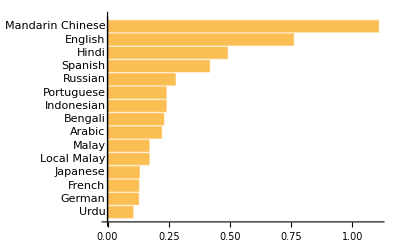

```mathematica
BarChart[EntityClass["Language","TotalSpeakers"->GreaterThan[100000000]]["TotalSpeakers","EntityAssociation"]//Reverse,BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

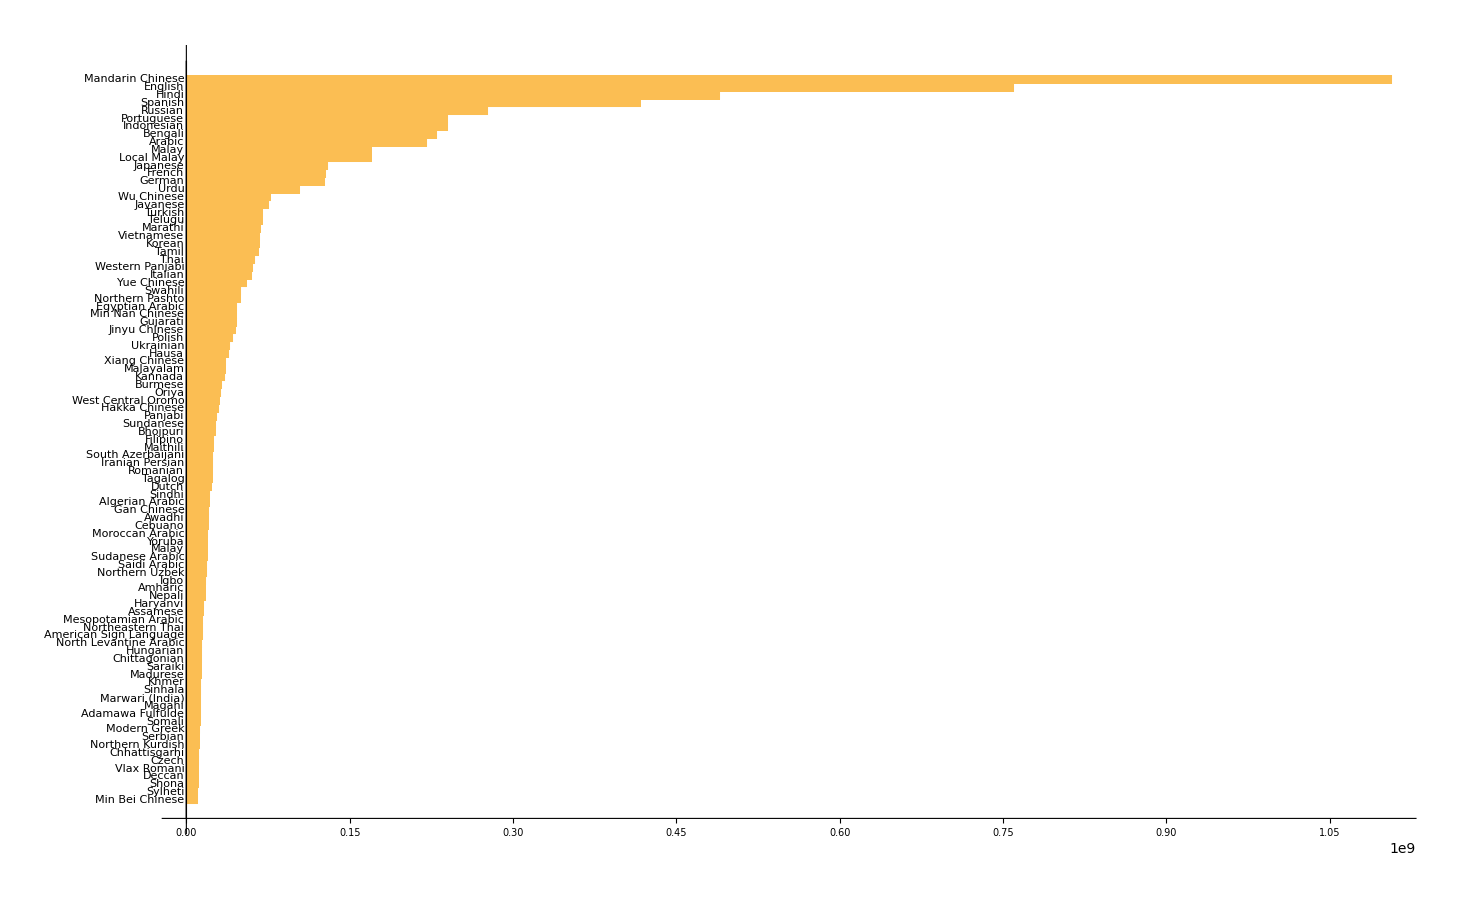

```mathematica
BarChart[EntityClass["Language","TotalSpeakers"->GreaterThan[10000000]]["TotalSpeakers","EntityAssociation"]//Reverse,BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

```mathematica
GeoRegionValuePlot[LinguisticAssistant,GeoRange->"World",ImageSize->400]
```

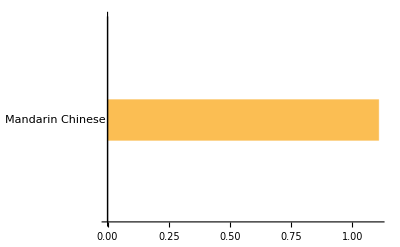

```mathematica
BarChart[EntityClass["Language","TotalSpeakers"->GreaterThan[1000000000]]["TotalSpeakers","EntityAssociation"]//Reverse,BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

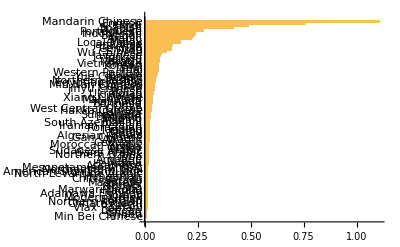

```mathematica
BarChart[EntityClass["Language","TotalSpeakers"->GreaterThan[10000000]]["TotalSpeakers","EntityAssociation"]//Reverse,BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

```mathematica
GeoRegionValuePlot[Entity["Language","English"][EntityProperty["Language","Speakers"]],GeoRange->"World",ImageSize->400]
```

-Graphics-

```mathematica
BarChart[EntityClass["Language","TotalSpeakers"->GreaterThan[100000000]]["TotalSpeakers","EntityAssociation"]//Reverse,BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

```mathematica
EntityClass["Language", "TotalSpeakers"->GreaterThan[100000000]]["TotalSpeakers"]
```

{1.1×10^9 people,7.6×10^8 people,4.9×10^8 people,4.2×10^8 people,2.8×10^8 people,2.4×10^8 people,2.4×10^8 people,2.3×10^8 people,2.2×10^8 people,1.7×10^8 people,1.7×10^8 people,1.3×10^8 people,1.3×10^8 people,1.3×10^8 people,1.×10^8 people}

```mathematica
EntityValue[Entity["Bridge","GoldenGateBridge::j6798"], "LongestSpan"]
```

4199.48 ft

```mathematica
Entity["Movie","ForrestGump::4kpjk"][EntityProperty["Movie","Runtime"]]
```

142 min

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

```mathematica
EntityValue["AdministrativeDivision","EntityCount"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
EntityClass["Country", "Population"->GreaterThan[10000000]]
```

EntityClass[Country,Population→GreaterThan[10000000]]

```mathematica
EntityList[EntityClass["Country","Population"->GreaterThan[10000000]]]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityList[EntityClass[Country,Population→GreaterThan[10000000]]]

```mathematica
EntityClass["Language","Properties"]
```

EntityClass[Language,Properties]

```mathematica
Entity["Country", "United States"]
```

Entity[Country,United States]

```mathematica
EntityClass["Country",{->TakeLargest[5]}]
```

EntityClass[Country,{→TakeLargest[5]}]

```mathematica
"plot in world map""country group"Manipulate[Graphics[({If[CountryData[#1,cl],Directive[Orange,EdgeForm[Brown]],LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{cl,{->TakeLargest[5]},"country group"},Dynamic[CanonicalName[CountryData["Classes"]],SynchronousUpdating->False],ControlType->PopupMenu},{{prop,"Population","country property"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

CountryData::notprop: {EntityProperty["Country", "GDP", {"CurrencyUnit" -> "CurrentUSDollar"}] -> TakeLargest[5]} is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

```mathematica
EntityClass["Country",{->TakeLargest[5]}]
```

EntityClass[Country,{→TakeLargest[5]}]

```mathematica
CanonicalName[EntityClass["Country",{->TakeLargest[5]}]]
```

{→TakeLargest[5]}

```mathematica
EntityTypeName[EntityClass["Country",{->TakeLargest[5]}]]
```

Country

```mathematica
EntityList[EntityClass["Country",{->TakeLargest[5]}]]
```

{United States,China,Japan,Germany,United Kingdom}

```mathematica
EntityClass["Language",{EntityProperty["Language","TotalSpeakers"]->TakeLargest[20]}]["TotalSpeakers","EntityAssociation"]
```

<|Mandarin Chinese→1.1×10^9 people,English→7.6×10^8 people,Hindi→4.9×10^8 people,Spanish→4.2×10^8 people,Russian→2.8×10^8 people,Portuguese→2.4×10^8 people,Indonesian→2.4×10^8 people,Bengali→2.3×10^8 people,Arabic→2.2×10^8 people,Malay→1.7×10^8 people,Local Malay→1.7×10^8 people,Japanese→1.3×10^8 people,French→1.3×10^8 people,German→1.3×10^8 people,Urdu→1.×10^8 people,Wu Chinese→7.7×10^7 people,Javanese→7.6×10^7 people,Turkish→7.×10^7 people,Telugu→7.×10^7 people,Marathi→6.8×10^7 people|>

```mathematica
BarChart[
Reverse@
EntityClass[
"Language",
"TotalSpeakers"->GreaterThan[100000000]]
["TotalSpeakers","EntityAssociation"],
BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

-Graphics-

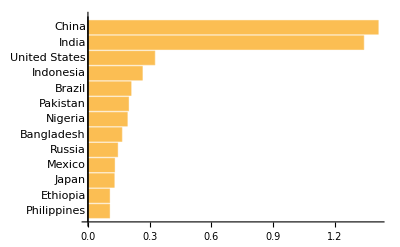

```mathematica
BarChart[
Reverse@
EntityClass[
"Country",
"Population"->GreaterThan[100000000]]
["Population","EntityAssociation"],
BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

```mathematica
BarChart[
Reverse@
EntityClass[
"Country",
"Population"->GreaterThan[100000000]]
["Population","EntityAssociation"],
BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

```mathematica
BarChart[
Reverse@
EntityClass[
"Country",
"GDP"->GreaterThan[100000000]]
["Population","EntityAssociation"],
BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]
```

BarChart::ldata: Missing[{Country,GDP,GreaterThan[100000000]},QueryValueIncompatibleWithProperty] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[Missing[{Country,GDP,GreaterThan[100000000]},QueryValueIncompatibleWithProperty],BarOrigin→Left,ChartLabels→Automatic,ImageSize→400]

```mathematica
With[{pivot="GDP"},
BarChart[
Reverse@
EntityClass[
"Country",
pivot->GreaterThan[100000000]]
[pivot,"EntityAssociation"],
BarOrigin->Left,ChartLabels->Automatic,ImageSize->400]]
```

BarChart::ldata: Missing[{Country,GDP,GreaterThan[100000000]},QueryValueIncompatibleWithProperty] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[Missing[{Country,GDP,GreaterThan[100000000]},QueryValueIncompatibleWithProperty],BarOrigin→Left,ChartLabels→Automatic,ImageSize→400]

```mathematica
FinancialDerivative[]
```

{Altiplano,{American,Call},{American,Put},Annapurna,{AsianArithmetic,European,Call},{AsianArithmetic,European,Put},{AsianGeometric,European,Call},{AsianGeometric,European,Put},Atlas,{BarrierDownIn,American,Call},{BarrierDownIn,American,Put},{BarrierDownIn,European,Call},{BarrierDownIn,European,Put},{BarrierDownOut,American,Call},{BarrierDownOut,American,Put},{BarrierDownOut,European,Call},{BarrierDownOut,European,Put},{BarrierUpIn,American,Call},{BarrierUpIn,American,Put},{BarrierUpIn,European,Call},{BarrierUpIn,European,Put},{BarrierUpOut,American,Call},{BarrierUpOut,American,Put},{BarrierUpOut,European,Call},{BarrierUpOut,European,Put},{BinaryAsset,European,Call},{BinaryAsset,European,Put},{BinaryCash,European,Call},{BinaryCash,European,Put},{Chooser,European},{CompoundCall,European,Call},{CompoundCall,European,Put},{CompoundPut,European,Call},{CompoundPut,European,Put},{DoubleBarrierKnockIn,American,Call},{DoubleBarrierKnockIn,American,Put},{DoubleBarrierKnockIn,European,Call},{DoubleBarrierKnockIn,European,Put},{DoubleBarrierKnockOut,American,Call},{DoubleBarrierKnockOut,American,Put},{DoubleBarrierKnockOut,European,Call},{DoubleBarrierKnockOut,European,Put},{European,Call},{European,Put},Everest,{ExtendibleHolder,European,Call},{ExtendibleHolder,European,Put},{ExtendibleWriter,European,Call},{ExtendibleWriter,European,Put},{Future,European,Call},{Future,European,Put},Himalaya,{LookbackFixed,European,Call},{LookbackFixed,European,Put},{LookbackFloating,American,Call},{LookbackFloating,American,Put},{LookbackFloating,European,Call},{LookbackFloating,European,Put},{OneTouch,American,Call},{OneTouch,American,Put},{Perpetual,American,Call},{Perpetual,American,Put},{PerpetualLookback,Call},{PerpetualLookback,Put},{Power,European,Call},{Power,European,Put},{PowerCapped,European,Call},{PowerCapped,European,Put},{Powered,European,Call},{Powered,European,Put},{QuantoFixedExchange,American,Call},{QuantoFixedExchange,American,Put},{QuantoFixedExchange,European,Call},{QuantoFixedExchange,European,Put},{QuantoFixedStrike,American,Call},{QuantoFixedStrike,American,Put},{QuantoFixedStrike,European,Call},{QuantoFixedStrike,European,Put},{RainbowBest,American},{RainbowBest,European},{RainbowMax,American,Call},{RainbowMax,American,Put},{RainbowMax,European,Call},{RainbowMax,European,Put},{RainbowMin,American,Call},{RainbowMin,American,Put},{RainbowMin,European,Call},{RainbowMin,European,Put},{RainbowMoney,American},{RainbowMoney,European},{RainbowWorst,American},{RainbowWorst,European},Russian,{Spread,American,Call},{Spread,American,Put},{Spread,European,Call},{Spread,European,Put},{Vanilla,American,Call},{Vanilla,American,Put},{Vanilla,European,Call},{Vanilla,European,Put}}

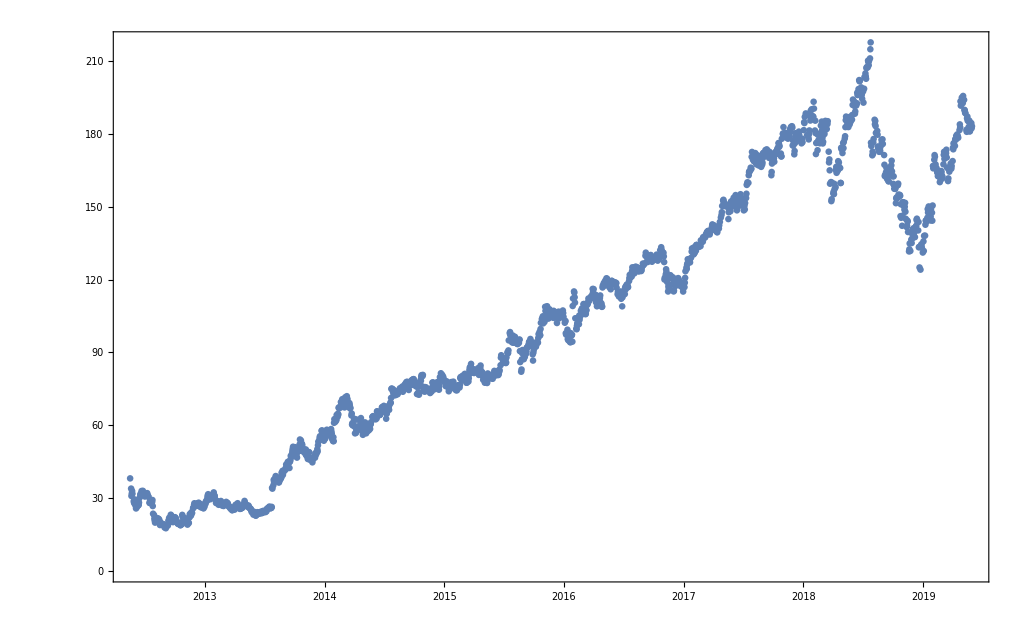

```mathematica
DateListPlot[
FinancialData["NASDAQ:FB", "Price", All]
,Joined->False]
```

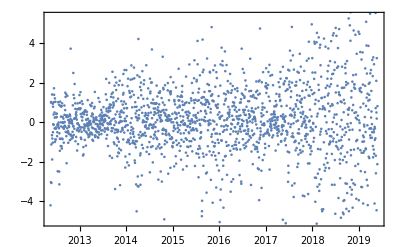

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False]]
```

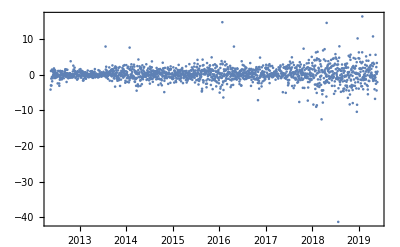

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->All]]
```

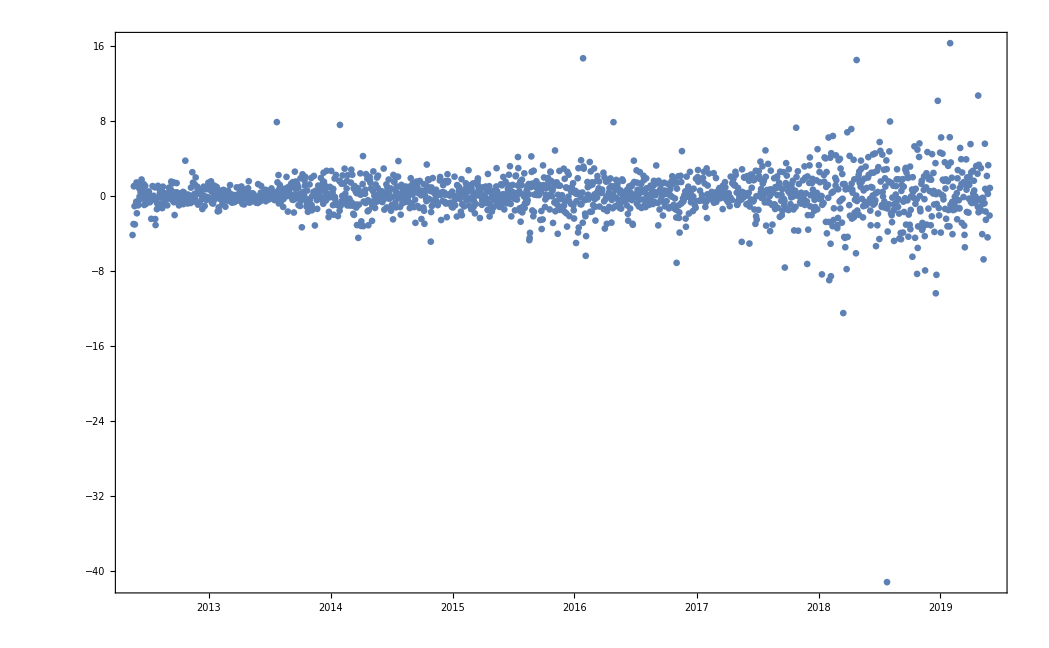

```mathematica
With[{list=FinancialData["NASDAQ:FB", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

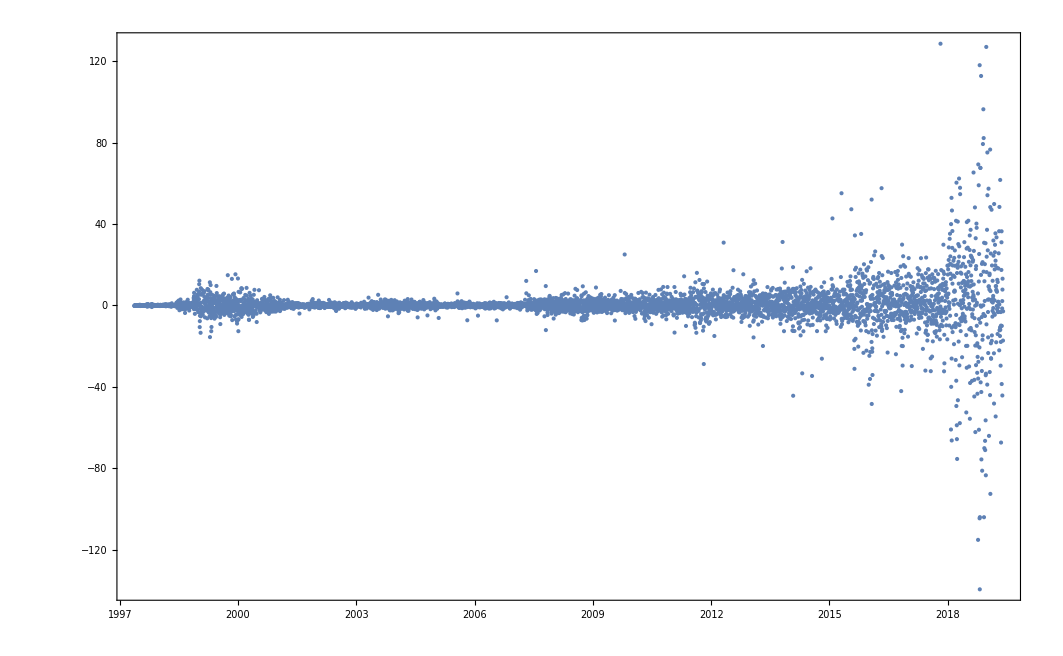

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

```mathematica
FinancialData[{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}, "Price"]
```

{1 117.95 $,178.30 $,125.73 $,183.01 $,36.38 $,44.73 $,188.22 $,129.57 $,1 816.32 $,76.17 $,53.57 $,351.85 $}

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Map[
With[{ts=FinancialData[#, "Price", All]},
Transpose[{
ts["Dates"][[;;-2]]
,
Differences@
ts["Values"]
}]]&, stocks]
]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{Transpose[{$Failed[],Differences[$Failed[Values]]}],10,{{Thu 23 May 2002 00:00:00GMT-7.,0.01 $},{Fri 24 May 2002 00:00:00GMT-7.,-0.05 $},{Tue 28 May 2002 00:00:00GMT-7.,-0.05 $},4272,{Fri 24 May 2019 00:00:00GMT-7.,0.39 $},{Tue 28 May 2019 00:00:00GMT-7.,-5.59 $},{Wed 29 May 2019 00:00:00GMT-7.,2.66 $}}}
 |  |  |  |

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Map[
With[{ts=FinancialData[#, "Price", All]},
Transpose[{
ts["Dates"][[;;-2]]
,
Differences@
ts["Values"]
}]]&, stocks]
]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{Transpose[{$Failed[],Differences[$Failed[Values]]}],10,{{Thu 23 May 2002 00:00:00GMT-7.,0.01 $},{Fri 24 May 2002 00:00:00GMT-7.,-0.05 $},{Tue 28 May 2002 00:00:00GMT-7.,-0.05 $},4272,{Fri 24 May 2019 00:00:00GMT-7.,0.39 $},{Tue 28 May 2019 00:00:00GMT-7.,-5.59 $},{Wed 29 May 2019 00:00:00GMT-7.,2.66 $}}}
 |  |  |  |

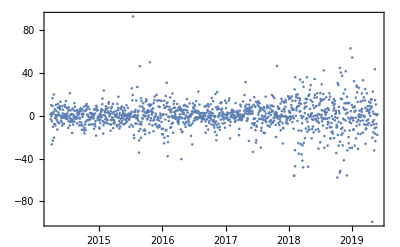

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

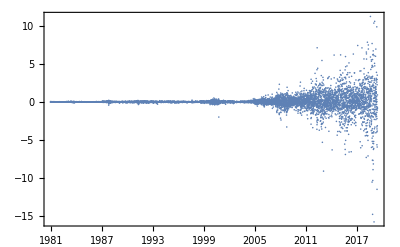
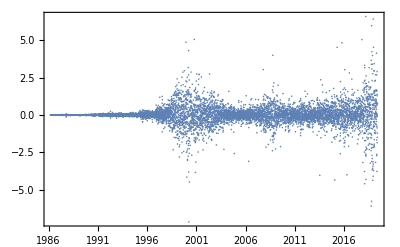
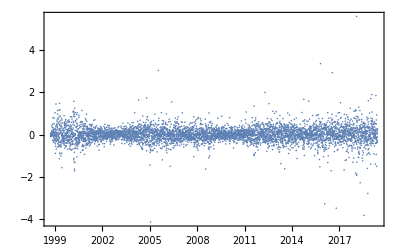
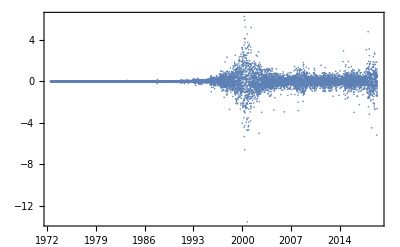
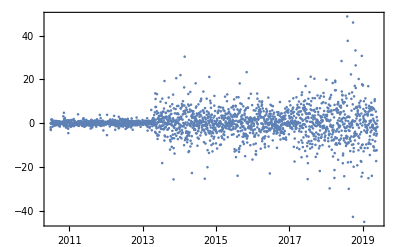
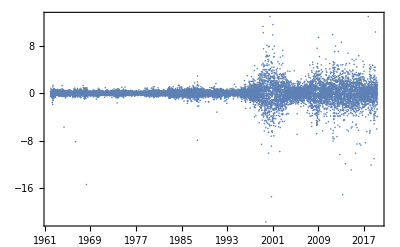
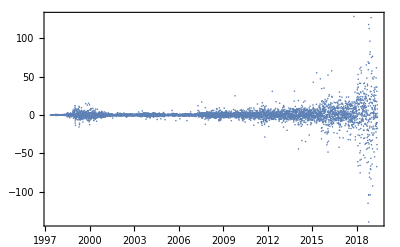
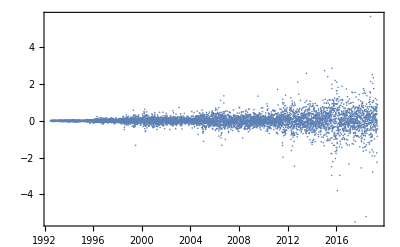
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Table[
With[{list=FinancialData[stock, "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
,{stock, stocks}
]]
```

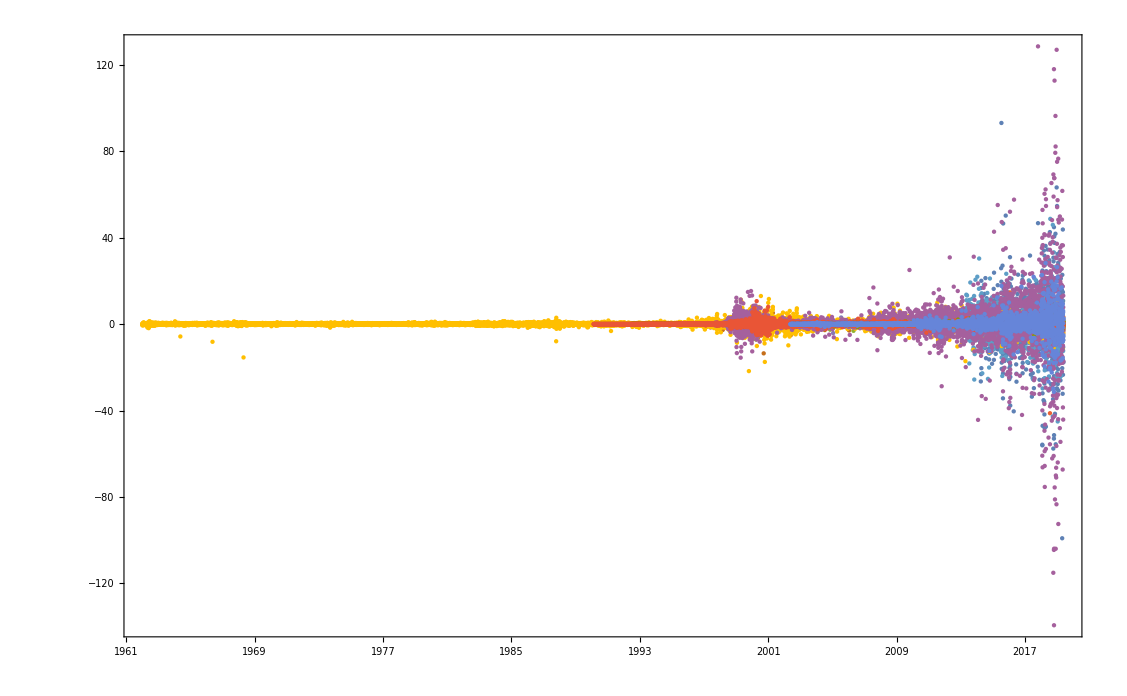

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
DateListPlot[
Table[
With[{list=FinancialData[stock, "Price", All]},
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
]
,{stock, stocks}
],Joined->False, PlotRange->Full]]
```

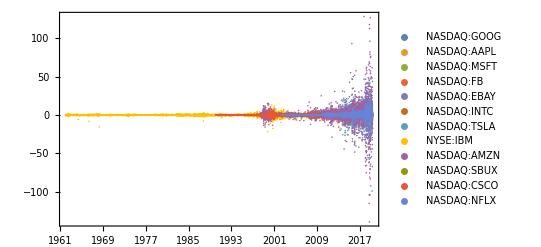

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
DateListPlot[
Table[
With[{list=FinancialData[stock, "Price", All]},
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
]
,{stock, stocks}
],Joined->False, PlotRange->Full, PlotLegends->stocks]]
```

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Table[
stock->With[{list=FinancialData[stock, "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
,{stock, stocks}
]]
```

{NASDAQ:GOOG→-Graphics-,NASDAQ:AAPL→-Graphics-,NASDAQ:MSFT→-Graphics-,NASDAQ:FB→-Graphics-,NASDAQ:EBAY→-Graphics-,NASDAQ:INTC→-Graphics-,NASDAQ:TSLA→-Graphics-,NYSE:IBM→-Graphics-,NASDAQ:AMZN→-Graphics-,NASDAQ:SBUX→-Graphics-,NASDAQ:CSCO→-Graphics-,NASDAQ:NFLX→-Graphics-}

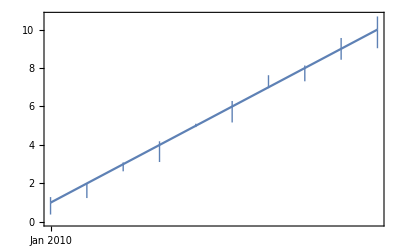

```mathematica
DateListPlot[Table[Around[n,RandomReal[1,2]],{n,10}],{2010,1,1}]
```

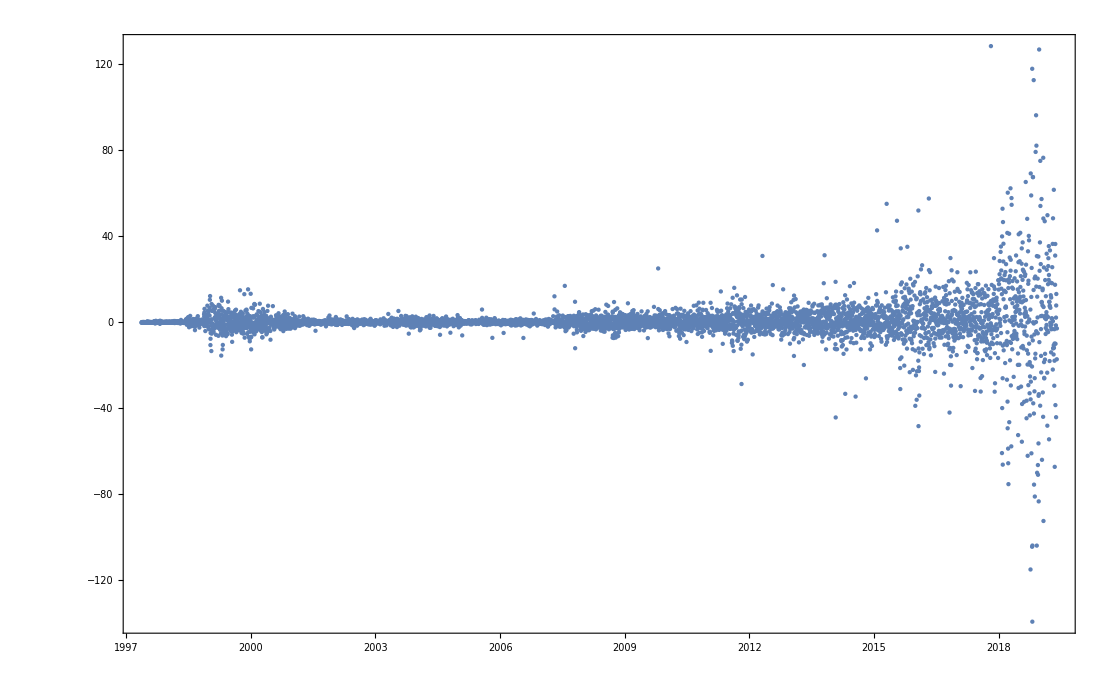

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
DateListPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

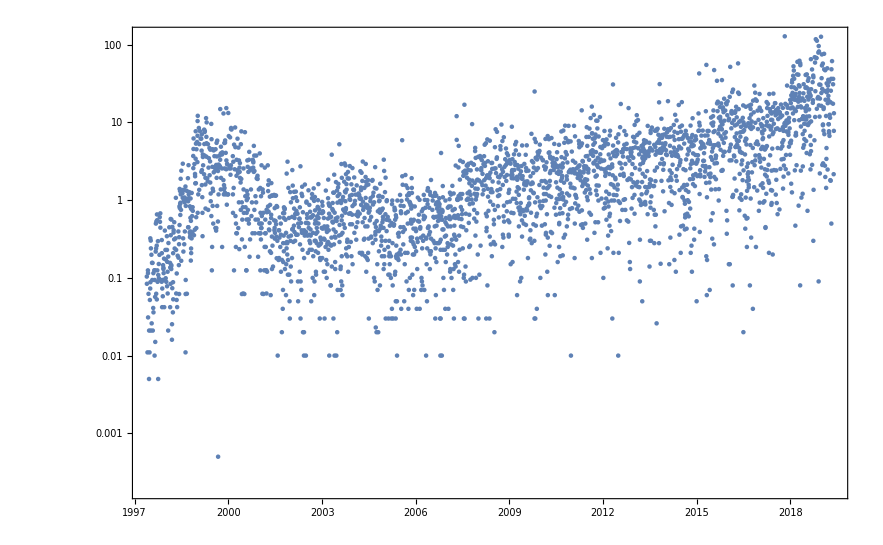

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
DateListLogPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

```mathematica
Databin["1qGFQ8v"]
```

Databin[…]

```mathematica
Databin["1qGFQ8v"]
```

Databin[…]

```mathematica
Databin[1]
```

$Failed

```mathematica
Databin["1qGFQ8v",-3]
```

Databin[…]

```mathematica
CreateDatabin[]
```

Databin[…]

```mathematica
DatabinAdd[Out[144], Out[132]]
```

Databin::apierrl: Your databin entry could not be added because it exceeds the 25 kb limit. To increase your entry limit, contact us.

$Failed

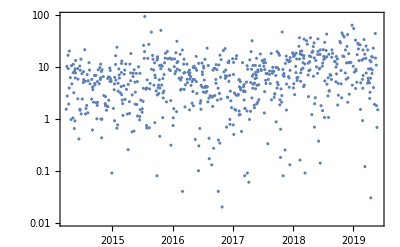
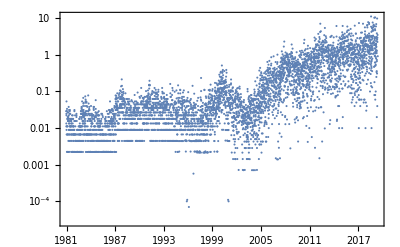
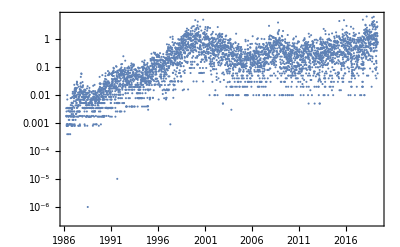
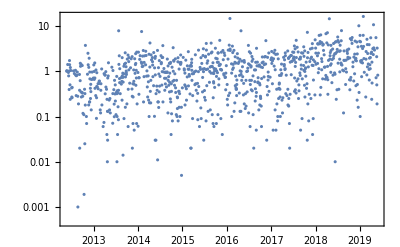
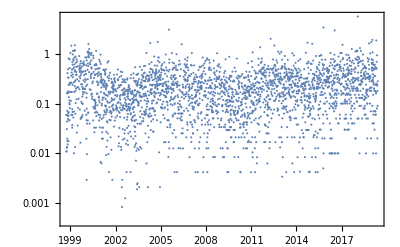
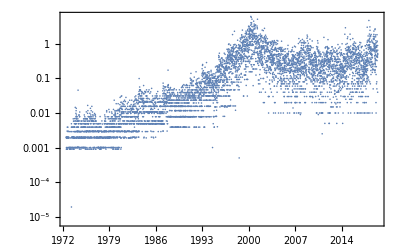
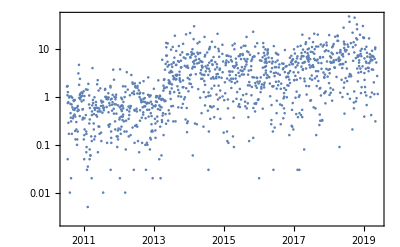
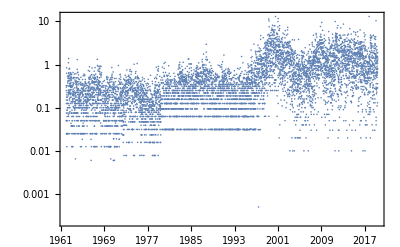
{NASDAQ:GOOG→-Graphics-,NASDAQ:AAPL→-Graphics-,NASDAQ:MSFT→-Graphics-,NASDAQ:FB→-Graphics-,NASDAQ:EBAY→-Graphics-,NASDAQ:INTC→-Graphics-,NASDAQ:TSLA→-Graphics-,NYSE:IBM→-Graphics-,NASDAQ:AMZN→-Graphics-,NASDAQ:SBUX→-Graphics-,NASDAQ:CSCO→-Graphics-,NASDAQ:NFLX→-Graphics-}

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Table[
stock->With[{list=FinancialData[stock, "Price", All]},
DateListLogPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
,{stock, stocks}
]]
```

```mathematica
CloudPut[Out[132]]
```

CloudObject[https://www.wolframcloud.com/objects/ec392b5b-5199-4570-93bf-fd0ff460cb2d]

```mathematica
CloudObject[["https://www.wolframcloud.com/objects/ec392b5b-5199-4570-93bf-fd0ff460cb2d"](https://www.wolframcloud.com/objects/ec392b5b-5199-4570-93bf-fd0ff460cb2d)]
```

CloudObject[https://www.wolframcloud.com/objects/ec392b5b-5199-4570-93bf-fd0ff460cb2d]

```mathematica
SystemOpen[CloudObject["https://www.wolframcloud.com/objects/ec392b5b-5199-4570-93bf-fd0ff460cb2d"]⟦1⟧]
```

```mathematica
CloudPut[Out[146]]
```

CloudObject[https://www.wolframcloud.com/objects/0522ab10-d2c6-4290-87f9-d256cf2fb1db]

```mathematica
SystemOpen[CloudObject["https://www.wolframcloud.com/objects/0522ab10-d2c6-4290-87f9-d256cf2fb1db"]⟦1⟧]
```

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/objects/0522ab10-d2c6-4290-87f9-d256cf2fb1db"]]
```

CloudObject: 0522ab10-d2c6-4290-87f9-d256cf2fb1db

```mathematica
Grid@Out@146
```

Grid[{NASDAQ:GOOG→-Graphics-,NASDAQ:AAPL→-Graphics-,NASDAQ:MSFT→-Graphics-,NASDAQ:FB→-Graphics-,NASDAQ:EBAY→-Graphics-,NASDAQ:INTC→-Graphics-,NASDAQ:TSLA→-Graphics-,NYSE:IBM→-Graphics-,NASDAQ:AMZN→-Graphics-,NASDAQ:SBUX→-Graphics-,NASDAQ:CSCO→-Graphics-,NASDAQ:NFLX→-Graphics-}]

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
Table[
{stock,With[{list=FinancialData[stock, "Price", All]},
DateListLogPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]}
,{stock, stocks}
]]
```

{{NASDAQ:GOOG,-Graphics-},{NASDAQ:AAPL,-Graphics-},{NASDAQ:MSFT,-Graphics-},{NASDAQ:FB,-Graphics-},{NASDAQ:EBAY,-Graphics-},{NASDAQ:INTC,-Graphics-},{NASDAQ:TSLA,-Graphics-},{NYSE:IBM,-Graphics-},{NASDAQ:AMZN,-Graphics-},{NASDAQ:SBUX,-Graphics-},{NASDAQ:CSCO,-Graphics-},{NASDAQ:NFLX,-Graphics-}}

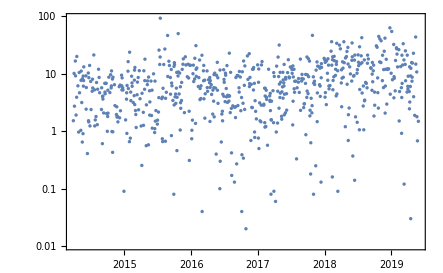
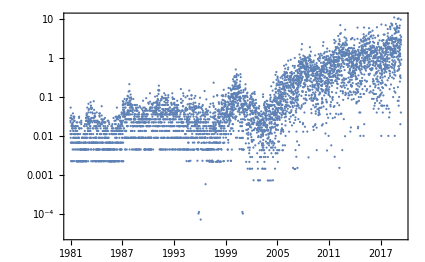
NASDAQ:GOOG | -Graphics-
NASDAQ:AAPL | -Graphics-
NASDAQ:MSFT | -Graphics-
NASDAQ:FB | -Graphics-
NASDAQ:EBAY | -Graphics-
NASDAQ:INTC | -Graphics-
NASDAQ:TSLA | -Graphics-
NYSE:IBM | -Graphics-
NASDAQ:AMZN | -Graphics-
NASDAQ:SBUX | -Graphics-
NASDAQ:CSCO | -Graphics-
NASDAQ:NFLX | -Graphics-

```mathematica
Grid@Out@154
```

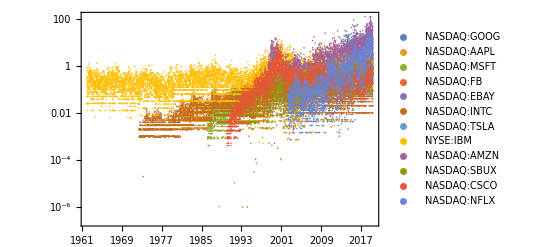

```mathematica
With[
{stocks=
{"NASDAQ:GOOG", "NASDAQ:AAPL", "NASDAQ:MSFT", "NASDAQ:FB", "NASDAQ:EBAY", "NASDAQ:INTC", "NASDAQ:TSLA", "NYSE:IBM", "NASDAQ:AMZN", "NASDAQ:SBUX", "NASDAQ:CSCO", "NASDAQ:NFLX"}},
DateListLogPlot[
Table[
With[{list=FinancialData[stock, "Price", All]},
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
]
,{stock, stocks}
],Joined->False, PlotRange->Full, PlotLegends->stocks]]
```

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
DateListLogPlot[
Transpose[{
list["Dates"][[;;-2]]
,
Differences@
list["Values"]
}]
,Joined->False, PlotRange->Full]]
```

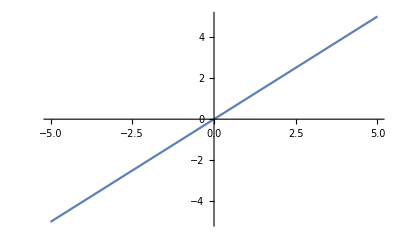

```mathematica
Plot[x, {x, -5, 5}]
```

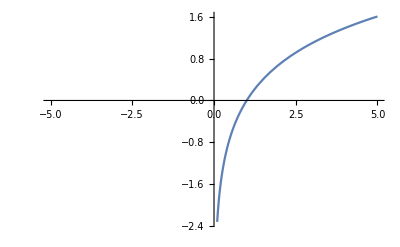

```mathematica
Plot[Log@x, {x, -5, 5}]
```

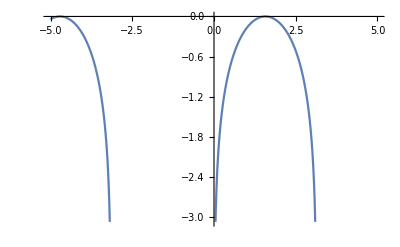

```mathematica
Plot[Log@Sin@x, {x, -5, 5}]
```

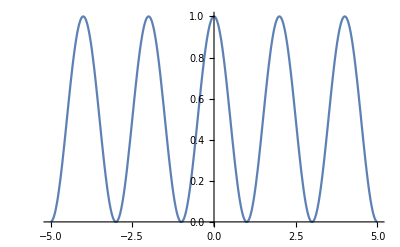

```mathematica
Plot[(1+Cos[π θ])/2, {θ, -5, 5}]
```

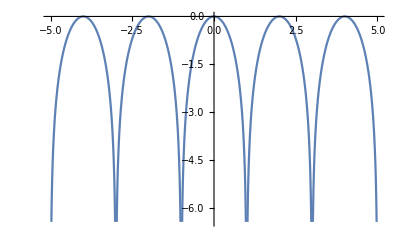

```mathematica
Plot[Log@((1+Cos[π θ])/2), {θ, -5, 5}]
```

```mathematica
Log[1]
```

0

```mathematica
Log[0]
```

-∞

```mathematica
Log[.5]
```

-0.693147

```mathematica
Log[.01]
```

-4.60517

```mathematica
Log[.000001]
```

-13.8155



```mathematica
Plot[Log@Exp@x, {x, -2, 2}]
```

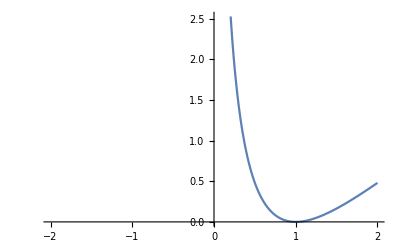

```mathematica
Plot[(Log@x)^2, {x, -2, 2}]
```

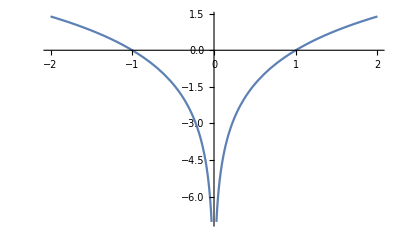

```mathematica
Plot[Log@(x^2), {x, -2, 2}]
```

```mathematica
Plot[Log@(x^2), {x, -2, 2}]
```

```mathematica
BlockchainData[]
```

<|Type→Bitcoin,Name→BTC.main,Core→Bitcoin,Blocks→578664,LatestHash→00000000000000000009cb9d2220122dd6f0852a63d071710c8582b0a45e9217,MinimumFee→174463  sat|>

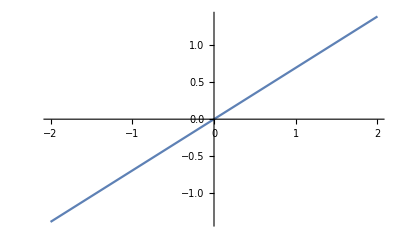

```mathematica
Plot[Log@(2^x), {x, -2, 2}]
```

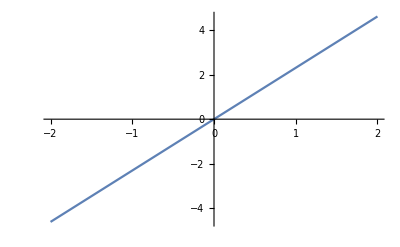

```mathematica
Plot[Log@(10^x), {x, -2, 2}]
```

```mathematica
D[f'[x]/f[x],x]
```

-f'[x]^2/f[x]^2+f''[x]/f[x]

```mathematica
Simplify[-f'[x]^2/f[x]^2+f''[x]/f[x]]
```

(-f'[x]^2+f[x] f''[x])/f[x]^2

```mathematica
With[{f=Identity},
(-f'[x]^2+f[x] f''[x])/f[x]^2]
```

-1/x^2

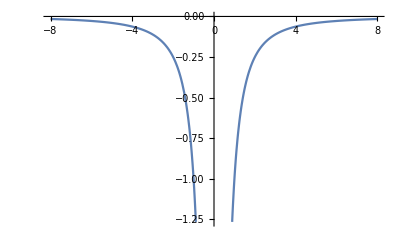

```mathematica
Plot[-1/x^2,{x,-8,8}]
```

```mathematica
With[{f=Exp},
(-f'[x]^2+f[x] f''[x])/f[x]^2]
```

0

```mathematica
With[{f=Log},
(-f'[x]^2+f[x] f''[x])/f[x]^2]
```

(-1/x^2-Log[x]/x^2)/Log[x]^2

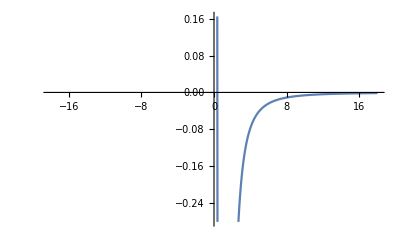

```mathematica
Plot[(-1/x^2-Log[x]/x^2)/Log[x]^2,{x,-18.,18.}]
```

```mathematica
With[{f=#^2&},
(-f'[x]^2+f[x] f''[x])/f[x]^2]
```

-2/x^2

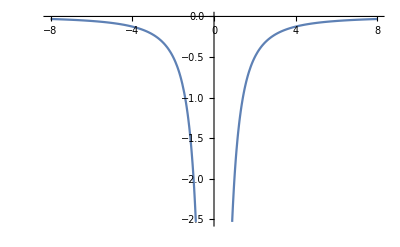

```mathematica
Plot[-2/x^2,{x,-8,8}]
```